# Magnon-SQ Coupling

```mathematica
ClearAll["Global`*"]
```

## Parameters

### Magnon Parameters

```mathematica
a=4*10^-10(*m*);
J=2;
h=0.05;
J2=0.15;
s=3/2;
DM=0.3;
κ=0;
ϕ=ArcTan[DM/J2](*Pi/2*);
```

### Constants

```mathematica
h=6.62*10^-34;(*m^2 kg s^-1*)
ℏ=6.582*10^-1; (*meV/THz*)
kb=8.6*10^-2; (*meV*)

γe=1.76*10^11;(*rad*s^-1*T^-1*)
μ0=4Pi*10^-7;(*N/m^2*)
μB=9.274*10^-24 (*J*T^-1*);
Ms=(3/2 μB s)/(a^2 w);
w=10^-10;(*m*)
```

### Computational Settings

```mathematica
WP=60;
AG=10;
```

## Lattice Construction

### MANR

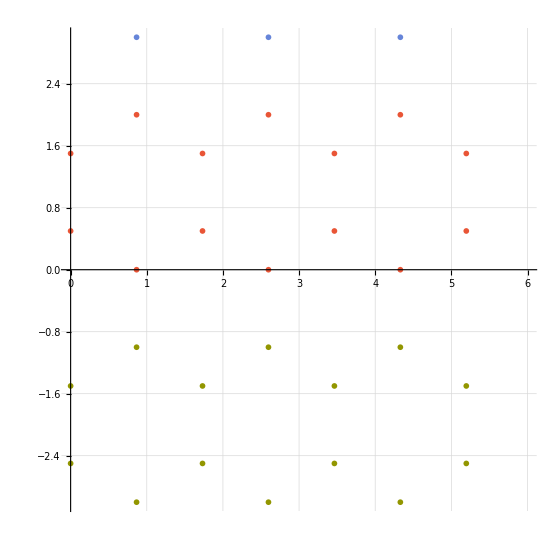

```mathematica
basis[m_]:={0,1/2}KroneckerDelta[1,Mod[m,4]]+{0,3/2}KroneckerDelta[2,Mod[m,4]]+{(√3)/2,2}KroneckerDelta[3,Mod[m,4]]+{(√3)/2,0}KroneckerDelta[0,Mod[m,4]];
shift[N_]:=RecurrenceTable[{β[n+1]==β[n]+Sqrt[3]KroneckerDelta[0,Mod[n,4]],β[1]==0},β,{n,1,N}];

r[m_,N_]:=basis[m]+{shift[N][[m]],0};
R[l_,m_,N_]:={0,3l}+r[m,N];

Num=2*7;
ListPlot[Table[Table[R[l,m,Num],{m,1,Num}],{l,-10,10}],PlotRange->{{0,6},{-3,3}},AspectRatio->1,GridLines->{}]
```

### MZNR

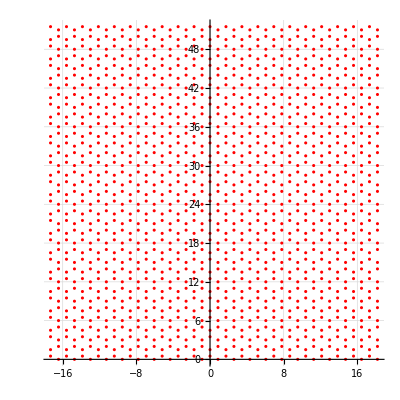

```mathematica
Zbasis[m_]:={(√3)/2,0}KroneckerDelta[1,Mod[m,4]]+{0,1/2}KroneckerDelta[2,Mod[m,4]]+{0,3/2}KroneckerDelta[3,Mod[m,4]]+{(√3)/2,2}KroneckerDelta[0,Mod[m,4]];
Zshift[N_]:=RecurrenceTable[{β[n+1]==β[n]+3KroneckerDelta[0,Mod[n,4]],β[1]==0},β,{n,1,N}];

rZ[m_,N_]:=Zbasis[m]+{0,Zshift[N][[m]]};
RZ[l_,m_,N_]:={√3 l,0}+rZ[m,N];

Num=2*35;
ListPlot[Table[Table[RZ[l,m,Num],{m,1,Num}],{l,-10,10}],GridLines->{},PlotRange->All,AspectRatio->1,PlotStyle->Red]
```

## Universal Functions

```mathematica
ZeroMatrix2N[N_]:=
Module[{N0=N,H},
H=Table[0,{2N0},{2N0}];
H
]

DyadG[x_,y_,z_,x1_,y1_,z1_]:=
Module[{DG},
DG=({{-(3 (x-x1)^2)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))+1/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)), -(3 (x-x1) (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)), -(3 (x-x1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))}, {-(3 (x-x1) (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)), -(3 (y-y1)^2)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))+1/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)), -(3 (y-y1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))}, {-(3 (x-x1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)), -(3 (y-y1) (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2)), -(3 (z-z1)^2)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(5/2))+1/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2))}});
DG
]
```

## MANR Functions

```mathematica
MANRMatrix2N[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_]:=
Module[{H,N0=N,W,X,Y,Z},
H=ZeroMatrix2N[N0];

Quiet[Do[
H[[2+2(i-1)-1,2+2(i-1)]]=W;
H[[2+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,2+2(i-1)]]];

H[[3+2(i-1)-1,3+2(i-1)]]=X;
H[[3+2(i-1),3+2(i-1)-1]]=Conjugate[H[[3+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1)-1,4+2(i-1)]]=Conjugate[X];
H[[4+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,4+2(i-1)]]];

H[[2+2(i-1)-1,3+2(i-1)]]=Y;
H[[3+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,3+2(i-1)]]];
H[[2+2(i-1),4+2(i-1)]]=Conjugate[Y];
H[[4+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),4+2(i-1)]]];

H[[2+2(i-1)-1,5+2(i-1)]]=Z;
H[[5+2(i-1),2+2(i-1)-1]]=Conjugate[H[[2+2(i-1)-1,5+2(i-1)]]];
H[[2+2(i-1),6+2(i-1)]]=Conjugate[Z];
H[[6+2(i-1),2+2(i-1)]]=Conjugate[H[[2+2(i-1),6+2(i-1)]]];

H[[i,i]]=3 J1 s +6J2 s +h+κ+(-1)^i Δκ;

W=-J1 s E^(ⅈ ξ);
X=-J1 s E^(ⅈ ξ/2);
Y=-2s √(DM^2+J2^2) E^(ⅈ ϕ) Cos[3/2 ξ];
Z=-s √(DM^2+J2^2)E^(-ⅈ ϕ);

,{i,1,2N0}];];
H[[1,1]]=H[[1,1]]-J1 s-3J2 s;
H[[2,2]]=H[[2,2]]-J1 s-3J2 s;
H[[3,3]]=H[[3,3]]-J2 s;
H[[4,4]]=H[[4,4]]-J2 s;
H[[2N0,2 N0]]=H[[2N0,2 N0]]-J1 s-3J2 s;
H[[2N0-1,2 N0-1]]=H[[2N0-1,2 N0-1]]-J1 s-3J2 s;
H[[2N0-2,2 N0-2]]=H[[2N0-2,2 N0-2]]-J2 s;
H[[2N0-3,2 N0-3]]=H[[2N0-3,2 N0-3]]-J2 s;
H
]

UMatrixMANR[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_]:=
Module[{N0=N,H,sortorder,U},
H=MANRMatrix2N[J1,J2,DM,s,κ,Δκ,h,ϕ,ξ,N0];
sortorder=Ordering[Eigensystem[H][[1]]];
U=Chop[Eigensystem[H][[2]][[sortorder]]];
U
]
```

## MANR Dispersion

```mathematica
NSamp=500; (*Number of sample points*)
Num=59; (*Half the number of bands*)
κ=0;
Δκ=0; (*Difference in easy-axis anisotropy*)

f2[ξ_]:=Module[{Ham,sortorders,dumH},Ham=MANRMatrix2N[J,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];
dumH=Eigenvalues[Ham];(*eigenvalues*)sortorders=Ordering[dumH];(*This orders the eigenvalues and eigenfunctions accordingly*)Table[{ξ,dumH[[sortorders]][[i]]/(2 Pi ℏ)},{i,1,2 Num}]]

GetBand[M_,disp_]:=Module[{band},(*Return single band (as a function of quasi-momentum) given band index M and dispersion disp.*)If[M>Length[disp]||M<0,Throw["Invalid band index!"]];
band=Table[disp[[j]][[M]],{j,1,Length[disp]}];
band]

Dispersion=ParallelMap[f2,Table[-Pi/3+j*N[(2 Pi/3)/NSamp],{j,0,NSamp}]];
```

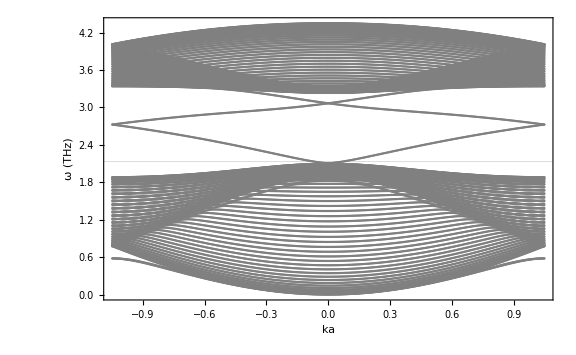

```mathematica
p=ListPlot[Dispersion,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Gray,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,GridLines->{{},{2.13}}];
p1=ListPlot[GetBand[Num+1,Dispersion],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Blue,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,GridLines->{{},{2.13}}];
Show[p]
```

## MANR-SQ Coupling

### Wavefunction Algorithm (must run)

```mathematica
WaveAlgo[J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,Num_,Naux_,upperbound_,lowerbound_]:=
Module[{N0=Num,NBand=Naux,A,H,sortorder,BandIndices},
Do[
ξ=-Pi/3+j* N[(2 Pi/3)/Naux];
H=MANRMatrix2N[J,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];

A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];*)

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
FindIndices[NBand_,N0_,ub_,lb_]:=
Module[{EmptyList,Indices},
EmptyList={};

Do[
Do[
If[lb<Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}][[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[Table[f[ξ][[i]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/NBand]}]]}]
,{i,1,2N0}];

Indices=DeleteDuplicates[EmptyList];
Indices
];

BandIndices=FindIndices[Naux,Num,upperbound,lowerbound];

(*Find k value and corresponding band index for a fixed energy*)
FindMom[ω_,err_]:=
Module[{EmptyList,Mom},
EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)
];

(*Takes the mean value of closely separated k values*)
MeanMom[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMom[ω,err],Abs[#1[[2]]-#2[[2]]]<err&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];

(*Calculates the wavefunction for impure spin lattice*)
(*NOTE: I changed the x recurrence table to sum in steps of 1/2 instead of √3/2*)
wavefunctions[ω_,err_]:=
Module[{wavefunction,U,g,k,band,β,n,x,MomList},
wavefunction={};
MomList=MeanMom[ω,err];
x=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
Do[
k=MomList[[j]][[2]];
band=MomList[[j]][[1]];
U=UMatrixMANR[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
g=Table[{x[[M]] *a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2Num}];
AppendTo[wavefunction,g]
,{j,1,Length[MomList]}];

wavefunction

];

];
```

```mathematica
Num=73;
NSamp=100;
WaveAlgo[J,J2,DM,s,κ,Δκ,h,ϕ,Num,NSamp,3.3,1.9];//AbsoluteTiming
```

{10.0147,Null}

### Wavefunction

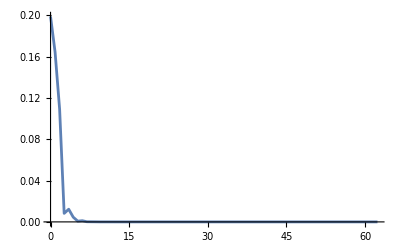

```mathematica
xlist2=RecurrenceTable[{β[n+1]==β[n]+(√3)/2 KroneckerDelta[0,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
Uwf=UMatrixMANR[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
ListLinePlot[Table[{xlist2[[i]],(Abs[Uwf[[Num+2]]]^2)[[i]]},{i,1,Length[xlist2]}],PlotRange->All]
```

### Coupling Function

```mathematica
Γ[x_,y_,z_,xlist_,ylist_,l_,N_]:=
Module[{gamma,xp,yp},
xp=xlist;
yp=ylist+3l;
(*gamma=-(3 (x-xp)^2)/(((x-xp)^2+(y-yp)^2+(z)^2)^(5/2))-(6 ⅈ (x-xp) (y-yp))/(((x-xp)^2+(y-yp)^2+(z)^2)^(5/2))+(3 (y-yp)^2)/(((x-xp)^2+(y-yp)^2+(z)^2)^(5/2))*)
gamma = -(3 (x-xp)^2)/(((x-xp)^2+(y-yp)^2+(z)^2)^(5/2))+1/(((x-xp)^2+(y-yp)^2+(z)^2)^(3/2))-(3 (y-yp)^2)/(((x-xp)^2+(y-yp)^2+(z)^2)^(5/2))+1/(((x-xp)^2+(y-yp)^2+(z)^2)^(3/2))
];

gMANR[ω_,k_,band_,U_,Numx_,Numy_,x_,y_,z_,xlist_,ylist_]:=
Module[{g,G,x1,y1,z1},
(*
Return value of dipole coupling for MANR-SQ interactions for a SQ placed at (x,y,z) with frequency ω; 
INPUTS;
ω: SQ frequency;
k: resonant magnon momentum, should be found via MeanMom[] or otherwise;
band: band index corresponding to resonant magnon momentum, should be found via MeanMom[] or otherwise;
U: unitary transformation matrix. Rows correspond to eigensates;
Numx: number of spins in x direction (non-periodic) for single species!;
Numy: number of unit cells in y direction (periodic, should be much greater than Numx);
x,y,z: coordinates of SQ;
xlist,ylist: vectors of size 2Numx corresponding to the positions of all points within the unit cell (x and y, respectively).
*)
(*g=Sum[Exp[ⅈ k R[l,m,2Numx][[2]]]*U[[band]][[m]]*Γ[x,y,z,l,m,2Numx],{m,1,2Numx},{l,-Numy/2,Numy/2}];*)
g=Sum[(Exp[ⅈ k (ylist+3l)]*U[[band]]).Γ[x,y,z,xlist,ylist,l,2Numx],{l,-Numy/2,Numy/2}];
g

];
```

#### Single Frequency

```mathematica
CouplingList={};
ω=3.15;
(*Num=35;*)
MomList=MeanMom[ω,1/100];
If[Length[MomList]>2,MomList={Mean[MomList[[1;;Length[MomList]/2]]],Mean[MomList[[Length[MomList]/2+1;;Length[MomList]]]]}];
Do[
band=MomList[[j]][[1]];
k=MomList[[j]][[2]];
U=UMatrixMANR[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
y=0;
d=12.5;
NSteps=50;
Numy=833;
Rlist=Table[R[0,m,2Num],{m,1,2Num}];
xlist=Rlist[[All,1]];
ylist=Rlist[[All,2]];
g[x_]:=Module[{g},
g=Norm[gMANR[ω,k,band,U,Num,Numy,x,y,d,xlist,ylist]];
g
];
Coupling=ParallelMap[g,Table[-15+j*N[((√3)/2 Num+30)/NSteps],{j,0,NSteps}]];
AppendTo[CouplingList,Coupling]
,{j,1,Length[MomList]}];//AbsoluteTiming
```

{36.7356,Null}

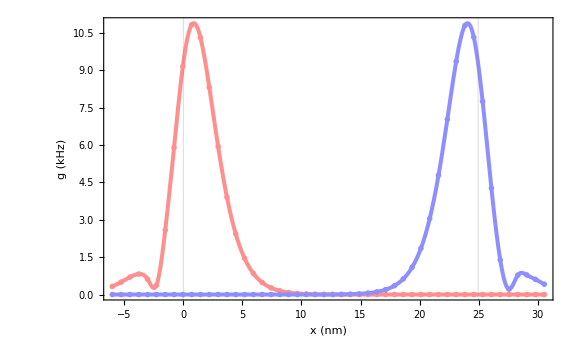

```mathematica
x=Table[-15+j*N[(Sqrt[3]/2 Num+30)/NSteps],{j,0,NSteps}]*0.4;
A=Sqrt[s/Numy] ((2 μB)^2 μ0)/(2 a^3 h)*10^-3;
ListPlot[Table[Table[{x[[i]],A*CouplingList[[j]][[i]]},{i,1,NSteps}],{j,1,Length[CouplingList]}],PlotRange->All,GridLines->{{0,Sqrt[3]/2 (Num-1)*0.4},{}},Joined->True,InterpolationOrder->3,PlotMarkers->{"OpenMarkers",Small},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"x (nm)","g (kHz)"},PlotStyle->{Directive[Lighter[Lighter[Red]],Thickness[.005]],Directive[Lighter[Lighter[Blue]],Thickness[.005]]},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
```

```mathematica
Sqrt[3]/2 (Num-1)/1500//N
```

0.0415692

```mathematica
2500/3//N
```

833.333

#### Range of Frequencies

```mathematica
SetDirectory["C:\\Users\\jeffc\\Documents\\topo_magnons\\MANR_g_v_omega_d=8.75"]
```

C:\Users\jeffc\Documents\topo_magnons\MANR_g_v_omega_d=8.75

```mathematica
Do[
CouplingList={};
ω=2.15+i;
MomList=MeanMom[ω,1/100];
If[Length[MomList]>2,MomList={Mean[MomList[[1;;Length[MomList]/2]]],Mean[MomList[[Length[MomList]/2+1;;Length[MomList]]]]}];

Do[
band=MomList[[j]][[1]];
If[NotElement[band,Integers]==True,Break[]];
k=MomList[[j]][[2]];
U=UMatrixMANR[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
y=0;
d=8.75;
NSteps=100;
Numy=250;
Rlist=Table[R[0,m,2Num],{m,1,2Num}];
xlist=Rlist[[All,1]];
ylist=Rlist[[All,2]];
g[x_]:=Module[{g},
g=Norm[gMANR[ω,k,band,U,Num,Numy,x,y,d,xlist,ylist]];
g
];
Coupling=ParallelMap[g,Table[-15+j*N[((√3)/2 Num+30)/NSteps],{j,0,NSteps}]];
AppendTo[CouplingList,Coupling]
,{j,1,Length[MomList]}];
Export["MANR-SQ_g_d="<>ToString[d]<>"_omega="<>ToString[ω]<>".mx",CouplingList]
,{i,0,1.05,0.01}];
```

```mathematica
Directory[]
```

C:\Users\jeffc\Documents

```mathematica
x=Table[-15+j*N[(Sqrt[3]/2 Num+30)/NSteps],{j,0,NSteps}]*0.4;
A=Sqrt[s/Numy] ((2 μB)^2 μ0)/(4 Sqrt[2] a^3 h)*10^-3;
ListPlot[Table[Table[{x[[i]],CouplingList[[j]][[i]]},{i,1,NSteps}],{j,1,Length[CouplingList]}],PlotRange->All,GridLines->{{0,Sqrt[3]/2 Num*0.4},{}},Joined->True,InterpolationOrder->3,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"x (nm)","g (a.u.)"},PlotStyle->{Directive[(*Lighter[Lighter[Blue]],*)Thickness[.005]]},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
```

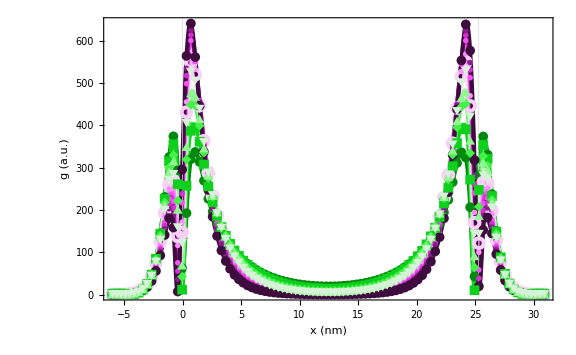

```mathematica
TotalCoupling=Table[Total[CouplingList[[2j-1;;2j]]],{j,1,Length[CouplingList]/2}];
Colors=Table[Directive[ColorData["GreenPinkTones",j/11],Thickness[.005]],{j,1,Length[CouplingList]/2}];
x=Table[-15+j*N[(Sqrt[3]/2 Num+30)/NSteps],{j,0,NSteps}]*0.4;
A=Sqrt[s/Numy] ((2 μB)^2 μ0)/(4 Sqrt[2] a^3 h)*10^-3;
ListPlot[Table[Table[{x[[i]],A*TotalCoupling[[j]][[i]]},{i,1,NSteps}],{j,1,Length[TotalCoupling]}],PlotRange->All,GridLines->{{0,Sqrt[3]/2 Num*0.4},{}},Joined->True,InterpolationOrder->3,PlotMarkers->{Automatic,Medium},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"x (nm)","g (a.u.)"},PlotStyle->Colors,PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,FrameStyle->Thick,GridLinesStyle->Thick]
```

```mathematica
Colors=Table[Directive[ColorData["GreenPinkTones",j/Length[TotalCoupling]],Thickness[.005]],{j,1,Length[TotalCoupling]}];
ListLinePlot3D[A*TotalCoupling,PlotRange->All,PlotTheme->"Scientific",PlotStyle->Colors,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],Ticks->{{{0,-5},{50,15},{100,30}},{{1,2.15},{11,2.25},{22,3.2}},{0,25,50}},AxesStyle->Thick,AxesLabel->{"x (nm)","ω/2π (THz)","g (kHz)"}]
```

-Graphics3D-

```mathematica
SetDirectory["C:\\Users\\jeffc\\Documents\\topo_magnons\\MANR_g_v_omega_d=15"];
CouplingListAll=Import[#]&/@FileNames[];
```

```mathematica
TotalCoupling=Table[Total[CouplingListAll[[j]]],{j,1,Length[CouplingListAll]}];
Colors=Table[Directive[ColorData["GreenPinkTones",j/Length[TotalCoupling]],Thickness[.005]],{j,1,Length[TotalCoupling]}];
Numy=250;
A=Sqrt[s/Numy] ((2 μB)^2 μ0)/(4 Sqrt[2] a^3 h)*10^-3;
ListLinePlot3D[A*TotalCoupling,PlotRange->All,PlotTheme->"Scientific",PlotStyle->Colors,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],Ticks->{{{1,-5},{50,15},{100,30}},{{1,2.15},{51,2.7},{102,3.2}},{5,10,15,20}},AxesStyle->Thick,AxesLabel->{"x (nm)","ω/2π (THz)","g (kHz)"},ImageSize->Large,ViewPoint->{2.4,-2.4,1.}]
```

-Graphics3D-

```mathematica
SetDirectory["C:\\Users\\jeffc\\Documents\\topo_magnons\\MANR_g_v_omega"];
CouplingListAll=Import[#]&/@FileNames[];
TotalCoupling=Table[Total[CouplingListAll[[j]]],{j,1,Length[CouplingListAll]}];
A=Sqrt[s/Numy] ((2 μB)^2 μ0)/(4 Sqrt[2] a^3 h)*10^-3;
MaxG=Table[Max[A*TotalCoupling[[i]]],{i,1,Length[TotalCoupling]}];
Omegas=DeleteElements[Range[2.15,3.2,0.01],{2.72,2.73,3.05,3.06,3.2}];
MaxList=Flatten[{Omegas,MaxG},{{2},{1}}];
SetDirectory["C:\\Users\\jeffc\\Documents\\topo_magnons\\MANR_maxg_vs_omega"]
Export["MANR_maxg_v_omega_d=12.5.mx",MaxList]
(*p5=ListPlot[Flatten[{Omegas,MaxG},{{2},{1}}],Joined->True,InterpolationOrder->3,PlotMarkers->{Automatic,Medium},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ω/2π (THz)","|g_max| (kHz)"},PlotStyle->Red,PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,FrameStyle->Thick]*)
```

C:\Users\jeffc\Documents\topo_magnons\MANR_maxg_vs_omega

MANR_maxg_v_omega_d=12.5.mx

C:\Users\jeffc\Documents\topo_magnons\MANR_maxg_vs_omega

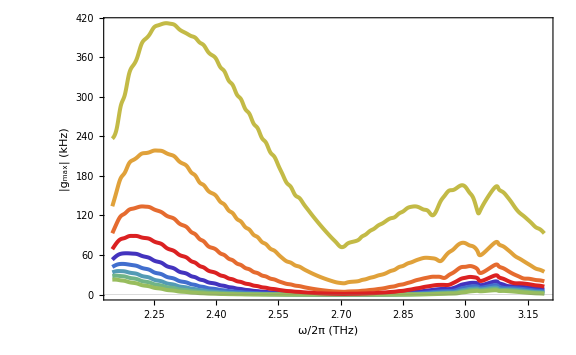

{{{4,2}},{{3,2}},{{3,2}},{{2,2}},{{1,2}},{{14,2}},{{12,2}},{{8,2}},{{6,2}}}

{2.18,2.17,2.17,2.16,2.15,2.28,2.26,2.22,2.2}

```mathematica
SetDirectory["C:\\Users\\jeffc\\Documents\\topo_magnons\\MANR_maxg_vs_omega"]
MaxListAll=Import[#]&/@FileNames[];
(*MaxListAllLog=Flatten[{MaxListAll[[All,1]],Log[MaxListAll[[All,2]]]},{{2},{1}}];*)
Colors=Table[Directive[ColorData["Rainbow",j/Length[MaxListAll]],Thickness[.005]],{j,1,Length[MaxListAll]}];
ListPlot[MaxListAll,PlotRange->All,Joined->True,InterpolationOrder->3,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ω/2π (THz)","|g_max| (kHz)"},PlotStyle->Colors,PlotRange->All,ImageSize->Large,PlotTheme->"Scientific"]
```

```mathematica
Pos=Map[Position[MaxListAll[[#]],Max[MaxListAll[[#]]]]&,Range[1,Length[MaxListAll]]]
MaxOmegas=Map[MaxListAll[[#]][[Pos[[#]][[1]][[1]]]]&,Range[1,Length[MaxListAll]]][[All,1]]
MaxKs=ParallelMap[MeanMom[#,1/100][[1]][[2]]&,MaxOmegas]
```

{{{4,2}},{{3,2}},{{3,2}},{{2,2}},{{1,2}},{{14,2}},{{12,2}},{{8,2}},{{6,2}}}

{2.18,2.17,2.17,2.16,2.15,2.28,2.26,2.22,2.2}

{0.146608,0.146608,0.146608,0.125664,0.10472,0.293215,0.272271,0.20944,0.188496}

```mathematica
FileNames[]
```

{MANR_maxg_v_omega_d=10.0.mx,MANR_maxg_v_omega_d=11.25.mx,MANR_maxg_v_omega_d=12.5.mx,MANR_maxg_v_omega_d=13.75.mx,MANR_maxg_v_omega_d=15.mx,MANR_maxg_v_omega_d=5.00.mx,MANR_maxg_v_omega_d=6.25.mx,MANR_maxg_v_omega_d=7.50.mx,MANR_maxg_v_omega_d=8.75.mx}

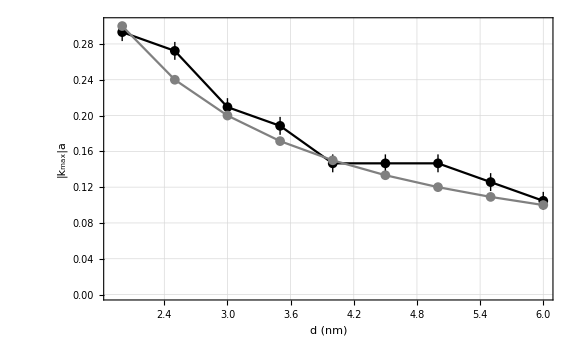

```mathematica
(*dlist={10,11.25,12.5,13.75,15,5,6.25,7.5,8.75};*)
dlist={4,4.5,5,5.5,6,2,2.5,3,3.5};
d1=ListPlot[Around[Sort[Flatten[{dlist,MaxKs},{{2},{1}}]],0.01],PlotRange->All,Joined->True,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],PlotMarkers->{Automatic,Medium},FrameLabel->{"d (nm)","|k_max|a"},PlotStyle->Black,PlotRange->All,ImageSize->Large,PlotTheme->"Scientific",GridLines->{},IntervalMarkers->"Fences"];
d2=ListPlot[Sort[Flatten[{dlist,0.6/dlist},{{2},{1}}]],PlotRange->All,Joined->True,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],PlotMarkers->{Automatic,Medium},FrameLabel->{"d (nm)","|k_max|a"},PlotStyle->Gray,PlotRange->All,ImageSize->Large,PlotTheme->"Scientific",GridLines->{}];
Show[d1,d2]
```

```mathematica
dlist={5,6.25,7.5,8.75,10,11.25,12.5,13.65,15};
g220List={};
Do[
(*SetDirectory["C:\\Users\\jeffc\\Documents\\topo_magnons\\MANR_g_v_omega_d="<>ToString[dlist[[i]]]];*)
CouplingListAll=(*Import["C:\\Users\\jeffc\\Documents\\topo_magnons\\MANR_g_v_omega_d="<>ToString[dlist[[i]]<>"\\MANR-SQ_g_d="<>ToString[dlist[[i]]]<>"_omega=2.20.mx"]];*)
Import["C:\\Users\\jeffc\\Documents\\topo_magnons\\MANR_g_v_omega_d="<>ToString[dlist[[i]]]<>"\\MANR-SQ_g_d="<>ToString[dlist[[i]]]<>"_omega=2.25.mx"];
AppendTo[g220List,CouplingListAll];
,{i,1,Length[dlist]}]
```

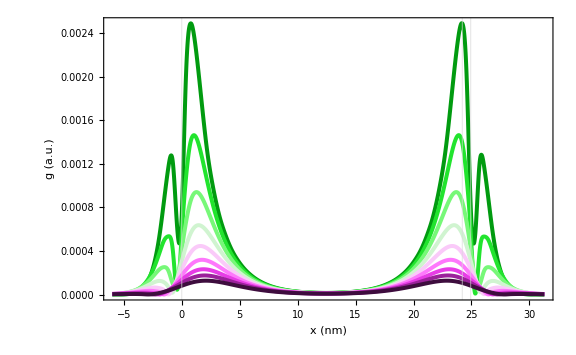

```mathematica
x=Table[-15+j*N[(Sqrt[3]/2 Num+30)/NSteps],{j,0,NSteps}]*0.4;
TotalCoupling220=Table[Total[g220List[[j]]],{j,1,Length[g220List]}];
g220=Table[Table[{x[[i]],TotalCoulpling220[[j]][[i]]},{i,1,Length[x]}],{j,1,Length[TotalCoupling220]}];
Colors=Table[Directive[ColorData["GreenPinkTones",j/Length[TotalCoupling220]],Thickness[.005]],{j,1,Length[TotalCoupling220]}];
ListLinePlot[g220,PlotRange->All,GridLines->{{0,Sqrt[3]/2 (Num-1)*0.4,24.2},{}},Joined->True,InterpolationOrder->3,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"x (nm)","g (a.u.)"},PlotStyle->Colors,PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,FrameStyle->Thick,GridLinesStyle->Thick]
```

```mathematica
Position[g220[[1]],Max[g220[[1]][[All,2]]]]
```

{{82,2}}

```mathematica
g220[[1]][[82]]
```

{24.2032,0.00248724}

```mathematica
g220List
```

{{{1.69592×10^-6,1.34402×10^-6,3.5479×10^-7,1.83127×10^-6,6.21291×10^-6,0.0000145638,0.0000300124,0.0000580083,0.000107806,0.00019432,0.000339002,0.000564707,0.000871563,0.00117432,0.00121618,0.000621589,0.000664091,0.00195122,0.00248058,0.00235381,0.0020222,0.00164491,0.00130386,0.00105165,0.000851825,0.000690934,0.000568014,0.000465804,0.000382569,0.000317438,0.00026282,0.000217628,0.000180914,0.000150045,0.000124692,0.000103939,0.0000864607,0.0000719828,0.0000600157,0.0000500011,0.0000417171,0.0000348299,0.0000290571,0.0000242639,0.0000202732,0.0000169375,0.0000141617,0.0000118427,9.90313×10^-6,8.2868×10^-6,6.93609×10^-6,5.80636×10^-6,4.8628×10^-6,4.07317×10^-6,3.41253×10^-6,2.86028×10^-6,2.39786×10^-6,2.01069×10^-6,1.68659×10^-6,1.41505×10^-6,1.1876×10^-6,9.97066×10^-7,8.37329×10^-7,7.03428×10^-7,5.91173×10^-7,4.97025×10^-7,4.18064×10^-7,3.51826×10^-7,2.96242×10^-7,2.496×10^-7,2.10453×10^-7,1.7759×10^-7,1.5×10^-7,1.26833×10^-7,1.07376×10^-7,9.10341×10^-8,7.73062×10^-8,6.57726×10^-8,5.60821×10^-8,4.79392×10^-8,4.10963×10^-8,3.53451×10^-8,3.05106×10^-8,2.64463×10^-8,2.30292×10^-8,2.01563×10^-8,1.77407×10^-8,1.57097×10^-8,1.40019×10^-8,1.25657×10^-8,1.13579×10^-8,1.03422×10^-8,9.48782×10^-9,8.76915×10^-9,8.16452×10^-9,7.65574×10^-9,7.22752×10^-9,6.86699×10^-9,6.56334×10^-9,6.30748×10^-9,6.09177×10^-9},{6.29049×10^-9,6.54319×10^-9,6.84307×10^-9,7.19912×10^-9,7.62201×10^-9,8.12446×10^-9,8.72156×10^-9,9.43128×10^-9,1.0275×10^-8,1.12782×10^-8,1.2471×10^-8,1.38894×10^-8,1.55762×10^-8,1.75825×10^-8,1.99686×10^-8,2.28069×10^-8,2.61828×10^-8,3.01982×10^-8,3.49744×10^-8,4.0656×10^-8,4.74156×10^-8,5.54586×10^-8,6.50297×10^-8,7.64209×10^-8,8.99795×10^-8,1.0612×10^-7,1.25337×10^-7,1.4822×10^-7,1.75469×10^-7,2.07927×10^-7,2.4659×10^-7,2.92656×10^-7,3.47552×10^-7,4.12969×10^-7,4.9095×10^-7,5.8393×10^-7,6.94791×10^-7,8.27024×10^-7,9.84776×10^-7,1.17294×10^-6,1.39754×10^-6,1.66569×10^-6,1.98573×10^-6,2.36805×10^-6,2.82469×10^-6,3.36999×10^-6,4.02227×10^-6,4.80201×10^-6,5.73364×10^-6,6.84903×10^-6,8.18279×10^-6,9.77842×10^-6,0.0000116932,0.0000139831,0.0000167232,0.000020016,0.0000239564,0.0000286862,0.0000343852,0.0000411867,0.0000493588,0.0000592439,0.0000710594,0.000085336,0.000102598,0.000123088,0.000148063,0.000178545,0.00021478,0.000259287,0.00031327,0.000377442,0.000459208,0.000560216,0.000681146,0.000839005,0.00103622,0.00128317,0.0016183,0.00199625,0.00233344,0.0024872,0.00201812,0.000767061,0.000549368,0.00119897,0.00119014,0.000895064,0.000584127,0.000352128,0.000202386,0.00011252,0.0000606853,0.0000315028,0.0000153783,6.64744×10^-6,2.05445×10^-6,2.47754×10^-7,1.29966×10^-6,1.68437×10^-6,1.72654×10^-6}},{{2.04372×10^-6,3.76567×10^-6,6.59924×10^-6,0.0000112143,0.000018668,0.0000306072,0.0000495372,0.0000791124,0.000124254,0.000190555,0.000281721,0.000392903,0.000497995,0.000534714,0.000407675,0.000043927,0.000506967,0.00104706,0.0013783,0.00146072,0.00137651,0.00121459,0.00103413,0.00086676,0.000721564,0.000599045,0.000497519,0.000413406,0.000343725,0.000286175,0.000238414,0.000198713,0.000165743,0.000138284,0.000115417,0.0000963806,0.0000804994,0.0000672521,0.0000562047,0.0000469812,0.0000392824,0.0000328547,0.0000274836,0.0000229963,0.0000192467,0.0000161116,0.0000134906,0.0000112985,9.46439×10^-6,7.9299×10^-6,6.64567×10^-6,5.57055×10^-6,4.6704×10^-6,3.91653×10^-6,3.28504×10^-6,2.75599×10^-6,2.31266×10^-6,1.94107×10^-6,1.62959×10^-6,1.36842×10^-6,1.1494×10^-6,9.65707×10^-7,8.11609×10^-7,6.82319×10^-7,5.73827×10^-7,4.82772×10^-7,4.06341×10^-7,3.42175×10^-7,2.883×10^-7,2.43058×10^-7,2.05061×10^-7,1.73144×10^-7,1.46332×10^-7,1.23806×10^-7,1.04877×10^-7,8.89697×10^-8,7.56004×10^-8,6.43628×10^-8,5.49164×10^-8,4.69748×10^-8,4.02978×10^-8,3.46836×10^-8,2.99625×10^-8,2.59921×10^-8,2.26529×10^-8,1.98443×10^-8,1.7482×10^-8,1.5495×10^-8,1.38237×10^-8,1.24177×10^-8,1.1235×10^-8,1.02399×10^-8,9.40277×10^-9,8.69835×10^-9,8.10554×10^-9,7.60657×10^-9,7.18648×10^-9,6.8327×10^-9,6.53465×10^-9,6.28344×10^-9,6.07159×10^-9},{6.2668×10^-9,6.51492×10^-9,6.80929×10^-9,7.1587×10^-9,7.57359×10^-9,8.06639×10^-9,8.65187×10^-9,9.34759×10^-9,1.01744×10^-8,1.11572×10^-8,1.23254×10^-8,1.37141×10^-8,1.53651×10^-8,1.73279×10^-8,1.96616×10^-8,2.24362×10^-8,2.57351×10^-8,2.96574×10^-8,3.43214×10^-8,3.98674×10^-8,4.6463×10^-8,5.43074×10^-8,6.36381×10^-8,7.47377×10^-8,8.79429×10^-8,1.03655×10^-7,1.22351×10^-7,1.44601×10^-7,1.71084×10^-7,2.02608×10^-7,2.40137×10^-7,2.84822×10^-7,3.38033×10^-7,4.01407×10^-7,4.76894×10^-7,5.66824×10^-7,6.73975×10^-7,8.01664×10^-7,9.53853×10^-7,1.13527×10^-6,1.35157×10^-6,1.60949×10^-6,1.91711×10^-6,2.28406×10^-6,2.72187×10^-6,3.24432×10^-6,3.86793×10^-6,4.61237×10^-6,5.50125×10^-6,6.56289×10^-6,7.83102×10^-6,9.34622×10^-6,0.0000111572,0.0000133217,0.0000159097,0.0000190051,0.0000227074,0.0000271378,0.0000324409,0.000038787,0.0000463876,0.0000554937,0.0000664002,0.0000794775,0.0000951562,0.000113948,0.000136518,0.000163624,0.000196166,0.000235346,0.000282487,0.000339268,0.00040801,0.000491018,0.000591181,0.000712126,0.000855699,0.00102161,0.00120187,0.00136672,0.00145904,0.00139177,0.001079,0.000548509,9.45022×10^-6,0.000390004,0.000532296,0.000503844,0.000401062,0.000289102,0.000196192,0.000128199,0.0000817386,0.0000512347,0.0000316845,0.0000193437,0.0000116343,6.85825×10^-6,3.92395×10^-6,2.1393×10^-6,1.06884×10^-6}},{{4.69746×10^-6,7.14854×10^-6,0.0000108101,0.0000162513,0.0000242782,0.0000359918,0.0000528079,0.0000763487,0.000108031,0.000148043,0.000193318,0.000234337,0.000251758,0.000216336,0.0000981015,0.000112652,0.000384553,0.00064973,0.000841312,0.000930694,0.000930044,0.000869858,0.000779792,0.00068092,0.000585173,0.00049809,0.000421587,0.000355637,0.000299389,0.000251725,0.000211479,0.000177567,0.000149037,0.000125057,0.000104914,0.0000880032,0.0000738109,0.0000619031,0.000051915,0.000043538,0.0000365133,0.0000306231,0.0000256843,0.0000215433,0.0000180714,0.0000151603,0.0000127194,0.0000106726,8.95616×10^-6,7.51665×10^-6,6.3093×10^-6,5.29656×10^-6,4.44699×10^-6,3.73422×10^-6,3.13616×10^-6,2.6343×10^-6,2.21311×10^-6,1.85959×10^-6,1.56284×10^-6,1.31371×10^-6,1.10453×10^-6,9.28876×10^-7,7.81362×10^-7,6.57465×10^-7,5.53392×10^-7,4.65961×10^-7,3.92504×10^-7,3.30781×10^-7,2.78912×10^-7,2.3532×10^-7,1.98679×10^-7,1.67879×10^-7,1.41986×10^-7,1.20217×10^-7,1.01912×10^-7,8.65193×10^-8,7.35745×10^-8,6.26873×10^-8,5.35301×10^-8,4.58273×10^-8,3.93476×10^-8,3.38963×10^-8,2.931×10^-8,2.54512×10^-8,2.22044×10^-8,1.94723×10^-8,1.71733×10^-8,1.52388×10^-8,1.36109×10^-8,1.22409×10^-8,1.1088×10^-8,1.01177×10^-8,9.30107×10^-9,8.61366×10^-9,8.03496×10^-9,7.5477×10^-9,7.13733×10^-9,6.79162×10^-9,6.50026×10^-9,6.25461×10^-9,6.04738×10^-9},{6.23838×10^-9,6.48102×10^-9,6.7688×10^-9,7.11027×10^-9,7.5156×10^-9,7.99687×10^-9,8.56846×10^-9,9.24743×10^-9,1.00541×10^-8,1.10125×10^-8,1.21513×10^-8,1.35046×10^-8,1.51127×10^-8,1.70238×10^-8,1.92949×10^-8,2.19939×10^-8,2.52015×10^-8,2.90136×10^-8,3.35443×10^-8,3.89294×10^-8,4.53302×10^-8,5.29391×10^-8,6.19845×10^-8,7.27387×10^-8,8.55252×10^-8,1.0073×10^-7,1.1881×10^-7,1.40314×10^-7,1.6589×10^-7,1.96312×10^-7,2.32504×10^-7,2.75562×10^-7,3.26795×10^-7,3.8776×10^-7,4.60315×10^-7,5.46671×10^-7,6.49464×10^-7,7.71837×10^-7,9.17534×10^-7,1.09102×10^-6,1.29762×10^-6,1.54368×10^-6,1.83677×10^-6,2.18593×10^-6,2.6019×10^-6,3.09756×10^-6,3.68822×10^-6,4.39216×10^-6,5.23121×10^-6,6.2314×10^-6,7.42377×10^-6,8.84542×10^-6,0.0000105406,0.0000125619,0.0000149725,0.0000178474,0.0000212762,0.0000253657,0.0000302431,0.0000360601,0.0000429976,0.0000512705,0.0000611348,0.0000728949,0.0000869117,0.000103613,0.000123508,0.000147194,0.000175374,0.000208874,0.000248637,0.000295736,0.000351337,0.000416565,0.000492303,0.000578667,0.000673926,0.000772876,0.000864146,0.000927351,0.000933303,0.000851075,0.000666364,0.000404504,0.000130586,0.0000860871,0.000210963,0.000251371,0.000236648,0.000196535,0.000151151,0.000110608,0.0000783166,0.0000542378,0.0000369989,0.0000249732,0.0000167247,0.0000111297,7.36298×10^-6,4.8407×10^-6,3.15874×10^-6}},{{6.15545×10^-6,8.76578×10^-6,0.0000124319,0.0000175361,0.0000245534,0.0000340259,0.0000464736,0.0000621854,0.000080811,0.000100677,0.000117835,0.000125128,0.000112034,0.0000665674,0.000019776,0.000145205,0.000293434,0.000437346,0.000550232,0.000616823,0.000636455,0.000618557,0.000576022,0.000520549,0.000460721,0.000401951,0.000347223,0.00029789,0.000254331,0.000216388,0.000183636,0.000155542,0.000131553,0.000111135,0.0000937997,0.0000791098,0.0000666801,0.0000561756,0.0000473067,0.0000398247,0.0000335169,0.000028202,0.0000237257,0.000019957,0.0000167852,0.0000141163,0.0000118711,9.98272×10^-6,8.39456×10^-6,7.05908×10^-6,5.93615×10^-6,4.99202×10^-6,4.19824×10^-6,3.53089×10^-6,2.96983×10^-6,2.49814×10^-6,2.10158×10^-6,1.76817×10^-6,1.48785×10^-6,1.25216×10^-6,1.05399×10^-6,8.87348×10^-7,7.47221×10^-7,6.2938×10^-7,5.30278×10^-7,4.46928×10^-7,3.76824×10^-7,3.17857×10^-7,2.68255×10^-7,2.26527×10^-7,1.91422×10^-7,1.61887×10^-7,1.37037×10^-7,1.16126×10^-7,9.85306×10^-8,8.3723×10^-8,7.12611×10^-8,6.07727×10^-8,5.19449×10^-8,4.45144×10^-8,3.82598×10^-8,3.29947×10^-8,2.85625×10^-8,2.48312×10^-8,2.169×10^-8,1.90454×10^-8,1.68189×10^-8,1.49445×10^-8,1.33663×10^-8,1.20376×10^-8,1.0919×10^-8,9.97707×10^-9,9.18398×10^-9,8.51612×10^-9,7.95365×10^-9,7.47985×10^-9,7.08065×10^-9,6.74422×10^-9,6.46057×10^-9,6.22132×10^-9,6.01941×10^-9},{6.20555×10^-9,6.44188×10^-9,6.72207×10^-9,7.0544×10^-9,7.44872×10^-9,7.91673×10^-9,8.47234×10^-9,9.13205×10^-9,9.91548×10^-9,1.08459×10^-8,1.1951×10^-8,1.32635×10^-8,1.48226×10^-8,1.66743×10^-8,1.88739×10^-8,2.14865×10^-8,2.45898×10^-8,2.82759×10^-8,3.26545×10^-8,3.78558×10^-8,4.40345×10^-8,5.13747×10^-8,6.00952×10^-8,7.04559×10^-8,8.27662×10^-8,9.73936×10^-8,1.14775×10^-7,1.35431×10^-7,1.59979×10^-7,1.89154×10^-7,2.23831×10^-7,2.65049×10^-7,3.14046×10^-7,3.72294×10^-7,4.41542×10^-7,5.23874×10^-7,6.21766×10^-7,7.38166×10^-7,8.76581×10^-7,1.04118×10^-6,1.23693×10^-6,1.46974×10^-6,1.74663×10^-6,2.07596×10^-6,2.46767×10^-6,2.93359×10^-6,3.48777×10^-6,4.14696×10^-6,4.93102×10^-6,5.8636×10^-6,6.97279×10^-6,8.29194×10^-6,9.86069×10^-6,0.0000117261,0.0000139438,0.0000165802,0.0000197134,0.0000234362,0.0000278583,0.0000331089,0.0000393405,0.0000467325,0.0000554952,0.0000658746,0.0000781571,0.0000926746,0.000109808,0.000129992,0.000153711,0.000181494,0.000213897,0.000251456,0.000294607,0.000343534,0.00039791,0.000456467,0.000516366,0.00057239,0.000616198,0.000636276,0.000619695,0.000556572,0.000446646,0.00030414,0.000155253,0.000027498,0.0000618394,0.000110009,0.000125012,0.000118784,0.000102048,0.0000822114,0.0000634217,0.0000474805,0.000034806,0.0000251383,0.000017965,0.0000127417,8.98725×10^-6,6.31261×10^-6,4.41906×10^-6}},{{6.56836×10^-6,8.94352×10^-6,0.0000121062,0.0000162576,0.0000215986,0.0000282768,0.0000362866,0.0000452991,0.0000544092,0.0000618129,0.0000645041,0.0000581944,0.000037786,1.29696×10^-6,0.0000609674,0.000138319,0.000224901,0.000308549,0.000377278,0.000423115,0.000443796,0.000441937,0.000422877,0.000392568,0.000356229,0.000317803,0.00027995,0.000244277,0.000211633,0.000182357,0.000156473,0.000133823,0.000114154,0.0000971726,0.000082576,0.0000700733,0.000059394,0.0000502929,0.0000425511,0.0000359758,0.0000303984,0.0000256725,0.000021672,0.000018288,0.0000154276,0.0000130111,0.0000109706,9.24831×10^-6,7.7952×10^-6,6.56956×10^-6,5.53606×10^-6,4.66478×10^-6,3.93041×10^-6,3.31153×10^-6,2.79006×10^-6,2.35073×10^-6,1.98062×10^-6,1.66886×10^-6,1.40627×10^-6,1.18511×10^-6,9.98845×10^-7,8.41978×10^-7,7.09872×10^-7,5.9862×10^-7,5.04932×10^-7,4.26034×10^-7,3.59592×10^-7,3.03639×10^-7,2.56519×10^-7,2.16836×10^-7,1.83416×10^-7,1.55271×10^-7,1.31567×10^-7,1.11602×10^-7,9.47876×10^-8,8.06251×10^-8,6.86963×10^-8,5.86485×10^-8,5.0185×10^-8,4.30559×10^-8,3.70506×10^-8,3.19919×10^-8,2.77305×10^-8,2.41408×10^-8,2.11168×10^-8,1.85694×10^-8,1.64236×10^-8,1.46159×10^-8,1.30932×10^-8,1.18105×10^-8,1.073×10^-8,9.81976×10^-9,9.05295×10^-9,8.40691×10^-9,7.86255×10^-9,7.4038×10^-9,7.0171×10^-9,6.69104×10^-9,6.41601×10^-9,6.18393×10^-9,5.98797×10^-9},{6.16865×10^-9,6.39793×10^-9,6.66962×10^-9,6.99172×10^-9,7.37373×10^-9,7.82691×10^-9,8.36466×10^-9,9.00286×10^-9,9.76037×10^-9,1.06596×10^-8,1.1727×10^-8,1.29942×10^-8,1.44985×10^-8,1.62843×10^-8,1.84043×10^-8,2.0921×10^-8,2.39085×10^-8,2.74549×10^-8,3.16648×10^-8,3.66624×10^-8,4.25951×10^-8,4.9638×10^-8,5.7999×10^-8,6.79251×10^-8,7.97095×10^-8,9.37005×10^-8,1.10312×10^-7,1.30034×10^-7,1.53451×10^-7,1.81255×10^-7,2.1427×10^-7,2.53472×10^-7,3.00021×10^-7,3.55296×10^-7,4.20932×10^-7,4.98873×10^-7,5.91426×10^-7,7.01329×10^-7,8.31834×10^-7,9.868×10^-7,1.17081×10^-6,1.38929×10^-6,1.6487×10^-6,1.95668×10^-6,2.32231×10^-6,2.75633×10^-6,3.2715×10^-6,3.8829×10^-6,4.60841×10^-6,5.46918×10^-6,6.49024×10^-6,7.70115×10^-6,9.13682×10^-6,0.0000108384,0.0000128546,0.0000152423,0.0000180687,0.0000214126,0.000025366,0.0000300364,0.0000355488,0.000042048,0.0000497009,0.0000586986,0.0000692581,0.0000816227,0.0000960613,0.000112864,0.000132332,0.000154761,0.000180409,0.000209442,0.000241854,0.000277332,0.000315073,0.000353531,0.000390133,0.000421028,0.00044108,0.000444355,0.000425405,0.000381346,0.000314044,0.000231088,0.00014429,0.0000659444,4.85659×10^-6,0.0000356708,0.0000572717,0.0000644104,0.0000622029,0.000055019,0.0000459579,0.0000368999,0.0000288031,0.0000220275,0.0000165953,0.0000123659,9.1398×10^-6,6.71493×10^-6,4.91147×10^-6}},{{6.21627×10^-6,8.14952×10^-6,0.0000105924,0.0000136126,0.0000172346,0.0000213912,0.0000258495,0.0000301098,0.0000332831,0.0000339815,0.0000302807,0.0000198542,3.79246×10^-7,0.0000297528,0.000070563,0.000119808,0.000172953,0.000224043,0.000267221,0.000298221,0.000315198,0.000318662,0.000310773,0.000294456,0.000272672,0.000247973,0.000222325,0.000197113,0.000173224,0.000151171,0.000131189,0.000113338,0.0000975581,0.0000837229,0.0000716709,0.0000612259,0.0000522112,0.0000444574,0.0000378068,0.0000321158,0.0000272556,0.000023112,0.0000195843,0.0000165848,0.0000140371,0.0000118751,0.0000100419,8.48872×10^-6,7.17349×10^-6,6.06041×10^-6,5.11884×10^-6,4.3227×10^-6,3.64978×10^-6,3.08119×10^-6,2.60089×10^-6,2.19529×10^-6,1.85284×10^-6,1.56376×10^-6,1.31979×10^-6,1.11391×10^-6,9.402×10^-7,7.93653×10^-7,6.70034×10^-7,5.65765×10^-7,4.77824×10^-7,4.03659×10^-7,3.41116×10^-7,2.88377×10^-7,2.43907×10^-7,2.0641×10^-7,1.74794×10^-7,1.48138×10^-7,1.25664×10^-7,1.06716×10^-7,9.07413×10^-8,7.72733×10^-8,6.59188×10^-8,5.63463×10^-8,4.82761×10^-8,4.14726×10^-8,3.5737×10^-8,3.09017×10^-8,2.68255×10^-8,2.33892×10^-8,2.04925×10^-8,1.80507×10^-8,1.59924×10^-8,1.42574×10^-8,1.2795×10^-8,1.15623×10^-8,1.05234×10^-8,9.64768×10^-9,8.90954×10^-9,8.28731×10^-9,7.76273×10^-9,7.32041×10^-9,6.94736×10^-9,6.63266×10^-9,6.36706×10^-9,6.14282×10^-9,5.95338×10^-9},{6.12809×10^-9,6.34964×10^-9,6.61203×10^-9,6.92294×10^-9,7.29147×10^-9,7.72845×10^-9,8.24669×10^-9,8.8614×10^-9,9.59063×10^-9,1.04558×10^-8,1.14822×10^-8,1.27×10^-8,1.41448×10^-8,1.58589×10^-8,1.78924×10^-8,2.03049×10^-8,2.31668×10^-8,2.65617×10^-8,3.05889×10^-8,3.5366×10^-8,4.10326×10^-8,4.77541×10^-8,5.57271×10^-8,6.51843×10^-8,7.6402×10^-8,8.97078×10^-8,1.0549×10^-7,1.2421×10^-7,1.46414×10^-7,1.72749×10^-7,2.03984×10^-7,2.41029×10^-7,2.84964×10^-7,3.37069×10^-7,3.98859×10^-7,4.72132×10^-7,5.59016×10^-7,6.62033×10^-7,7.84167×10^-7,9.28955×10^-7,1.10058×10^-6,1.30399×10^-6,1.54505×10^-6,1.83066×10^-6,2.16902×10^-6,2.56979×10^-6,3.04435×10^-6,3.60618×10^-6,4.27111×10^-6,5.05781×10^-6,5.98824×10^-6,7.0882×10^-6,8.38796×10^-6,9.92298×10^-6,0.0000117347,0.0000138716,0.0000163899,0.000019355,0.0000228424,0.0000269391,0.0000317448,0.0000373728,0.0000439507,0.0000516212,0.0000605409,0.0000708785,0.0000828106,0.0000965136,0.000112151,0.000129852,0.000149682,0.000171594,0.000195365,0.000220508,0.000246164,0.000270989,0.000293057,0.000309856,0.000318444,0.000315872,0.000299895,0.000269859,0.000227432,0.000176721,0.000123517,0.000073822,0.0000323102,1.397×10^-6,0.0000187951,0.0000297911,0.0000338896,0.0000334339,0.0000303841,0.0000261665,0.0000217018,0.0000175136,0.00001385,0.0000107871,8.30519×10^-6,6.33842×10^-6,4.80515×10^-6}},{{5.39949×10^-6,6.83197×10^-6,8.54213×10^-6,0.0000105173,0.0000126913,0.0000149113,0.0000168931,0.0000181722,0.0000180592,0.0000156225,9.73057×10^-6,8.10641×10^-7,0.0000170046,0.0000393177,0.0000673286,0.0000995218,0.000133371,0.00016576,0.00019363,0.000214623,0.000227483,0.000232121,0.000229387,0.000220703,0.0002077,0.00019194,0.000174756,0.000157188,0.000139991,0.000123668,0.000108521,0.0000947062,0.0000822725,0.0000711981,0.0000614159,0.0000528331,0.0000453438,0.0000388383,0.0000332086,0.0000283524,0.0000241748,0.0000205891,0.0000175177,0.0000148913,0.0000126488,0.0000107365,9.10786×10^-6,7.72207×10^-6,6.544×10^-6,5.54331×10^-6,4.6939×10^-6,3.97334×10^-6,3.36244×10^-6,2.84476×10^-6,2.40628×10^-6,2.03503×10^-6,1.72081×10^-6,1.45495×10^-6,1.23008×10^-6,1.03992×10^-6,8.79151×10^-7,7.43264×10^-7,6.28427×10^-7,5.31398×10^-7,4.49427×10^-7,3.80187×10^-7,3.21708×10^-7,2.72324×10^-7,2.30625×10^-7,1.95417×10^-7,1.65693×10^-7,1.40601×10^-7,1.1942×10^-7,1.01541×10^-7,8.64519×10^-8,7.37166×10^-8,6.29689×10^-8,5.38989×10^-8,4.62451×10^-8,3.97866×10^-8,3.4337×10^-8,2.97389×10^-8,2.58594×10^-8,2.25864×10^-8,1.98251×10^-8,1.74957×10^-8,1.55307×10^-8,1.38733×10^-8,1.24753×10^-8,1.12961×10^-8,1.03016×10^-8,9.46285×10^-9,8.7554×10^-9,8.15868×10^-9,7.6553×10^-9,7.23061×10^-9,6.87222×10^-9,6.56969×10^-9,6.31423×10^-9,6.09842×10^-9,5.91599×10^-9},{6.08427×10^-9,6.2975×10^-9,6.54989×10^-9,6.84879×10^-9,7.20287×10^-9,7.62246×10^-9,8.11978×10^-9,8.70932×10^-9,9.40827×10^-9,1.0237×10^-8,1.12195×10^-8,1.23845×10^-8,1.37658×10^-8,1.54033×10^-8,1.73448×10^-8,1.96462×10^-8,2.23744×10^-8,2.56083×10^-8,2.94413×10^-8,3.39843×10^-8,3.93686×10^-8,4.57497×10^-8,5.33118×10^-8,6.22732×10^-8,7.28923×10^-8,8.54751×10^-8,1.00384×10^-7,1.18048×10^-7,1.38976×10^-7,1.63768×10^-7,1.93137×10^-7,2.27924×10^-7,2.69126×10^-7,3.17921×10^-7,3.75702×10^-7,4.44117×10^-7,5.25112×10^-7,6.20987×10^-7,7.34459×10^-7,8.68733×10^-7,1.02759×10^-6,1.2155×10^-6,1.43772×10^-6,1.70044×10^-6,2.01095×10^-6,2.37784×10^-6,2.81118×10^-6,3.32279×10^-6,3.92657×10^-6,4.63874×10^-6,5.47831×10^-6,6.46744×10^-6,7.63197×10^-6,9.00192×10^-6,0.0000106121,0.0000125027,0.0000147201,0.0000173173,0.000020355,0.0000239017,0.0000280346,0.0000328396,0.000038411,0.0000448509,0.0000522667,0.0000607683,0.000070462,0.0000814422,0.0000937779,0.000107495,0.000122551,0.000138799,0.000155948,0.000173511,0.000190753,0.000206655,0.000219903,0.000228947,0.000232156,0.000228078,0.000215812,0.000195368,0.00016792,0.000135756,0.000101905,0.0000695005,0.0000411296,0.000018386,1.76438×10^-6,9.14923×10^-6,0.0000153323,0.0000179752,0.0000182197,0.0000170138,0.0000150641,0.0000128499,0.0000106662,8.67401×10^-6,6.94415×10^-6,5.49227×10^-6,4.30311×10^-6}},$Failed,{{3.32079×10^-6,3.90077×10^-6,4.48189×10^-6,5.00076×10^-6,5.35813×10^-6,5.40876×10^-6,4.9526×10^-6,3.73061×10^-6,1.43005×10^-6,2.29561×10^-6,7.78718×10^-6,0.0000153196,0.0000250269,0.0000368254,0.00005036,0.0000649932,0.0000798576,0.000093965,0.000106352,0.000116225,0.000123064,0.000126668,0.000127134,0.000124799,0.000120148,0.00011373,0.000106092,0.0000977277,0.0000890538,0.0000803993,0.0000720094,0.0000640545,0.0000566432,0.0000498349,0.000043652,0.0000380899,0.0000331256,0.0000287241,0.0000248434,0.0000214384,0.000018463,0.0000158723,0.0000136235,0.0000116767,9.99554×10^-6,8.5467×10^-6,7.30042×10^-6,6.23017×10^-6,5.31244×10^-6,4.52653×10^-6,3.85432×10^-6,3.27996×10^-6,2.7897×10^-6,2.37157×10^-6,2.01526×10^-6,1.71183×10^-6,1.45362×10^-6,1.23401×10^-6,1.04733×10^-6,8.88727×10^-7,7.54038×10^-7,6.39705×10^-7,5.42688×10^-7,4.60395×10^-7,3.90612×10^-7,3.31457×10^-7,2.81323×10^-7,2.38847×10^-7,2.02867×10^-7,1.72396×10^-7,1.46596×10^-7,1.24755×10^-7,1.06269×10^-7,9.0624×10^-8,7.73866×10^-8,6.61876×10^-8,5.67142×10^-8,4.87017×10^-8,4.19256×10^-8,3.61957×10^-8,3.13512×10^-8,2.72555×10^-8,2.37934×10^-8,2.08672×10^-8,1.83942×10^-8,1.63044×10^-8,1.45387×10^-8,1.30469×10^-8,1.17866×10^-8,1.0722×10^-8,9.82283×10^-9,9.06334×10^-9,8.42185×10^-9,7.88001×10^-9,7.4223×10^-9,7.0356×10^-9,6.70884×10^-9,6.43263×10^-9,6.19909×10^-9,6.00152×10^-9,5.83428×10^-9},{5.98859×10^-9,6.18383×10^-9,6.4146×10^-9,6.68752×10^-9,7.0104×10^-9,7.39249×10^-9,7.84475×10^-9,8.38013×10^-9,9.01398×10^-9,9.76442×10^-9,1.06529×10^-8,1.17048×10^-8,1.29501×10^-8,1.44242×10^-8,1.6169×10^-8,1.82339×10^-8,2.06776×10^-8,2.35691×10^-8,2.69901×10^-8,3.10372×10^-8,3.58244×10^-8,4.14865×10^-8,4.81824×10^-8,5.61002×10^-8,6.54617×10^-8,7.65285×10^-8,8.96098×10^-8,1.0507×10^-7,1.23339×10^-7,1.44923×10^-7,1.7042×10^-7,2.00533×10^-7,2.36092×10^-7,2.78071×10^-7,3.27618×10^-7,3.86083×10^-7,4.55053×10^-7,5.36389×10^-7,6.3228×10^-7,7.4529×10^-7,8.78423×10^-7,1.0352×10^-6,1.21973×10^-6,1.43683×10^-6,1.6921×10^-6,1.99207×10^-6,2.34435×10^-6,2.75777×10^-6,3.24254×10^-6,3.81049×10^-6,4.47526×10^-6,5.25253×10^-6,6.16025×10^-6,7.21894×10^-6,8.45188×10^-6,9.8854×10^-6,0.0000115491,0.0000134758,0.0000157019,0.0000182669,0.0000212136,0.0000245866,0.000028432,0.000032795,0.0000377182,0.0000432369,0.0000493753,0.0000561396,0.0000635095,0.0000714288,0.0000797926,0.0000884355,0.0000971178,0.000105517,0.000113222,0.000119744,0.000124539,0.000127056,0.000126802,0.000123427,0.000116815,0.000107144,0.0000949117,0.0000808959,0.000066052,0.0000513716,0.0000377349,0.000025798,0.0000159366,8.25202×10^-6,2.62343×10^-6,1.21673×10^-6,3.60683×10^-6,4.89451×10^-6,5.39581×10^-6,5.37387×10^-6,5.03288×10^-6,4.52172×10^-6,3.94256×10^-6,3.36102×10^-6,2.81579×10^-6}}}

## MZNR Functions

```mathematica
MZNRMatrix2N[J_,J2_,DMI_,S_,κ_,Δκ_,h_,ϕ_,ξ_,Num_]:=
Module[{H,N0=Num},
H=ZeroMatrix2N[N0];

(*Note that the Quiet[] is there so that the code doesn't throw any errors 
about trying to define matrix elements with indices greater than 2N*)
Quiet[
Do[
H[[i,i+1]]=-J S((E^(ⅈ ξ√3 /2)+Conjugate[E^(ⅈ ξ √3/2)] )(1/2+(-1)^(i-1)1/2)+(1/2+(-1)^i 1/2));
H[[i+1,i]]=Conjugate[H[[i,i+1]]];
H[[i,i+2]]=-√(DMI^2+J2^2)S (E^((-1)^(i-1)ⅈ ϕ)E^(ⅈ ξ√3 /2)+Conjugate[E^((-1)^(i-1)ⅈ ϕ)E^(ⅈ ξ√3 /2)]);
H[[i+2,i]]=Conjugate[H[[i,i+2]]];
H[[i,i]]=3J S+6J2 S+h+κ-√(DMI^2+J2^2) S (E^((-1)^i ⅈ ϕ)E^(ⅈ √3 ξ)+Conjugate[E^((-1)^i ⅈ ϕ)E^(ⅈ √3 ξ)])+(-1)^(i-1)Δκ S;
,{i,1,2N0}];
];
(*Onsite edge effects*)
H[[1,1]]=H[[1,1]]-J S-2J2 S;
H[[2,2]]=H[[2,2]]-2J2 S;
H[[2N0-1,2N0-1]]=H[[2N0-1,2N0-1]]-2J2 S;
H[[2N0,2N0]]=H[[2N0,2N0]]-J S-2J2 S;
H
]

UMatrixMZNR[J1_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,ξ_,N_]:=
Module[{N0=N,H,sortorder,U},
H=MZNRMatrix2N[J1,J2,s,DM,h,κ,Δκ,ξ,ϕ,N0];
sortorder=Ordering[Eigensystem[H][[1]]];
U=Chop[Eigensystem[H][[2]][[sortorder]]];
U
]
```

## MZNR Dispersion

```mathematica
NSamp=500; (*Number of sample points*)
Num=34; (*Half the number of bands*)
κ=0;
Δκ=0.2; (*Difference in easy-axis anisotropy*)
DM=0.3;

f2[ξ_]:=Module[{Ham,sortorders,dumH},Ham=MZNRMatrix2N[J,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];
dumH=Eigenvalues[Ham];(*eigenvalues*)sortorders=Ordering[dumH];(*This orders the eigenvalues and eigenfunctions accordingly*)Table[{ξ,dumH[[sortorders]][[i]]/(2 Pi ℏ)},{i,1,2 Num}]]

GetBand[M_,disp_]:=Module[{band},(*Return single band (as a function of quasi-momentum) given band index M and dispersion disp.*)If[M>Length[disp]||M<0,Throw["Invalid band index!"]];
band=Table[disp[[j]][[M]],{j,1,Length[disp]}];
band]

Dispersion=ParallelMap[f2,Table[-Pi/√3+j*N[(2 Pi/√3)/NSamp],{j,0,NSamp}]];
```

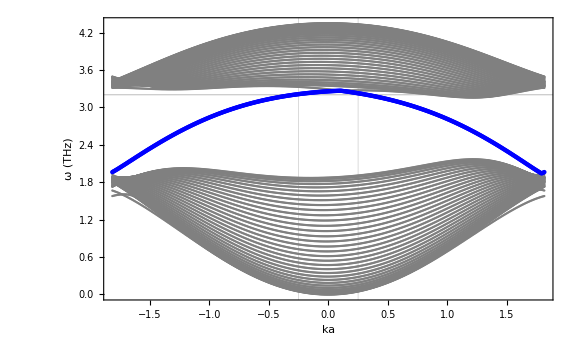

```mathematica
p=ListPlot[Dispersion,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Gray,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,GridLines->{{0.25,-0.25},{3.2,3.21}}];
p1=ListPlot[GetBand[35,Dispersion],LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"ka","ω (THz)"},PlotStyle->Directive[Blue,Thickness[.01]],PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,GridLines->{{0.25,-0.25},{3.2}}];
Show[p,p1]
```

## MZNR-SQ Coupling

### Wavefunction Algorithm (must run)

```mathematica
(*Calculate table of values*)
(*κ=0.3;
Δκ=0.05;*)

Naux=500;
Num=35;

upperbound=3.4;
lowerbound=1.8;

WaveAlgoZ[J_,J2_,DM_,s_,κ_,Δκ_,h_,ϕ_,Num_,Naux_,upperbound_,lowerbound_]:=
Module[{N0=Num,NBand=Naux,A},

(*diagonalizes hamiltonian eigensystem*)
Do[
ξ=-Pi/(√3)+j* N[(2 Pi/(√3))/Naux];

H=MZNRMatrix2N[J,J2,DM,s,κ,Δκ,h,ϕ,ξ,Num];
A=Eigensystem[H];

sortorder=Ordering[A[[1]]];

f[ξ]=Table[{ξ ,(A[[1]][[sortorder]][[i]])/(2Pi ℏ)},{i,1,2Num}];

,{j,0,Naux}];

(*Fun[l_]:=Table[f[ξ][[l]],{ξ,-Pi/3,Pi/3,N[(2 Pi/3)/Naux]}];*)

(*Iterates through table of values to grab indices which coincide to bands within desired bounds*)
FindIndices[NBand_,N0_,ub_,lb_]:=
Module[{EmptyList,Indices},
EmptyList={};

Do[
Do[
If[lb<Table[f[ξ][[i]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/NBand]}][[j]]<ub, AppendTo[EmptyList,i]]
,{j,1,Length[Table[f[ξ][[i]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/NBand]}]]}]
,{i,1,2N0}];

Indices=DeleteDuplicates[EmptyList];
Indices
];

BandIndices=FindIndices[Naux,Num,upperbound,lowerbound];

(*Find k value and corresponding band index for a fixed energy*)
FindMom[ω_,err_]:=
Module[{EmptyList,Mom},
EmptyList={};

Do[
Do[
If[ω-err<Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]]<ω+err, AppendTo[EmptyList,{BandIndices[[i]],Table[f[ξ][[BandIndices[[i]]]][[1]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]],Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}][[j]]}]]
,{j,1,Length[Table[f[ξ][[BandIndices[[i]]]][[2]],{ξ,-Pi/(√3),Pi/(√3),N[(2 Pi/(√3))/Naux]}]]}]
,{i,1,Length[BandIndices]}];

Mom=Sort[EmptyList,Abs[#1[[1]]]<Abs[#2[[1]]]&] (*Sorts list from smallest to largest absolute momentum*)
];

(*Takes the mean value of closely separated k values*)
MeanMom[ω_,err_]:=
Module[{MomList,DeleteMomList,EmptyList},

MomList=Split[FindMom[ω,err],Abs[#1[[2]]-#2[[2]]]<0.05&&#1[[1]]==#2[[1]]&];
EmptyList={};

For[i=1,i<Length[MomList]+1,i++,AppendTo[EmptyList,Mean[MomList[[i]]]]];

EmptyList
];

(*Calculates the wavefunction for spin lattice*)
wavefunctions[ω_,err_,N0]:=
Module[{wavefunction,U,f,k,band,β,n,y},
wavefunction={};

Do[
k=MeanMom[ω,err][[j]][[2]];
band=MeanMom[ω,err][[j]][[1]];
U=UMatrixMZNR[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
y=RecurrenceTable[{β[n+1]==β[n]+KroneckerDelta[0,Mod[n,2]]+1/2 KroneckerDelta[1,Mod[n,2]],β[1]==0},β,{n,1,2Num}];
f=Table[{y[[M]] *a/10^-9,Abs[U[[band]][[M]]]^2},{M,1,2Num}];
AppendTo[wavefunction,f]
,{j,1,Length[MeanMom[ω,err]]}];

wavefunction

];

];
```

```mathematica
Num=35;
NSamp=100;
κ=0;
Δκ=0.2;
WaveAlgoZ[J,J2,DM,s,κ,Δκ,h,ϕ,Num,NSamp,3.3,1.9];//AbsoluteTiming
```

{1.85544,Null}

### Wavefunctions

```mathematica
wf=wavefunctions[3.2,1/100,Num];
```

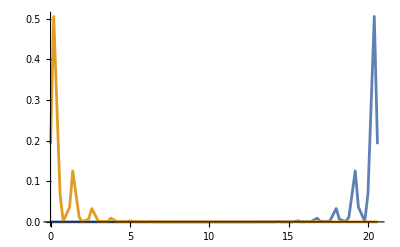

```mathematica
ListPlot[wf,Joined->True,PlotRange->All]
```

```mathematica
MomList=MeanMom[3.2,1/100];
k=MomList[[1]][[2]]
band=MomList[[1]][[1]]
```

0.308346

36

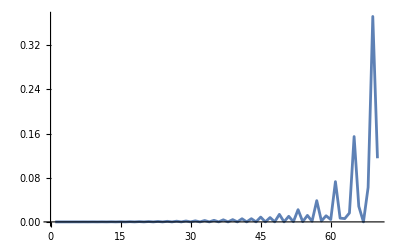

```mathematica
U=UMatrixMZNR[J,J2,DM,s,κ,Δκ,h,ϕ,0.31,Num];
ListPlot[Abs[U[[band]]]^2,Joined->True,PlotRange->All]
```

### Coupling Functions

```mathematica
ΓZ[x_,y_,z_,xlist_,ylist_,l_,N_]:=
Module[{gamma,xp,yp},
xp=xlist+√3 l;
yp=ylist;
gamma=-(3 (x-xp)^2)/(((x-xp)^2+(y-yp)^2+(z)^2)^(5/2))-(6 ⅈ (x-xp) (y-yp))/(((x-xp)^2+(y-yp)^2+(z)^2)^(5/2))+(3 (y-yp)^2)/(((x-xp)^2+(y-yp)^2+(z)^2)^(5/2))
];

gMZNR[ω_,k_,band_,U_,Numx_,Numy_,x_,y_,z_,xlist_,ylist_]:=
Module[{g,G,x1,y1,z1},
(*
Return value of dipole coupling for MANR-SQ interactions for a SQ placed at (x,y,z) with frequency ω; 
INPUTS;
ω: SQ frequency;
k: resonant magnon momentum, should be found via MeanMom[] or otherwise;
band: band index corresponding to resonant magnon momentum, should be found via MeanMom[] or otherwise;
U: unitary transformation matrix. Rows correspond to eigensates;
Numx: number of spins in x direction (non-periodic) for single species!;
Numy: number of unit cells in y direction (periodic, should be much greater than Numx);
x,y,z: coordinates of SQ;
xlist,ylist: vectors of size 2Numx corresponding to the positions of all points within the unit cell (x and y, respectively).
*)
(*g=Sum[Exp[ⅈ k R[l,m,2Numx][[2]]]*U[[band]][[m]]*Γ[x,y,z,l,m,2Numx],{m,1,2Numx},{l,-Numy/2,Numy/2}];*)
g=Sum[(Exp[ⅈ k (xlist+√3 l)]*U[[band]]).ΓZ[x,y,z,xlist,ylist,l,2Numy],{l,-Numx/2,Numx/2}];
g

];
```

#### Single Frequency

```mathematica
CouplingList={};
ω=3.15+κ/(2Pi ℏ);
MomList=MeanMom[ω,1/100];
(*If[Length[MomList]>2,MomList={Mean[MomList[[1;;Length[MomList]/2]]],Mean[MomList[[Length[MomList]/2+1;;Length[MomList]]]]}];*)
Do[
band=MomList[[j]][[1]];
k=MomList[[j]][[2]];
U=UMatrixMZNR[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
x=(√3)/4;
d=12.5;
NSteps=2*102;
Numx=250;
Rlist=Table[RZ[0,m,2Num],{m,1,2Num}];
xlist=Rlist[[All,1]];
ylist=Rlist[[All,2]];
g[y_]:=Module[{g},
g=Norm[gMZNR[ω,k,band,U,Numx,Num,x,y,d,xlist,ylist]];
g
];
Coupling=ParallelMap[g,Table[-25+2j*N[(3/2(Num-1))/NSteps],{j,0,NSteps}]];
AppendTo[CouplingList,Coupling]
,{j,1,Length[MomList]}];
```

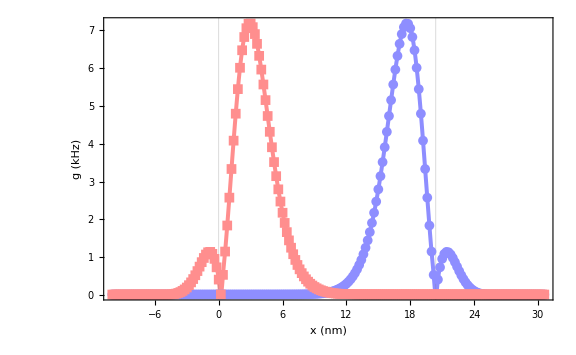

```mathematica
y=Table[-25+2j*N[(3/2(Num-1))/NSteps],{j,0,NSteps}]*0.4;
A=Sqrt[s/Numx] ((2 μB)^2 μ0)/(4 Sqrt[2] a^3 h)*10^-3;
ListPlot[Table[Table[{y[[i]],A*CouplingList[[j]][[i]]},{i,1,NSteps}],{j,1,Length[CouplingList]}],GridLines->{{0,3/2 (Num-1)*0.4},{}},Joined->True,InterpolationOrder->3,PlotMarkers->{Automatic,Medium},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"x (nm)","g (kHz)"},PlotStyle->{Directive[Lighter[Lighter[Blue]],Thickness[.005]],Directive[Lighter[Lighter[Red]],Thickness[.005]]},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
```

### Range of frequencies

```mathematica
CouplingList={};
Do[
ω=2.9+κ/(2Pi ℏ)+i;
MomList=MeanMom[ω,1/50];
If[Length[MomList]>2,MomList={Mean[MomList[[1;;Length[MomList]/2]]],Mean[MomList[[Length[MomList]/2+1;;Length[MomList]]]]}];
Do[
band=MomList[[j]][[1]];
k=MomList[[j]][[2]];
U=UMatrixMZNR[J,J2,DM,s,κ,Δκ,h,ϕ,k,Num];
x=0;
d=12.5;
NSteps=102;
Numx=300;
Rlist=Table[RZ[0,m,2Num],{m,1,2Num}];
xlist=Rlist[[All,1]];
ylist=Rlist[[All,2]];
g[y_]:=Module[{g},
g=Norm[gMZNR[ω,k,band,U,Numx,Num,x,y,d,xlist,ylist]];
g
];
Coupling=ParallelMap[g,Table[-15+j*N[(3/2(Num-1)+30)/NSteps],{j,0,NSteps}]];
AppendTo[CouplingList,Coupling]
,{j,1,Length[MomList]}];
,{i,0,0.3,0.025}];
```

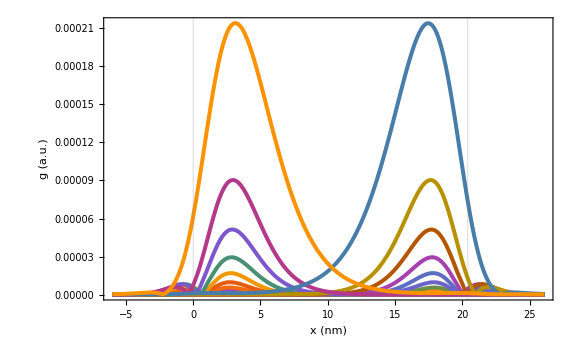

```mathematica
y=Table[-15+j*N[(3/2(Num-1)+30)/NSteps],{j,0,NSteps}]*0.4;
A=Sqrt[s/Numx] ((2 μB)^2 μ0)/(4 Sqrt[2] a^3 h)*10^-3;
ListPlot[Table[Table[{y[[i]],CouplingList[[j]][[i]]},{i,1,NSteps}],{j,1,Length[CouplingList]}],PlotRange->All,GridLines->{{0,3/2 (Num-1)*0.4},{}},Joined->True,InterpolationOrder->3,LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"x (nm)","g (a.u.)"},PlotStyle->{Directive[(*Lighter[Lighter[Blue]],*)Thickness[.005]]},PlotRange->All,PlotTheme->"Scientific",ImageSize->Large]
```

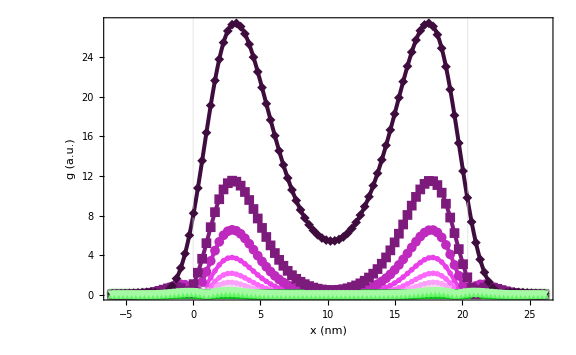

```mathematica
TotalCoupling=Table[Total[CouplingList[[2j-1;;2j]]],{j,1,Length[CouplingList]/2}];
Colors=Table[Directive[ColorData["GreenPinkTones",j/Length[TotalCoupling]],Thickness[.005]],{j,1,Length[CouplingList]/2}];
y=Table[-15+j*N[(3/2(Num-1)+30)/NSteps],{j,0,NSteps}]*0.4;
A=Sqrt[s/Numx] ((2 μB)^2 μ0)/(4 Sqrt[2] a^3 h)*10^-3;
ListPlot[Table[Table[{y[[i]],A*TotalCoupling[[j]][[i]]},{i,1,NSteps}],{j,1,Length[TotalCoupling]}],PlotRange->All,GridLines->{{0,3/2 (Num-1)*0.4},{}},Joined->True,InterpolationOrder->3,PlotMarkers->{Automatic,Medium},LabelStyle->Directive[Black,{FontFamily->"Latin Modern Roman",FontSize->20}],FrameLabel->{"x (nm)","g (a.u.)"},PlotStyle->Colors,PlotRange->All,PlotTheme->"Scientific",ImageSize->Large,FrameStyle->Thick,GridLinesStyle->Thick]
```

```mathematica
Colors=Table[Directive[ColorData["GreenPinkTones",j/Length[TotalCoupling]],Thickness[.005]],{j,1,Length[TotalCoupling]}];
ListLinePlot3D[A*TotalCoupling,PlotRange->All,PlotTheme->"Scientific",PlotStyle->Colors,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],Ticks->{{{2,-5},{50,10},{100,25}},{{1,2.9},{7,3.05},{13,3.2}},{0,25,50}},AxesStyle->Thick,AxesLabel->{"x (nm)","ω/2π (THz)","g (kHz)"},ImageSize->Large]
```

-Graphics3D-

```mathematica
SetDirectory["C:\\Users\\jeffc\\Documents\\topo_magnons\\MZNR-SQ_g_v_omega_d=15"];
CouplingListAll=Import[#]&/@FileNames[];
```

```mathematica
TotalCoupling=Table[Total[CouplingListAll[[j]]],{j,1,Length[CouplingListAll]}];
Colors=Table[Directive[ColorData["GreenPinkTones",j/Length[TotalCoupling]],Thickness[.005]],{j,1,Length[TotalCoupling]}];
Numy=300;
A=Sqrt[s/Numy] ((2 μB)^2 μ0)/(4 Sqrt[2] a^3 h)*10^-3;
ListLinePlot3D[A*TotalCoupling,PlotRange->All,PlotTheme->"Scientific",PlotStyle->Colors,LabelStyle->Directive[Black,{FontFamily->"Times New Roman",FontSize->24}],Ticks->{{{5,-10},{50,10},{100,30}},{{1,2.9},{15,3.05},{30,3.2}},{5,10,15,20}},AxesStyle->Thick,AxesLabel->{"x (nm)","ω/2π (THz)","g (kHz)"},ImageSize->Large,ViewPoint->{2.4,-2.4,1.}]
```

-Graphics3D-

```mathematica
CouplingListAll//Length
```

60

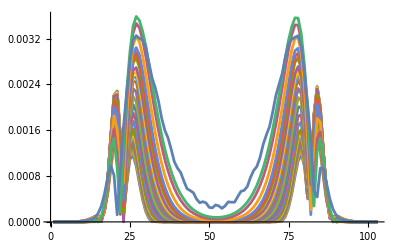

```mathematica
ListPlot[TotalCoupling,PlotRange->All,Joined->True]
```

```mathematica
Import["C:\\Users\\jeffc\\Documents\\topo_magnons\\MZNR-SQ_g_v_omega_d=6.25\\MZNR-SQ_g_d=6.25_omega=3.19.mx"]
```

{{7.18375×10^-8,7.18749×10^-8,7.1908×10^-8,7.19367×10^-8,7.19609×10^-8,7.19807×10^-8,7.1996×10^-8,7.20068×10^-8,7.20131×10^-8,7.20148×10^-8,7.20119×10^-8,7.20043×10^-8,7.19922×10^-8,7.19753×10^-8,7.19538×10^-8,7.19275×10^-8,7.18965×10^-8,7.18607×10^-8,7.18202×10^-8,7.17748×10^-8,7.17246×10^-8,7.16696×10^-8,7.16098×10^-8,7.1545×10^-8,7.14754×10^-8,7.14009×10^-8,7.13215×10^-8,7.12371×10^-8,7.11478×10^-8,7.10536×10^-8,7.09544×10^-8,7.08503×10^-8,7.07412×10^-8,7.06271×10^-8,7.0508×10^-8,7.0384×10^-8,7.02549×10^-8,7.01209×10^-8,6.99819×10^-8,6.98379×10^-8,6.96889×10^-8,6.95349×10^-8,6.9376×10^-8,6.92121×10^-8,6.90432×10^-8,6.88693×10^-8,6.86905×10^-8,6.85067×10^-8,6.83179×10^-8,6.81242×10^-8,6.79255×10^-8,6.77218×10^-8,6.75133×10^-8,6.72996×10^-8,6.70804×10^-8,6.68547×10^-8,6.66203×10^-8,6.63737×10^-8,6.61092×10^-8,6.58184×10^-8,6.54893×10^-8,6.51029×10^-8,6.46271×10^-8,6.4004×10^-8,6.31333×10^-8,6.18747×10^-8,6.01551×10^-8,5.84444×10^-8,5.91296×10^-8,6.83904×10^-8,9.39519×10^-8,1.39015×10^-7,2.01854×10^-7,2.76865×10^-7,3.53684×10^-7,4.16888×10^-7,4.47866×10^-7,4.29147×10^-7,3.50424×10^-7,2.14857×10^-7,6.09414×10^-8,1.75306×10^-7,3.44785×10^-7,4.68938×10^-7,5.30053×10^-7,5.28493×10^-7,4.78157×10^-7,3.99626×10^-7,3.13072×10^-7,2.33499×10^-7,1.69182×10^-7,1.22546×10^-7,9.20511×10^-8,7.4018×10^-8,6.41873×10^-8,5.90225×10^-8,5.62614×10^-8,5.46896×10^-8,5.37045×10^-8,5.30111×10^-8,5.24626×10^-8,5.19849×10^-8,5.15407×10^-8},{5.12192×10^-8,5.16135×10^-8,5.19851×10^-8,5.23142×10^-8,5.25634×10^-8,5.26682×10^-8,5.25313×10^-8,5.20538×10^-8,5.13126×10^-8,5.11792×10^-8,5.47972×10^-8,6.86718×10^-8,9.94082×10^-8,1.49768×10^-7,2.18853×10^-7,3.01521×10^-7,3.86663×10^-7,4.5687×10^-7,4.91042×10^-7,4.70182×10^-7,3.84777×10^-7,2.41088×10^-7,7.42715×10^-8,1.54176×10^-7,3.16703×10^-7,4.33307×10^-7,4.89644×10^-7,4.88468×10^-7,4.43503×10^-7,3.73248×10^-7,2.95397×10^-7,2.23294×10^-7,1.64729×10^-7,1.22442×10^-7,9.5365×10^-8,8.00166×10^-8,7.21736×10^-8,6.84277×10^-8,6.67133×10^-8,6.59732×10^-8,6.57024×10^-8,6.56629×10^-8,6.57426×10^-8,6.58875×10^-8,6.60699×10^-8,6.62741×10^-8,6.64901×10^-8,6.6711×10^-8,6.69325×10^-8,6.71517×10^-8,6.73673×10^-8,6.75783×10^-8,6.77847×10^-8,6.79862×10^-8,6.81828×10^-8,6.83745×10^-8,6.85614×10^-8,6.87434×10^-8,6.89204×10^-8,6.90924×10^-8,6.92596×10^-8,6.94217×10^-8,6.95789×10^-8,6.9731×10^-8,6.98782×10^-8,7.00204×10^-8,7.01577×10^-8,7.02899×10^-8,7.04171×10^-8,7.05394×10^-8,7.06567×10^-8,7.0769×10^-8,7.08763×10^-8,7.09787×10^-8,7.10761×10^-8,7.11686×10^-8,7.12561×10^-8,7.13387×10^-8,7.14163×10^-8,7.14891×10^-8,7.1557×10^-8,7.162×10^-8,7.16781×10^-8,7.17314×10^-8,7.17798×10^-8,7.18235×10^-8,7.18623×10^-8,7.18964×10^-8,7.19257×10^-8,7.19503×10^-8,7.19701×10^-8,7.19853×10^-8,7.19958×10^-8,7.20017×10^-8,7.2003×10^-8,7.19997×10^-8,7.19918×10^-8,7.19794×10^-8,7.19625×10^-8,7.19411×10^-8,7.19153×10^-8,7.18851×10^-8,7.18504×10^-8},{2.19031×10^-8,2.23602×10^-8,2.28185×10^-8,2.3278×10^-8,2.37386×10^-8,2.42004×10^-8,2.46632×10^-8,2.5127×10^-8,2.55918×10^-8,2.60574×10^-8,2.65238×10^-8,2.69911×10^-8,2.7459×10^-8,2.79276×10^-8,2.83967×10^-8,2.88665×10^-8,2.93367×10^-8,2.98073×10^-8,3.02782×10^-8,3.07495×10^-8,3.1221×10^-8,3.16927×10^-8,3.21645×10^-8,3.26363×10^-8,3.31082×10^-8,3.35799×10^-8,3.40516×10^-8,3.4523×10^-8,3.49941×10^-8,3.5465×10^-8,3.59354×10^-8,3.64054×10^-8,3.68748×10^-8,3.73437×10^-8,3.78119×10^-8,3.82794×10^-8,3.87461×10^-8,3.92119×10^-8,3.96769×10^-8,4.01408×10^-8,4.06037×10^-8,4.10655×10^-8,4.1526×10^-8,4.19854×10^-8,4.24434×10^-8,4.29×10^-8,4.33551×10^-8,4.38087×10^-8,4.42607×10^-8,4.4711×10^-8,4.51595×10^-8,4.56061×10^-8,4.60507×10^-8,4.64928×10^-8,4.69318×10^-8,4.73663×10^-8,4.77937×10^-8,4.82098×10^-8,4.86079×10^-8,4.89779×10^-8,4.93042×10^-8,4.95626×10^-8,4.97134×10^-8,4.96946×10^-8,4.94297×10^-8,4.89112×10^-8,4.85537×10^-8,5.02221×10^-8,5.88097×10^-8,8.12773×10^-8,1.22321×10^-7,1.83264×10^-7,2.62404×10^-7,3.53631×10^-7,4.44899×10^-7,5.1818×10^-7,5.5189×10^-7,5.26028×10^-7,4.29096×10^-7,2.64915×10^-7,6.9546×10^-8,1.93337×10^-7,3.95341×10^-7,5.43101×10^-7,6.16617×10^-7,6.16431×10^-7,5.58719×10^-7,4.67449×10^-7,3.662×10^-7,2.72638×10^-7,1.96661×10^-7,1.41383×10^-7,1.05289×10^-7,8.42564×10^-8,7.32538×10^-8,6.79423×10^-8,6.55115×10^-8,6.44717×10^-8,6.41038×10^-8,6.40651×10^-8,6.41885×10^-8,6.43908×10^-8,6.46298×10^-8},{6.47314×10^-8,6.44322×10^-8,6.41022×10^-8,6.37157×10^-8,6.32248×10^-8,6.25478×10^-8,6.15639×10^-8,6.01591×10^-8,5.8471×10^-8,5.77297×10^-8,6.21723×10^-8,7.98999×10^-8,1.18049×10^-7,1.79044×10^-7,2.61531×10^-7,3.59362×10^-7,4.59446×10^-7,5.41395×10^-7,5.80607×10^-7,5.54974×10^-7,4.5336×10^-7,2.82604×10^-7,7.92006×10^-8,1.7845×10^-7,3.74209×10^-7,5.15126×10^-7,5.85006×10^-7,5.86569×10^-7,5.35321×10^-7,4.52584×10^-7,3.59045×10^-7,2.70544×10^-7,1.96561×10^-7,1.40774×10^-7,1.02648×10^-7,7.90868×10^-8,6.58348×10^-8,5.88167×10^-8,5.51057×10^-8,5.30263×10^-8,5.1739×10^-8,5.08441×10^-8,5.01511×10^-8,4.95678×10^-8,4.90468×10^-8,4.85625×10^-8,4.80994×10^-8,4.76481×10^-8,4.72024×10^-8,4.67588×10^-8,4.63151×10^-8,4.58703×10^-8,4.54241×10^-8,4.49761×10^-8,4.45265×10^-8,4.40753×10^-8,4.36225×10^-8,4.31681×10^-8,4.27123×10^-8,4.22551×10^-8,4.17965×10^-8,4.13366×10^-8,4.08755×10^-8,4.04132×10^-8,3.99498×10^-8,3.94854×10^-8,3.902×10^-8,3.85537×10^-8,3.80866×10^-8,3.76188×10^-8,3.71502×10^-8,3.6681×10^-8,3.62112×10^-8,3.5741×10^-8,3.52702×10^-8,3.47992×10^-8,3.43278×10^-8,3.38561×10^-8,3.33843×10^-8,3.29123×10^-8,3.24403×10^-8,3.19684×10^-8,3.14964×10^-8,3.10246×10^-8,3.05531×10^-8,3.00817×10^-8,2.96107×10^-8,2.914×10^-8,2.86698×10^-8,2.82001×10^-8,2.77309×10^-8,2.72624×10^-8,2.67945×10^-8,2.63273×10^-8,2.58609×10^-8,2.53953×10^-8,2.49307×10^-8,2.4467×10^-8,2.40043×10^-8,2.35426×10^-8,2.30821×10^-8,2.26227×10^-8,2.21645×10^-8},{7.13181×10^-8,7.1341×10^-8,7.13594×10^-8,7.13734×10^-8,7.13829×10^-8,7.13879×10^-8,7.13883×10^-8,7.13843×10^-8,7.13756×10^-8,7.13623×10^-8,7.13444×10^-8,7.13218×10^-8,7.12946×10^-8,7.12626×10^-8,7.1226×10^-8,7.11845×10^-8,7.11383×10^-8,7.10873×10^-8,7.10316×10^-8,7.0971×10^-8,7.09055×10^-8,7.08352×10^-8,7.076×10^-8,7.068×10^-8,7.0595×10^-8,7.05051×10^-8,7.04104×10^-8,7.03107×10^-8,7.0206×10^-8,7.00964×10^-8,6.99819×10^-8,6.98624×10^-8,6.97379×10^-8,6.96085×10^-8,6.94741×10^-8,6.93347×10^-8,6.91903×10^-8,6.9041×10^-8,6.88867×10^-8,6.87274×10^-8,6.85632×10^-8,6.8394×10^-8,6.82199×10^-8,6.80408×10^-8,6.78568×10^-8,6.76679×10^-8,6.7474×10^-8,6.72753×10^-8,6.70718×10^-8,6.68634×10^-8,6.66503×10^-8,6.64327×10^-8,6.62106×10^-8,6.59847×10^-8,6.57561×10^-8,6.55268×10^-8,6.53004×10^-8,6.50831×10^-8,6.48849×10^-8,6.47223×10^-8,6.46232×10^-8,6.4637×10^-8,6.48568×10^-8,6.54657×10^-8,6.68366×10^-8,6.9738×10^-8,7.57127×10^-8,8.75662×10^-8,1.09515×10^-7,1.46447×10^-7,2.02582×10^-7,2.8007×10^-7,3.77323×10^-7,4.87064×10^-7,5.94891×10^-7,6.79543×10^-7,7.15935×10^-7,6.81188×10^-7,5.62533×10^-7,3.64652×10^-7,1.17931×10^-7,1.7552×10^-7,4.1389×10^-7,5.88818×10^-7,6.76605×10^-7,6.7788×10^-7,6.11392×10^-7,5.04968×10^-7,3.86093×10^-7,2.75497×10^-7,1.85036×10^-7,1.18998×10^-7,7.69912×10^-8,5.59117×10^-8,4.91982×10^-8,4.86718×10^-8,4.9504×10^-8,5.01699×10^-8,5.04441×10^-8,5.04183×10^-8,5.0208×10^-8,4.98945×10^-8,4.95256×10^-8},{4.93154×10^-8,4.97681×10^-8,5.02513×10^-8,5.07987×10^-8,5.14788×10^-8,5.24304×10^-8,5.39433×10^-8,5.66378×10^-8,6.1831×10^-8,7.20922×10^-8,9.15885×10^-8,1.25563×10^-7,1.791×10^-7,2.55678×10^-7,3.55166×10^-7,4.71149×10^-7,5.88637×10^-7,6.8398×10^-7,7.2863×10^-7,6.96954×10^-7,5.75991×10^-7,3.73241×10^-7,1.22961×10^-7,1.69502×10^-7,4.02758×10^-7,5.72744×10^-7,6.59513×10^-7,6.65465×10^-7,6.08047×10^-7,5.11833×10^-7,4.01081×10^-7,2.948×10^-7,2.049×10^-7,1.36884×10^-7,9.18381×10^-8,6.78604×10^-8,5.93539×10^-8,5.8409×10^-8,5.96538×10^-8,6.10602×10^-8,6.21675×10^-8,6.29793×10^-8,6.35822×10^-8,6.40499×10^-8,6.44317×10^-8,6.47585×10^-8,6.50498×10^-8,6.53178×10^-8,6.55704×10^-8,6.58123×10^-8,6.60464×10^-8,6.62742×10^-8,6.64964×10^-8,6.67133×10^-8,6.69253×10^-8,6.71323×10^-8,6.73343×10^-8,6.75314×10^-8,6.77235×10^-8,6.79107×10^-8,6.8093×10^-8,6.82703×10^-8,6.84426×10^-8,6.861×10^-8,6.87725×10^-8,6.893×10^-8,6.90825×10^-8,6.923×10^-8,6.93726×10^-8,6.95102×10^-8,6.96428×10^-8,6.97705×10^-8,6.98932×10^-8,7.00109×10^-8,7.01237×10^-8,7.02315×10^-8,7.03344×10^-8,7.04324×10^-8,7.05254×10^-8,7.06135×10^-8,7.06967×10^-8,7.0775×10^-8,7.08485×10^-8,7.0917×10^-8,7.09808×10^-8,7.10396×10^-8,7.10937×10^-8,7.1143×10^-8,7.11875×10^-8,7.12272×10^-8,7.12622×10^-8,7.12925×10^-8,7.13181×10^-8,7.1339×10^-8,7.13553×10^-8,7.13669×10^-8,7.1374×10^-8,7.13764×10^-8,7.13744×10^-8,7.13678×10^-8,7.13567×10^-8,7.13411×10^-8,7.13211×10^-8},{2.42533×10^-8,2.47127×10^-8,2.51732×10^-8,2.56348×10^-8,2.60974×10^-8,2.6561×10^-8,2.70254×10^-8,2.74907×10^-8,2.79568×10^-8,2.84236×10^-8,2.88911×10^-8,2.93593×10^-8,2.98279×10^-8,3.02971×10^-8,3.07667×10^-8,3.12367×10^-8,3.17071×10^-8,3.21777×10^-8,3.26485×10^-8,3.31194×10^-8,3.35904×10^-8,3.40614×10^-8,3.45324×10^-8,3.50033×10^-8,3.5474×10^-8,3.59445×10^-8,3.64147×10^-8,3.68845×10^-8,3.73539×10^-8,3.78228×10^-8,3.82911×10^-8,3.87588×10^-8,3.92259×10^-8,3.96921×10^-8,4.01576×10^-8,4.06222×10^-8,4.10858×10^-8,4.15484×10^-8,4.20099×10^-8,4.24703×10^-8,4.29294×10^-8,4.33873×10^-8,4.38438×10^-8,4.42989×10^-8,4.47526×10^-8,4.52046×10^-8,4.56551×10^-8,4.6104×10^-8,4.65512×10^-8,4.69966×10^-8,4.74405×10^-8,4.78827×10^-8,4.83238×10^-8,4.87642×10^-8,4.92054×10^-8,4.96498×10^-8,5.01019×10^-8,5.05691×10^-8,5.10643×10^-8,5.16094×10^-8,5.2243×10^-8,5.3037×10^-8,5.41312×10^-8,5.58095×10^-8,5.86649×10^-8,6.39176×10^-8,7.38879×10^-8,9.2326×10^-8,1.24088×10^-7,1.74216×10^-7,2.46874×10^-7,3.4394×10^-7,4.62949×10^-7,5.9477×10^-7,7.22056×10^-7,8.19751×10^-7,8.58777×10^-7,8.13073×10^-7,6.68636×10^-7,4.3172×10^-7,1.36974×10^-7,2.04463×10^-7,4.86662×10^-7,6.93449×10^-7,7.98061×10^-7,8.01317×10^-7,7.24936×10^-7,6.01209×10^-7,4.62153×10^-7,3.32087×10^-7,2.25098×10^-7,1.46465×10^-7,9.59372×10^-8,7.00469×10^-8,6.14383×10^-8,6.07287×10^-8,6.20632×10^-8,6.34264×10^-8,6.4431×10^-8,6.51274×10^-8,6.56264×10^-8,6.60118×10^-8,6.63346×10^-8},{6.65734×10^-8,6.63524×10^-8,6.61704×10^-8,6.60717×10^-8,6.6144×10^-8,6.65637×10^-8,6.76945×10^-8,7.03054×10^-8,7.60101×10^-8,8.79162×10^-8,1.10984×10^-7,1.51339×10^-7,2.14789×10^-7,3.05171×10^-7,4.2205×10^-7,5.57648×10^-7,6.94256×10^-7,8.04217×10^-7,8.5433×10^-7,8.14883×10^-7,6.70849×10^-7,4.30763×10^-7,1.33309×10^-7,2.07243×10^-7,4.86919×10^-7,6.92016×10^-7,7.99636×10^-7,8.11751×10^-7,7.47892×10^-7,6.36239×10^-7,5.0505×10^-7,3.76803×10^-7,2.65812×10^-7,1.78708×10^-7,1.16587×10^-7,7.74932×10^-8,5.76416×10^-8,5.07539×10^-8,4.97247×10^-8,5.02704×10^-8,5.08711×10^-8,5.11982×10^-8,5.12656×10^-8,5.11478×10^-8,5.0909×10^-8,5.05934×10^-8,5.02297×10^-8,4.98362×10^-8,4.94243×10^-8,4.90011×10^-8,4.85707×10^-8,4.81355×10^-8,4.76969×10^-8,4.72555×10^-8,4.68119×10^-8,4.63663×10^-8,4.59187×10^-8,4.54693×10^-8,4.50182×10^-8,4.45656×10^-8,4.41113×10^-8,4.36556×10^-8,4.31985×10^-8,4.27401×10^-8,4.22804×10^-8,4.18195×10^-8,4.13575×10^-8,4.08944×10^-8,4.04304×10^-8,3.99654×10^-8,3.94995×10^-8,3.90328×10^-8,3.85654×10^-8,3.80974×10^-8,3.76287×10^-8,3.71595×10^-8,3.66899×10^-8,3.62198×10^-8,3.57494×10^-8,3.52787×10^-8,3.48078×10^-8,3.43367×10^-8,3.38656×10^-8,3.33944×10^-8,3.29233×10^-8,3.24522×10^-8,3.19814×10^-8,3.15107×10^-8,3.10403×10^-8,3.05703×10^-8,3.01007×10^-8,2.96315×10^-8,2.91628×10^-8,2.86947×10^-8,2.82273×10^-8,2.77605×10^-8,2.72945×10^-8,2.68293×10^-8,2.6365×10^-8,2.59015×10^-8,2.5439×10^-8,2.49776×10^-8,2.45172×10^-8},{2.42533×10^-8,2.47127×10^-8,2.51732×10^-8,2.56348×10^-8,2.60974×10^-8,2.6561×10^-8,2.70254×10^-8,2.74907×10^-8,2.79568×10^-8,2.84236×10^-8,2.88911×10^-8,2.93593×10^-8,2.98279×10^-8,3.02971×10^-8,3.07667×10^-8,3.12367×10^-8,3.17071×10^-8,3.21777×10^-8,3.26485×10^-8,3.31194×10^-8,3.35904×10^-8,3.40614×10^-8,3.45324×10^-8,3.50033×10^-8,3.5474×10^-8,3.59445×10^-8,3.64147×10^-8,3.68845×10^-8,3.73539×10^-8,3.78228×10^-8,3.82911×10^-8,3.87588×10^-8,3.92259×10^-8,3.96921×10^-8,4.01576×10^-8,4.06222×10^-8,4.10858×10^-8,4.15484×10^-8,4.20099×10^-8,4.24703×10^-8,4.29294×10^-8,4.33873×10^-8,4.38438×10^-8,4.42989×10^-8,4.47526×10^-8,4.52046×10^-8,4.56551×10^-8,4.6104×10^-8,4.65512×10^-8,4.69966×10^-8,4.74405×10^-8,4.78827×10^-8,4.83238×10^-8,4.87642×10^-8,4.92054×10^-8,4.96498×10^-8,5.01019×10^-8,5.05691×10^-8,5.10643×10^-8,5.16094×10^-8,5.2243×10^-8,5.3037×10^-8,5.41312×10^-8,5.58095×10^-8,5.86649×10^-8,6.39176×10^-8,7.38879×10^-8,9.2326×10^-8,1.24088×10^-7,1.74216×10^-7,2.46874×10^-7,3.4394×10^-7,4.62949×10^-7,5.9477×10^-7,7.22056×10^-7,8.19751×10^-7,8.58777×10^-7,8.13073×10^-7,6.68636×10^-7,4.3172×10^-7,1.36974×10^-7,2.04463×10^-7,4.86662×10^-7,6.93449×10^-7,7.98061×10^-7,8.01317×10^-7,7.24936×10^-7,6.01209×10^-7,4.62153×10^-7,3.32087×10^-7,2.25098×10^-7,1.46465×10^-7,9.59372×10^-8,7.00469×10^-8,6.14383×10^-8,6.07287×10^-8,6.20632×10^-8,6.34264×10^-8,6.4431×10^-8,6.51274×10^-8,6.56264×10^-8,6.60118×10^-8,6.63346×10^-8},{6.65734×10^-8,6.63524×10^-8,6.61704×10^-8,6.60717×10^-8,6.6144×10^-8,6.65637×10^-8,6.76945×10^-8,7.03054×10^-8,7.60101×10^-8,8.79162×10^-8,1.10984×10^-7,1.51339×10^-7,2.14789×10^-7,3.05171×10^-7,4.2205×10^-7,5.57648×10^-7,6.94256×10^-7,8.04217×10^-7,8.5433×10^-7,8.14883×10^-7,6.70849×10^-7,4.30763×10^-7,1.33309×10^-7,2.07243×10^-7,4.86919×10^-7,6.92016×10^-7,7.99636×10^-7,8.11751×10^-7,7.47892×10^-7,6.36239×10^-7,5.0505×10^-7,3.76803×10^-7,2.65812×10^-7,1.78708×10^-7,1.16587×10^-7,7.74932×10^-8,5.76416×10^-8,5.07539×10^-8,4.97247×10^-8,5.02704×10^-8,5.08711×10^-8,5.11982×10^-8,5.12656×10^-8,5.11478×10^-8,5.0909×10^-8,5.05934×10^-8,5.02297×10^-8,4.98362×10^-8,4.94243×10^-8,4.90011×10^-8,4.85707×10^-8,4.81355×10^-8,4.76969×10^-8,4.72555×10^-8,4.68119×10^-8,4.63663×10^-8,4.59187×10^-8,4.54693×10^-8,4.50182×10^-8,4.45656×10^-8,4.41113×10^-8,4.36556×10^-8,4.31985×10^-8,4.27401×10^-8,4.22804×10^-8,4.18195×10^-8,4.13575×10^-8,4.08944×10^-8,4.04304×10^-8,3.99654×10^-8,3.94995×10^-8,3.90328×10^-8,3.85654×10^-8,3.80974×10^-8,3.76287×10^-8,3.71595×10^-8,3.66899×10^-8,3.62198×10^-8,3.57494×10^-8,3.52787×10^-8,3.48078×10^-8,3.43367×10^-8,3.38656×10^-8,3.33944×10^-8,3.29233×10^-8,3.24522×10^-8,3.19814×10^-8,3.15107×10^-8,3.10403×10^-8,3.05703×10^-8,3.01007×10^-8,2.96315×10^-8,2.91628×10^-8,2.86947×10^-8,2.82273×10^-8,2.77605×10^-8,2.72945×10^-8,2.68293×10^-8,2.6365×10^-8,2.59015×10^-8,2.5439×10^-8,2.49776×10^-8,2.45172×10^-8},{7.08612×10^-8,7.08693×10^-8,7.0873×10^-8,7.08721×10^-8,7.08667×10^-8,7.08568×10^-8,7.08423×10^-8,7.08232×10^-8,7.07994×10^-8,7.0771×10^-8,7.07379×10^-8,7.07002×10^-8,7.06577×10^-8,7.06104×10^-8,7.05584×10^-8,7.05016×10^-8,7.04401×10^-8,7.03737×10^-8,7.03024×10^-8,7.02264×10^-8,7.01454×10^-8,7.00596×10^-8,6.99689×10^-8,6.98733×10^-8,6.97728×10^-8,6.96673×10^-8,6.9557×10^-8,6.94417×10^-8,6.93214×10^-8,6.91962×10^-8,6.9066×10^-8,6.89309×10^-8,6.87908×10^-8,6.86458×10^-8,6.84957×10^-8,6.83408×10^-8,6.81808×10^-8,6.80159×10^-8,6.7846×10^-8,6.76712×10^-8,6.74915×10^-8,6.73068×10^-8,6.71171×10^-8,6.69226×10^-8,6.67231×10^-8,6.65187×10^-8,6.63093×10^-8,6.6095×10^-8,6.58758×10^-8,6.56514×10^-8,6.54218×10^-8,6.51867×10^-8,6.49453×10^-8,6.46966×10^-8,6.44383×10^-8,6.41666×10^-8,6.38749×10^-8,6.35523×10^-8,6.31811×10^-8,6.27332×10^-8,6.21654×10^-8,6.14169×10^-8,6.04198×10^-8,5.91672×10^-8,5.79677×10^-8,5.82052×10^-8,6.38662×10^-8,8.21522×10^-8,1.20275×10^-7,1.83035×10^-7,2.73615×10^-7,3.92878×10^-7,5.36845×10^-7,6.93895×10^-7,8.43066×10^-7,9.54829×10^-7,9.95525×10^-7,9.35539×10^-7,7.59607×10^-7,4.75931×10^-7,1.25241×10^-7,2.71081×10^-7,6.06333×10^-7,8.51043×10^-7,9.75971×10^-7,9.8224×10^-7,8.94953×10^-7,7.51465×10^-7,5.889×10^-7,4.35523×10^-7,3.07607×10^-7,2.10774×10^-7,1.43487×10^-7,1.00586×10^-7,7.56768×10^-8,6.24743×10^-8,5.5855×10^-8,5.2509×10^-8,5.06953×10^-8,4.95967×10^-8,4.88392×10^-8,4.82475×10^-8,4.77365×10^-8},{4.73244×10^-8,4.77067×10^-8,4.80357×10^-8,4.82659×10^-8,4.83217×10^-8,4.8101×10^-8,4.75499×10^-8,4.70094×10^-8,4.83462×10^-8,5.70626×10^-8,8.18692×10^-8,1.29955×10^-7,2.06242×10^-7,3.13948×10^-7,4.51976×10^-7,6.10939×10^-7,7.7002×10^-7,8.96989×10^-7,9.53346×10^-7,9.04737×10^-7,7.338×10^-7,4.50312×10^-7,1.01269×10^-7,2.97489×10^-7,6.32498×10^-7,8.79302×10^-7,1.0121×10^-6,1.03227×10^-6,9.61596×10^-7,8.32337×10^-7,6.77379×10^-7,5.23351×10^-7,3.87612×10^-7,2.78491×10^-7,1.9742×10^-7,1.41586×10^-7,1.06105×10^-7,8.54219×10^-8,7.42893×10^-8,6.86185×10^-8,6.58123×10^-8,6.44583×10^-8,6.38461×10^-8,6.36237×10^-8,6.36125×10^-8,6.37184×10^-8,6.38896×10^-8,6.40966×10^-8,6.43223×10^-8,6.45567×10^-8,6.47939×10^-8,6.50304×10^-8,6.52643×10^-8,6.54946×10^-8,6.57208×10^-8,6.59424×10^-8,6.61594×10^-8,6.63717×10^-8,6.65791×10^-8,6.67817×10^-8,6.69794×10^-8,6.71722×10^-8,6.736×10^-8,6.7543×10^-8,6.7721×10^-8,6.7894×10^-8,6.80621×10^-8,6.82253×10^-8,6.83834×10^-8,6.85366×10^-8,6.86849×10^-8,6.88282×10^-8,6.89665×10^-8,6.90999×10^-8,6.92283×10^-8,6.93517×10^-8,6.94702×10^-8,6.95838×10^-8,6.96924×10^-8,6.97961×10^-8,6.98948×10^-8,6.99887×10^-8,7.00777×10^-8,7.01618×10^-8,7.0241×10^-8,7.03153×10^-8,7.03848×10^-8,7.04495×10^-8,7.05094×10^-8,7.05645×10^-8,7.06148×10^-8,7.06603×10^-8,7.07012×10^-8,7.07373×10^-8,7.07687×10^-8,7.07955×10^-8,7.08176×10^-8,7.0835×10^-8,7.08479×10^-8,7.08563×10^-8,7.08601×10^-8,7.08593×10^-8,7.08541×10^-8},{2.66543×10^-8,2.71166×10^-8,2.75798×10^-8,2.80439×10^-8,2.85089×10^-8,2.89747×10^-8,2.94413×10^-8,2.99086×10^-8,3.03765×10^-8,3.0845×10^-8,3.1314×10^-8,3.17835×10^-8,3.22533×10^-8,3.27236×10^-8,3.31941×10^-8,3.36649×10^-8,3.41358×10^-8,3.46068×10^-8,3.50779×10^-8,3.55489×10^-8,3.60199×10^-8,3.64908×10^-8,3.69614×10^-8,3.74318×10^-8,3.79018×10^-8,3.83714×10^-8,3.88406×10^-8,3.93092×10^-8,3.97773×10^-8,4.02447×10^-8,4.07114×10^-8,4.11773×10^-8,4.16423×10^-8,4.21064×10^-8,4.25695×10^-8,4.30316×10^-8,4.34926×10^-8,4.39523×10^-8,4.44108×10^-8,4.4868×10^-8,4.53239×10^-8,4.57782×10^-8,4.6231×10^-8,4.66823×10^-8,4.71318×10^-8,4.75797×10^-8,4.80256×10^-8,4.84696×10^-8,4.89115×10^-8,4.93511×10^-8,4.97881×10^-8,5.02218×10^-8,5.06513×10^-8,5.1075×10^-8,5.149×10^-8,5.18914×10^-8,5.2271×10^-8,5.26157×10^-8,5.29048×10^-8,5.31074×10^-8,5.31826×10^-8,5.30928×10^-8,5.2862×10^-8,5.27763×10^-8,5.39444×10^-8,5.94296×10^-8,7.5028×10^-8,1.07558×10^-7,1.6279×10^-7,2.457×10^-7,3.60202×10^-7,5.07101×10^-7,6.81094×10^-7,8.67794×10^-7,1.04208×10^-6,1.16931×10^-6,1.21067×10^-6,1.13266×10^-6,9.18821×10^-7,5.79874×10^-7,1.62275×10^-7,3.02218×10^-7,6.97248×10^-7,9.86229×10^-7,1.13542×10^-6,1.1461×10^-6,1.04722×10^-6,8.81949×10^-7,6.93397×10^-7,5.1461×10^-7,3.64894×10^-7,2.51241×10^-7,1.72293×10^-7,1.22336×10^-7,9.39499×10^-8,7.95481×10^-8,7.28625×10^-8,6.9912×10^-8,6.86662×10^-8,6.82007×10^-8,6.81029×10^-8,6.81822×10^-8,6.8347×10^-8},{6.83426×10^-8,6.80256×10^-8,6.76364×10^-8,6.71152×10^-8,6.63617×10^-8,6.52357×10^-8,6.36361×10^-8,6.18908×10^-8,6.20785×10^-8,7.07389×10^-8,9.88226×10^-8,1.55229×10^-7,2.45299×10^-7,3.72192×10^-7,5.34104×10^-7,7.19656×10^-7,9.04319×10^-7,1.05053×10^-6,1.11366×10^-6,1.05406×10^-6,8.51717×10^-7,5.17848×10^-7,1.06919×10^-7,3.61755×10^-7,7.59514×10^-7,1.05523×10^-6,1.21818×10^-6,1.24864×10^-6,1.17078×10^-6,1.02136×10^-6,8.38564×10^-7,6.53867×10^-7,4.88332×10^-7,3.526×10^-7,2.49151×10^-7,1.75302×10^-7,1.25862×10^-7,9.49141×10^-8,7.67941×10^-8,6.6705×10^-8,6.11671×10^-8,5.80406×10^-8,5.61631×10^-8,5.49392×10^-8,5.40666×10^-8,5.33876×10^-8,5.28173×10^-8,5.23086×10^-8,5.18344×10^-8,5.1379×10^-8,5.09333×10^-8,5.04922×10^-8,5.00527×10^-8,4.96131×10^-8,4.91725×10^-8,4.87306×10^-8,4.8287×10^-8,4.78418×10^-8,4.73948×10^-8,4.69462×10^-8,4.64958×10^-8,4.60439×10^-8,4.55904×10^-8,4.51354×10^-8,4.4679×10^-8,4.42213×10^-8,4.37622×10^-8,4.33019×10^-8,4.28404×10^-8,4.23779×10^-8,4.19143×10^-8,4.14498×10^-8,4.09843×10^-8,4.05181×10^-8,4.0051×10^-8,3.95833×10^-8,3.91149×10^-8,3.8646×10^-8,3.81765×10^-8,3.77066×10^-8,3.72364×10^-8,3.67658×10^-8,3.6295×10^-8,3.5824×10^-8,3.53528×10^-8,3.48816×10^-8,3.44105×10^-8,3.39393×10^-8,3.34683×10^-8,3.29975×10^-8,3.2527×10^-8,3.20567×10^-8,3.15868×10^-8,3.11173×10^-8,3.06483×10^-8,3.01799×10^-8,2.97121×10^-8,2.92449×10^-8,2.87784×10^-8,2.83127×10^-8,2.78478×10^-8,2.73838×10^-8,2.69207×10^-8},{7.04764×10^-8,7.04696×10^-8,7.04582×10^-8,7.04423×10^-8,7.04218×10^-8,7.03967×10^-8,7.0367×10^-8,7.03326×10^-8,7.02935×10^-8,7.02498×10^-8,7.02013×10^-8,7.0148×10^-8,7.009×10^-8,7.00272×10^-8,6.99596×10^-8,6.98872×10^-8,6.981×10^-8,6.97278×10^-8,6.96409×10^-8,6.9549×10^-8,6.94523×10^-8,6.93506×10^-8,6.92441×10^-8,6.91326×10^-8,6.90162×10^-8,6.88948×10^-8,6.87685×10^-8,6.86373×10^-8,6.8501×10^-8,6.83598×10^-8,6.82137×10^-8,6.80626×10^-8,6.79065×10^-8,6.77455×10^-8,6.75794×10^-8,6.74085×10^-8,6.72325×10^-8,6.70516×10^-8,6.68658×10^-8,6.6675×10^-8,6.64793×10^-8,6.62787×10^-8,6.60732×10^-8,6.58628×10^-8,6.56475×10^-8,6.54274×10^-8,6.52026×10^-8,6.49731×10^-8,6.47391×10^-8,6.4501×10^-8,6.42591×10^-8,6.40144×10^-8,6.37685×10^-8,6.35241×10^-8,6.32858×10^-8,6.30618×10^-8,6.2866×10^-8,6.27228×10^-8,6.26751×10^-8,6.28004×10^-8,6.32448×10^-8,6.42942×10^-8,6.65239×10^-8,7.10877×10^-8,8.01655×10^-8,9.73751×10^-8,1.2775×10^-7,1.77274×10^-7,2.52402×10^-7,3.5939×10^-7,5.02808×10^-7,6.82999×10^-7,8.92793×10^-7,1.11436×10^-6,1.31765×10^-6,1.4621×10^-6,1.50307×10^-6,1.40278×10^-6,1.14358×10^-6,7.39129×10^-7,2.39884×10^-7,2.97222×10^-7,7.6274×10^-7,1.10352×10^-6,1.28126×10^-6,1.29748×10^-6,1.18552×10^-6,9.95131×10^-7,7.76209×10^-7,5.67213×10^-7,3.90823×10^-7,2.5548×10^-7,1.59988×10^-7,9.85245×10^-8,6.42228×10^-8,4.96498×10^-8,4.58349×10^-8,4.56491×10^-8,4.60488×10^-8,4.62609×10^-8,4.62184×10^-8,4.59968×10^-8,4.56688×10^-8},{4.55567×10^-8,4.60847×10^-8,4.66982×10^-8,4.74873×10^-8,4.86389×10^-8,5.05557×10^-8,5.41255×10^-8,6.12489×10^-8,7.55412×10^-8,1.02629×10^-7,1.4966×10^-7,2.24594×10^-7,3.35161×10^-7,4.86483×10^-7,6.76991×10^-7,8.93487×10^-7,1.1074×10^-6,1.27514×10^-6,1.3452×10^-6,1.27188×10^-6,1.03214×10^-6,6.38584×10^-7,1.46708×10^-7,3.93189×10^-7,8.65467×10^-7,1.21971×10^-6,1.41955×10^-6,1.46386×10^-6,1.37928×10^-6,1.20762×10^-6,9.93084×10^-7,7.72819×10^-7,5.7236×10^-7,4.05331×10^-7,2.75828×10^-7,1.81863×10^-7,1.18624×10^-7,8.07429×10^-8,6.25481×10^-8,5.68301×10^-8,5.65835×10^-8,5.78497×10^-8,5.91985×10^-8,6.02858×10^-8,6.11051×10^-8,6.17239×10^-8,6.22077×10^-8,6.26048×10^-8,6.2947×10^-8,6.32545×10^-8,6.35398×10^-8,6.38101×10^-8,6.40698×10^-8,6.43215×10^-8,6.45665×10^-8,6.48057×10^-8,6.50395×10^-8,6.52681×10^-8,6.54917×10^-8,6.57103×10^-8,6.5924×10^-8,6.61328×10^-8,6.63366×10^-8,6.65355×10^-8,6.67295×10^-8,6.69185×10^-8,6.71026×10^-8,6.72817×10^-8,6.74559×10^-8,6.76251×10^-8,6.77894×10^-8,6.79487×10^-8,6.8103×10^-8,6.82523×10^-8,6.83967×10^-8,6.85361×10^-8,6.86706×10^-8,6.88001×10^-8,6.89247×10^-8,6.90443×10^-8,6.9159×10^-8,6.92687×10^-8,6.93735×10^-8,6.94734×10^-8,6.95684×10^-8,6.96586×10^-8,6.97438×10^-8,6.98242×10^-8,6.98997×10^-8,6.99704×10^-8,7.00363×10^-8,7.00974×10^-8,7.01538×10^-8,7.02053×10^-8,7.02522×10^-8,7.02943×10^-8,7.03317×10^-8,7.03645×10^-8,7.03926×10^-8,7.0416×10^-8,7.04349×10^-8,7.04492×10^-8,7.0459×10^-8},{2.91253×10^-8,2.95909×10^-8,3.00574×10^-8,3.05247×10^-8,3.09926×10^-8,3.14613×10^-8,3.19305×10^-8,3.24003×10^-8,3.28706×10^-8,3.33413×10^-8,3.38124×10^-8,3.42838×10^-8,3.47555×10^-8,3.52273×10^-8,3.56993×10^-8,3.61714×10^-8,3.66434×10^-8,3.71154×10^-8,3.75873×10^-8,3.80591×10^-8,3.85305×10^-8,3.90017×10^-8,3.94725×10^-8,3.99429×10^-8,4.04128×10^-8,4.08821×10^-8,4.13508×10^-8,4.18188×10^-8,4.2286×10^-8,4.27524×10^-8,4.32179×10^-8,4.36825×10^-8,4.4146×10^-8,4.46084×10^-8,4.50697×10^-8,4.55298×10^-8,4.59886×10^-8,4.6446×10^-8,4.6902×10^-8,4.73565×10^-8,4.78094×10^-8,4.82608×10^-8,4.87104×10^-8,4.91584×10^-8,4.96045×10^-8,5.00489×10^-8,5.04914×10^-8,5.09322×10^-8,5.13714×10^-8,5.18093×10^-8,5.22466×10^-8,5.26842×10^-8,5.31242×10^-8,5.357×10^-8,5.40276×10^-8,5.45074×10^-8,5.50279×10^-8,5.56216×10^-8,5.63485×10^-8,5.73227×10^-8,5.877×10^-8,6.11507×10^-8,6.5402×10^-8,7.33391×10^-8,8.80935×10^-8,1.14249×10^-7,1.57563×10^-7,2.24659×10^-7,3.22726×10^-7,4.58635×10^-7,6.36994×10^-7,8.57123×10^-7,1.10936×10^-6,1.37166×10^-6,1.60816×10^-6,1.77154×10^-6,1.8106×10^-6,1.68292×10^-6,1.36991×10^-6,8.8908×10^-7,2.99873×10^-7,3.31496×10^-7,8.77528×10^-7,1.27837×10^-6,1.48966×10^-6,1.51312×10^-6,1.38696×10^-6,1.16849×10^-6,9.1538×10^-7,6.72424×10^-7,4.66412×10^-7,3.07768×10^-7,1.9577×10^-7,1.2427×10^-7,8.5478×10^-8,6.98954×10^-8,6.63051×10^-8,6.66756×10^-8,6.77397×10^-8,6.86468×10^-8,6.93021×10^-8,6.97735×10^-8,7.01329×10^-8},{7.0488×10^-8,7.03643×10^-8,7.0351×10^-8,7.05623×10^-8,7.12292×10^-8,7.28349×10^-8,7.64169×10^-8,8.41705×10^-8,1.00309×10^-7,1.3153×10^-7,1.864×10^-7,2.74248×10^-7,4.03838×10^-7,5.80677×10^-7,8.0239×10^-7,1.05312×10^-6,1.29936×10^-6,1.49053×10^-6,1.56716×10^-6,1.47674×10^-6,1.19284×10^-6,7.30009×10^-7,1.53253×10^-7,4.8326×10^-7,1.0424×10^-6,1.46594×10^-6,1.71048×10^-6,1.77288×10^-6,1.68229×10^-6,1.48607×10^-6,1.23524×10^-6,9.73456×10^-7,7.31513×10^-7,5.26569×10^-7,3.64568×10^-7,2.43946×10^-7,1.59263×10^-7,1.04026×10^-7,7.21782×10^-8,5.76182×10^-8,5.32108×10^-8,5.28981×10^-8,5.35843×10^-8,5.42172×10^-8,5.45689×10^-8,5.46605×10^-8,5.45625×10^-8,5.43385×10^-8,5.40341×10^-8,5.36798×10^-8,5.32944×10^-8,5.28899×10^-8,5.24731×10^-8,5.20484×10^-8,5.16181×10^-8,5.11838×10^-8,5.07463×10^-8,5.03061×10^-8,4.98636×10^-8,4.94189×10^-8,4.89723×10^-8,4.85238×10^-8,4.80735×10^-8,4.76216×10^-8,4.7168×10^-8,4.67129×10^-8,4.62563×10^-8,4.57983×10^-8,4.5339×10^-8,4.48784×10^-8,4.44166×10^-8,4.39537×10^-8,4.34897×10^-8,4.30247×10^-8,4.25588×10^-8,4.2092×10^-8,4.16244×10^-8,4.11561×10^-8,4.06871×10^-8,4.02175×10^-8,3.97473×10^-8,3.92767×10^-8,3.88056×10^-8,3.83342×10^-8,3.78626×10^-8,3.73907×10^-8,3.69186×10^-8,3.64465×10^-8,3.59743×10^-8,3.55022×10^-8,3.50301×10^-8,3.45582×10^-8,3.40865×10^-8,3.36151×10^-8,3.3144×10^-8,3.26733×10^-8,3.22031×10^-8,3.17333×10^-8,3.12641×10^-8,3.07956×10^-8,3.03277×10^-8,2.98606×10^-8,2.93942×10^-8},{2.91253×10^-8,2.95909×10^-8,3.00574×10^-8,3.05247×10^-8,3.09926×10^-8,3.14613×10^-8,3.19305×10^-8,3.24003×10^-8,3.28706×10^-8,3.33413×10^-8,3.38124×10^-8,3.42838×10^-8,3.47555×10^-8,3.52273×10^-8,3.56993×10^-8,3.61714×10^-8,3.66434×10^-8,3.71154×10^-8,3.75873×10^-8,3.80591×10^-8,3.85305×10^-8,3.90017×10^-8,3.94725×10^-8,3.99429×10^-8,4.04128×10^-8,4.08821×10^-8,4.13508×10^-8,4.18188×10^-8,4.2286×10^-8,4.27524×10^-8,4.32179×10^-8,4.36825×10^-8,4.4146×10^-8,4.46084×10^-8,4.50697×10^-8,4.55298×10^-8,4.59886×10^-8,4.6446×10^-8,4.6902×10^-8,4.73565×10^-8,4.78094×10^-8,4.82608×10^-8,4.87104×10^-8,4.91584×10^-8,4.96045×10^-8,5.00489×10^-8,5.04914×10^-8,5.09322×10^-8,5.13714×10^-8,5.18093×10^-8,5.22466×10^-8,5.26842×10^-8,5.31242×10^-8,5.357×10^-8,5.40276×10^-8,5.45074×10^-8,5.50279×10^-8,5.56216×10^-8,5.63485×10^-8,5.73227×10^-8,5.877×10^-8,6.11507×10^-8,6.5402×10^-8,7.33391×10^-8,8.80935×10^-8,1.14249×10^-7,1.57563×10^-7,2.24659×10^-7,3.22726×10^-7,4.58635×10^-7,6.36994×10^-7,8.57123×10^-7,1.10936×10^-6,1.37166×10^-6,1.60816×10^-6,1.77154×10^-6,1.8106×10^-6,1.68292×10^-6,1.36991×10^-6,8.8908×10^-7,2.99873×10^-7,3.31496×10^-7,8.77528×10^-7,1.27837×10^-6,1.48966×10^-6,1.51312×10^-6,1.38696×10^-6,1.16849×10^-6,9.1538×10^-7,6.72424×10^-7,4.66412×10^-7,3.07768×10^-7,1.9577×10^-7,1.2427×10^-7,8.5478×10^-8,6.98954×10^-8,6.63051×10^-8,6.66756×10^-8,6.77397×10^-8,6.86468×10^-8,6.93021×10^-8,6.97735×10^-8,7.01329×10^-8},{7.0488×10^-8,7.03643×10^-8,7.0351×10^-8,7.05623×10^-8,7.12292×10^-8,7.28349×10^-8,7.64169×10^-8,8.41705×10^-8,1.00309×10^-7,1.3153×10^-7,1.864×10^-7,2.74248×10^-7,4.03838×10^-7,5.80677×10^-7,8.0239×10^-7,1.05312×10^-6,1.29936×10^-6,1.49053×10^-6,1.56716×10^-6,1.47674×10^-6,1.19284×10^-6,7.30009×10^-7,1.53253×10^-7,4.8326×10^-7,1.0424×10^-6,1.46594×10^-6,1.71048×10^-6,1.77288×10^-6,1.68229×10^-6,1.48607×10^-6,1.23524×10^-6,9.73456×10^-7,7.31513×10^-7,5.26569×10^-7,3.64568×10^-7,2.43946×10^-7,1.59263×10^-7,1.04026×10^-7,7.21782×10^-8,5.76182×10^-8,5.32108×10^-8,5.28981×10^-8,5.35843×10^-8,5.42172×10^-8,5.45689×10^-8,5.46605×10^-8,5.45625×10^-8,5.43385×10^-8,5.40341×10^-8,5.36798×10^-8,5.32944×10^-8,5.28899×10^-8,5.24731×10^-8,5.20484×10^-8,5.16181×10^-8,5.11838×10^-8,5.07463×10^-8,5.03061×10^-8,4.98636×10^-8,4.94189×10^-8,4.89723×10^-8,4.85238×10^-8,4.80735×10^-8,4.76216×10^-8,4.7168×10^-8,4.67129×10^-8,4.62563×10^-8,4.57983×10^-8,4.5339×10^-8,4.48784×10^-8,4.44166×10^-8,4.39537×10^-8,4.34897×10^-8,4.30247×10^-8,4.25588×10^-8,4.2092×10^-8,4.16244×10^-8,4.11561×10^-8,4.06871×10^-8,4.02175×10^-8,3.97473×10^-8,3.92767×10^-8,3.88056×10^-8,3.83342×10^-8,3.78626×10^-8,3.73907×10^-8,3.69186×10^-8,3.64465×10^-8,3.59743×10^-8,3.55022×10^-8,3.50301×10^-8,3.45582×10^-8,3.40865×10^-8,3.36151×10^-8,3.3144×10^-8,3.26733×10^-8,3.22031×10^-8,3.17333×10^-8,3.12641×10^-8,3.07956×10^-8,3.03277×10^-8,2.98606×10^-8,2.93942×10^-8},{3.16894×10^-8,3.21592×10^-8,3.26296×10^-8,3.31007×10^-8,3.35724×10^-8,3.40445×10^-8,3.45171×10^-8,3.49901×10^-8,3.54635×10^-8,3.59371×10^-8,3.6411×10^-8,3.6885×10^-8,3.73591×10^-8,3.78332×10^-8,3.83073×10^-8,3.87814×10^-8,3.92552×10^-8,3.97289×10^-8,4.02023×10^-8,4.06753×10^-8,4.11479×10^-8,4.16201×10^-8,4.20917×10^-8,4.25627×10^-8,4.30331×10^-8,4.35027×10^-8,4.39715×10^-8,4.44395×10^-8,4.49065×10^-8,4.53725×10^-8,4.58375×10^-8,4.63013×10^-8,4.67639×10^-8,4.72253×10^-8,4.76853×10^-8,4.81439×10^-8,4.86011×10^-8,4.90567×10^-8,4.95107×10^-8,4.9963×10^-8,5.04136×10^-8,5.08624×10^-8,5.13092×10^-8,5.1754×10^-8,5.21967×10^-8,5.2637×10^-8,5.30748×10^-8,5.35096×10^-8,5.3941×10^-8,5.43679×10^-8,5.47887×10^-8,5.52011×10^-8,5.56007×10^-8,5.5981×10^-8,5.63314×10^-8,5.66366×10^-8,5.68754×10^-8,5.70261×10^-8,5.70854×10^-8,5.7133×10^-8,5.75115×10^-8,5.92666×10^-8,6.49583×10^-8,7.93365×10^-8,1.08632×10^-7,1.59295×10^-7,2.38291×10^-7,3.53778×10^-7,5.14646×10^-7,7.2877×10^-7,1.00004×10^-6,1.32432×10^-6,1.68483×10^-6,2.04843×10^-6,2.36456×10^-6,2.56935×10^-6,2.59615×10^-6,2.39223×10^-6,1.93768×10^-6,1.26035×10^-6,4.4063×10^-7,4.21031×10^-7,1.17277×10^-6,1.72675×10^-6,2.02576×10^-6,2.07197×10^-6,1.91537×10^-6,1.63132×10^-6,1.29632×10^-6,9.70565×10^-7,6.90812×10^-7,4.72038×10^-7,3.13807×10^-7,2.07442×10^-7,1.4149×10^-7,1.04557×10^-7,8.62185×10^-8,7.80192×10^-8,7.45643×10^-8,7.31572×10^-8,7.26304×10^-8,7.24962×10^-8,7.25443×10^-8},{7.23233×10^-8,7.19211×10^-8,7.13502×10^-8,7.04872×10^-8,6.91699×10^-8,6.73264×10^-8,6.55698×10^-8,6.71486×10^-8,8.13202×10^-8,1.21565×10^-7,1.98709×10^-7,3.22346×10^-7,5.02236×10^-7,7.44346×10^-7,1.04413×10^-6,1.37909×10^-6,1.70357×10^-6,1.94996×10^-6,2.03964×10^-6,1.90369×10^-6,1.50764×10^-6,8.70592×10^-7,8.83935×10^-8,7.94301×10^-7,1.57405×10^-6,2.1753×10^-6,2.53731×10^-6,2.65109×10^-6,2.55083×10^-6,2.29664×10^-6,1.95578×10^-6,1.58807×10^-6,1.23776×10^-6,9.31603×10^-7,6.81147×10^-7,4.86981×10^-7,3.43201×10^-7,2.41049×10^-7,1.71351×10^-7,1.25812×10^-7,9.74511×10^-8,8.06056×10^-8,7.0928×10^-8,6.53997×10^-8,6.21603×10^-8,6.01632×10^-8,5.88459×10^-8,5.79077×10^-8,5.71849×10^-8,5.6586×10^-8,5.60589×10^-8,5.55729×10^-8,5.51104×10^-8,5.46606×10^-8,5.42174×10^-8,5.37771×10^-8,5.33376×10^-8,5.28977×10^-8,5.24566×10^-8,5.2014×10^-8,5.15698×10^-8,5.11237×10^-8,5.06759×10^-8,5.02263×10^-8,4.97749×10^-8,4.93219×10^-8,4.88672×10^-8,4.84109×10^-8,4.79531×10^-8,4.74939×10^-8,4.70334×10^-8,4.65715×10^-8,4.61083×10^-8,4.5644×10^-8,4.51786×10^-8,4.47122×10^-8,4.42447×10^-8,4.37764×10^-8,4.33072×10^-8,4.28372×10^-8,4.23665×10^-8,4.18952×10^-8,4.14233×10^-8,4.09509×10^-8,4.04781×10^-8,4.00048×10^-8,3.95312×10^-8,3.90574×10^-8,3.85834×10^-8,3.81092×10^-8,3.7635×10^-8,3.71608×10^-8,3.66866×10^-8,3.62125×10^-8,3.57387×10^-8,3.5265×10^-8,3.47917×10^-8,3.43187×10^-8,3.38461×10^-8,3.3374×10^-8,3.29024×10^-8,3.24314×10^-8,3.19611×10^-8},{3.16894×10^-8,3.21592×10^-8,3.26296×10^-8,3.31007×10^-8,3.35724×10^-8,3.40445×10^-8,3.45171×10^-8,3.49901×10^-8,3.54635×10^-8,3.59371×10^-8,3.6411×10^-8,3.6885×10^-8,3.73591×10^-8,3.78332×10^-8,3.83073×10^-8,3.87814×10^-8,3.92552×10^-8,3.97289×10^-8,4.02023×10^-8,4.06753×10^-8,4.11479×10^-8,4.16201×10^-8,4.20917×10^-8,4.25627×10^-8,4.30331×10^-8,4.35027×10^-8,4.39715×10^-8,4.44395×10^-8,4.49065×10^-8,4.53725×10^-8,4.58375×10^-8,4.63013×10^-8,4.67639×10^-8,4.72253×10^-8,4.76853×10^-8,4.81439×10^-8,4.86011×10^-8,4.90567×10^-8,4.95107×10^-8,4.9963×10^-8,5.04136×10^-8,5.08624×10^-8,5.13092×10^-8,5.1754×10^-8,5.21967×10^-8,5.2637×10^-8,5.30748×10^-8,5.35096×10^-8,5.3941×10^-8,5.43679×10^-8,5.47887×10^-8,5.52011×10^-8,5.56007×10^-8,5.5981×10^-8,5.63314×10^-8,5.66366×10^-8,5.68754×10^-8,5.70261×10^-8,5.70854×10^-8,5.7133×10^-8,5.75115×10^-8,5.92666×10^-8,6.49583×10^-8,7.93365×10^-8,1.08632×10^-7,1.59295×10^-7,2.38291×10^-7,3.53778×10^-7,5.14646×10^-7,7.2877×10^-7,1.00004×10^-6,1.32432×10^-6,1.68483×10^-6,2.04843×10^-6,2.36456×10^-6,2.56935×10^-6,2.59615×10^-6,2.39223×10^-6,1.93768×10^-6,1.26035×10^-6,4.4063×10^-7,4.21031×10^-7,1.17277×10^-6,1.72675×10^-6,2.02576×10^-6,2.07197×10^-6,1.91537×10^-6,1.63132×10^-6,1.29632×10^-6,9.70565×10^-7,6.90812×10^-7,4.72038×10^-7,3.13807×10^-7,2.07442×10^-7,1.4149×10^-7,1.04557×10^-7,8.62185×10^-8,7.80192×10^-8,7.45643×10^-8,7.31572×10^-8,7.26304×10^-8,7.24962×10^-8,7.25443×10^-8},{7.23233×10^-8,7.19211×10^-8,7.13502×10^-8,7.04872×10^-8,6.91699×10^-8,6.73264×10^-8,6.55698×10^-8,6.71486×10^-8,8.13202×10^-8,1.21565×10^-7,1.98709×10^-7,3.22346×10^-7,5.02236×10^-7,7.44346×10^-7,1.04413×10^-6,1.37909×10^-6,1.70357×10^-6,1.94996×10^-6,2.03964×10^-6,1.90369×10^-6,1.50764×10^-6,8.70592×10^-7,8.83935×10^-8,7.94301×10^-7,1.57405×10^-6,2.1753×10^-6,2.53731×10^-6,2.65109×10^-6,2.55083×10^-6,2.29664×10^-6,1.95578×10^-6,1.58807×10^-6,1.23776×10^-6,9.31603×10^-7,6.81147×10^-7,4.86981×10^-7,3.43201×10^-7,2.41049×10^-7,1.71351×10^-7,1.25812×10^-7,9.74511×10^-8,8.06056×10^-8,7.0928×10^-8,6.53997×10^-8,6.21603×10^-8,6.01632×10^-8,5.88459×10^-8,5.79077×10^-8,5.71849×10^-8,5.6586×10^-8,5.60589×10^-8,5.55729×10^-8,5.51104×10^-8,5.46606×10^-8,5.42174×10^-8,5.37771×10^-8,5.33376×10^-8,5.28977×10^-8,5.24566×10^-8,5.2014×10^-8,5.15698×10^-8,5.11237×10^-8,5.06759×10^-8,5.02263×10^-8,4.97749×10^-8,4.93219×10^-8,4.88672×10^-8,4.84109×10^-8,4.79531×10^-8,4.74939×10^-8,4.70334×10^-8,4.65715×10^-8,4.61083×10^-8,4.5644×10^-8,4.51786×10^-8,4.47122×10^-8,4.42447×10^-8,4.37764×10^-8,4.33072×10^-8,4.28372×10^-8,4.23665×10^-8,4.18952×10^-8,4.14233×10^-8,4.09509×10^-8,4.04781×10^-8,4.00048×10^-8,3.95312×10^-8,3.90574×10^-8,3.85834×10^-8,3.81092×10^-8,3.7635×10^-8,3.71608×10^-8,3.66866×10^-8,3.62125×10^-8,3.57387×10^-8,3.5265×10^-8,3.47917×10^-8,3.43187×10^-8,3.38461×10^-8,3.3374×10^-8,3.29024×10^-8,3.24314×10^-8,3.19611×10^-8},{3.43759×10^-8,3.48507×10^-8,3.53259×10^-8,3.58017×10^-8,3.62779×10^-8,3.67544×10^-8,3.72313×10^-8,3.77084×10^-8,3.81856×10^-8,3.8663×10^-8,3.91405×10^-8,3.96179×10^-8,4.00953×10^-8,4.05725×10^-8,4.10496×10^-8,4.15264×10^-8,4.20029×10^-8,4.2479×10^-8,4.29547×10^-8,4.34298×10^-8,4.39044×10^-8,4.43783×10^-8,4.48515×10^-8,4.53239×10^-8,4.57955×10^-8,4.62662×10^-8,4.67359×10^-8,4.72046×10^-8,4.76721×10^-8,4.81385×10^-8,4.86036×10^-8,4.90674×10^-8,4.95299×10^-8,4.99908×10^-8,5.04503×10^-8,5.09082×10^-8,5.13644×10^-8,5.18189×10^-8,5.22717×10^-8,5.27226×10^-8,5.31717×10^-8,5.36188×10^-8,5.4064×10^-8,5.45073×10^-8,5.49487×10^-8,5.53886×10^-8,5.58272×10^-8,5.62651×10^-8,5.67036×10^-8,5.71447×10^-8,5.75915×10^-8,5.80499×10^-8,5.85295×10^-8,5.90477×10^-8,5.9635×10^-8,6.03493×10^-8,6.13024×10^-8,6.27195×10^-8,6.5062×10^-8,6.92632×10^-8,7.71005×10^-8,9.15909×10^-8,1.17126×10^-7,1.59326×10^-7,2.25064×10^-7,3.22791×10^-7,4.62703×10^-7,6.56272×10^-7,9.14821×10^-7,1.24688×10^-6,1.6542×10^-6,2.12659×10^-6,2.63653×10^-6,3.13523×10^-6,3.55253×10^-6,3.80336×10^-6,3.80228×10^-6,3.48497×10^-6,2.83185×10^-6,1.88574×10^-6,7.55156×10^-7,4.17561×10^-7,1.44408×10^-6,2.20541×10^-6,2.62688×10^-6,2.71101×10^-6,2.52241×10^-6,2.15923×10^-6,1.72199×10^-6,1.2909×10^-6,9.16087×10^-7,6.19186×10^-7,4.01263×10^-7,2.52081×10^-7,1.57693×10^-7,1.04816×10^-7,8.1032×10^-8,7.35129×10^-8,7.23312×10^-8,7.28169×10^-8,7.34956×10^-8,7.40463×10^-8,7.44581×10^-8},{7.50685×10^-8,7.51553×10^-8,7.55356×10^-8,7.65102×10^-8,7.87111×10^-8,8.35001×10^-8,9.37411×10^-8,1.14839×10^-7,1.55287×10^-7,2.26277×10^-7,3.41227×10^-7,5.15086×10^-7,7.61757×10^-7,1.08859×10^-6,1.48811×10^-6,1.92887×10^-6,2.34932×10^-6,2.6599×10^-6,2.75768×10^-6,2.55315×10^-6,2.00192×10^-6,1.12893×10^-6,6.94773×10^-8,1.14517×10^-6,2.22418×10^-6,3.07128×10^-6,3.60167×10^-6,3.79692×10^-6,3.69576×10^-6,3.37313×10^-6,2.91653×10^-6,2.40676×10^-6,1.90642×10^-6,1.45615×10^-6,1.07647×10^-6,7.72489×10^-7,5.39429×10^-7,3.67373×10^-7,2.44831×10^-7,1.60998×10^-7,1.06946×10^-7,7.57478×10^-8,6.12034×10^-8,5.65744×10^-8,5.61633×10^-8,5.69079×10^-8,5.7672×10^-8,5.81635×10^-8,5.83748×10^-8,5.83692×10^-8,5.82123×10^-8,5.79551×10^-8,5.7633×10^-8,5.72694×10^-8,5.68792×10^-8,5.64718×10^-8,5.60531×10^-8,5.56265×10^-8,5.51944×10^-8,5.47581×10^-8,5.43183×10^-8,5.38757×10^-8,5.34306×10^-8,5.29833×10^-8,5.25338×10^-8,5.20823×10^-8,5.16289×10^-8,5.11738×10^-8,5.07169×10^-8,5.02585×10^-8,4.97984×10^-8,4.93368×10^-8,4.88738×10^-8,4.84095×10^-8,4.79439×10^-8,4.7477×10^-8,4.7009×10^-8,4.65399×10^-8,4.60698×10^-8,4.55987×10^-8,4.51267×10^-8,4.46539×10^-8,4.41804×10^-8,4.37062×10^-8,4.32313×10^-8,4.27559×10^-8,4.228×10^-8,4.18037×10^-8,4.1327×10^-8,4.085×10^-8,4.03728×10^-8,3.98955×10^-8,3.9418×10^-8,3.89404×10^-8,3.84629×10^-8,3.79855×10^-8,3.75082×10^-8,3.70311×10^-8,3.65542×10^-8,3.60777×10^-8,3.56016×10^-8,3.51259×10^-8,3.46507×10^-8},{3.43759×10^-8,3.48507×10^-8,3.53259×10^-8,3.58017×10^-8,3.62779×10^-8,3.67544×10^-8,3.72313×10^-8,3.77084×10^-8,3.81856×10^-8,3.8663×10^-8,3.91405×10^-8,3.96179×10^-8,4.00953×10^-8,4.05725×10^-8,4.10496×10^-8,4.15264×10^-8,4.20029×10^-8,4.2479×10^-8,4.29547×10^-8,4.34298×10^-8,4.39044×10^-8,4.43783×10^-8,4.48515×10^-8,4.53239×10^-8,4.57955×10^-8,4.62662×10^-8,4.67359×10^-8,4.72046×10^-8,4.76721×10^-8,4.81385×10^-8,4.86036×10^-8,4.90674×10^-8,4.95299×10^-8,4.99908×10^-8,5.04503×10^-8,5.09082×10^-8,5.13644×10^-8,5.18189×10^-8,5.22717×10^-8,5.27226×10^-8,5.31717×10^-8,5.36188×10^-8,5.4064×10^-8,5.45073×10^-8,5.49487×10^-8,5.53886×10^-8,5.58272×10^-8,5.62651×10^-8,5.67036×10^-8,5.71447×10^-8,5.75915×10^-8,5.80499×10^-8,5.85295×10^-8,5.90477×10^-8,5.9635×10^-8,6.03493×10^-8,6.13024×10^-8,6.27195×10^-8,6.5062×10^-8,6.92632×10^-8,7.71005×10^-8,9.15909×10^-8,1.17126×10^-7,1.59326×10^-7,2.25064×10^-7,3.22791×10^-7,4.62703×10^-7,6.56272×10^-7,9.14821×10^-7,1.24688×10^-6,1.6542×10^-6,2.12659×10^-6,2.63653×10^-6,3.13523×10^-6,3.55253×10^-6,3.80336×10^-6,3.80228×10^-6,3.48497×10^-6,2.83185×10^-6,1.88574×10^-6,7.55156×10^-7,4.17561×10^-7,1.44408×10^-6,2.20541×10^-6,2.62688×10^-6,2.71101×10^-6,2.52241×10^-6,2.15923×10^-6,1.72199×10^-6,1.2909×10^-6,9.16087×10^-7,6.19186×10^-7,4.01263×10^-7,2.52081×10^-7,1.57693×10^-7,1.04816×10^-7,8.1032×10^-8,7.35129×10^-8,7.23312×10^-8,7.28169×10^-8,7.34956×10^-8,7.40463×10^-8,7.44581×10^-8},{7.50685×10^-8,7.51553×10^-8,7.55356×10^-8,7.65102×10^-8,7.87111×10^-8,8.35001×10^-8,9.37411×10^-8,1.14839×10^-7,1.55287×10^-7,2.26277×10^-7,3.41227×10^-7,5.15086×10^-7,7.61757×10^-7,1.08859×10^-6,1.48811×10^-6,1.92887×10^-6,2.34932×10^-6,2.6599×10^-6,2.75768×10^-6,2.55315×10^-6,2.00192×10^-6,1.12893×10^-6,6.94773×10^-8,1.14517×10^-6,2.22418×10^-6,3.07128×10^-6,3.60167×10^-6,3.79692×10^-6,3.69576×10^-6,3.37313×10^-6,2.91653×10^-6,2.40676×10^-6,1.90642×10^-6,1.45615×10^-6,1.07647×10^-6,7.72489×10^-7,5.39429×10^-7,3.67373×10^-7,2.44831×10^-7,1.60998×10^-7,1.06946×10^-7,7.57478×10^-8,6.12034×10^-8,5.65744×10^-8,5.61633×10^-8,5.69079×10^-8,5.7672×10^-8,5.81635×10^-8,5.83748×10^-8,5.83692×10^-8,5.82123×10^-8,5.79551×10^-8,5.7633×10^-8,5.72694×10^-8,5.68792×10^-8,5.64718×10^-8,5.60531×10^-8,5.56265×10^-8,5.51944×10^-8,5.47581×10^-8,5.43183×10^-8,5.38757×10^-8,5.34306×10^-8,5.29833×10^-8,5.25338×10^-8,5.20823×10^-8,5.16289×10^-8,5.11738×10^-8,5.07169×10^-8,5.02585×10^-8,4.97984×10^-8,4.93368×10^-8,4.88738×10^-8,4.84095×10^-8,4.79439×10^-8,4.7477×10^-8,4.7009×10^-8,4.65399×10^-8,4.60698×10^-8,4.55987×10^-8,4.51267×10^-8,4.46539×10^-8,4.41804×10^-8,4.37062×10^-8,4.32313×10^-8,4.27559×10^-8,4.228×10^-8,4.18037×10^-8,4.1327×10^-8,4.085×10^-8,4.03728×10^-8,3.98955×10^-8,3.9418×10^-8,3.89404×10^-8,3.84629×10^-8,3.79855×10^-8,3.75082×10^-8,3.70311×10^-8,3.65542×10^-8,3.60777×10^-8,3.56016×10^-8,3.51259×10^-8,3.46507×10^-8},{3.72222×10^-8,3.7703×10^-8,3.81842×10^-8,3.86657×10^-8,3.91475×10^-8,3.96295×10^-8,4.01116×10^-8,4.05938×10^-8,4.10761×10^-8,4.15583×10^-8,4.20403×10^-8,4.25223×10^-8,4.30039×10^-8,4.34853×10^-8,4.39664×10^-8,4.4447×10^-8,4.49271×10^-8,4.54066×10^-8,4.58855×10^-8,4.63638×10^-8,4.68412×10^-8,4.73179×10^-8,4.77936×10^-8,4.82684×10^-8,4.87422×10^-8,4.92149×10^-8,4.96864×10^-8,5.01567×10^-8,5.06257×10^-8,5.10933×10^-8,5.15594×10^-8,5.20241×10^-8,5.24872×10^-8,5.29487×10^-8,5.34084×10^-8,5.38663×10^-8,5.43224×10^-8,5.47765×10^-8,5.52286×10^-8,5.56786×10^-8,5.61263×10^-8,5.65716×10^-8,5.70144×10^-8,5.74542×10^-8,5.78907×10^-8,5.83233×10^-8,5.87509×10^-8,5.91719×10^-8,5.95841×10^-8,5.99839×10^-8,6.03658×10^-8,6.0723×10^-8,6.10473×10^-8,6.13337×10^-8,6.15935×10^-8,6.18909×10^-8,6.24365×10^-8,6.38032×10^-8,6.73586×10^-8,7.58736×10^-8,9.38091×10^-8,1.26764×10^-7,1.80995×10^-7,2.63979×10^-7,3.85248×10^-7,5.56716×10^-7,7.923×10^-7,1.1067×10^-6,1.51301×10^-6,2.01893×10^-6,2.62145×10^-6,3.30048×10^-6,4.01273×10^-6,4.68784×10^-6,5.23×10^-6,5.52762×10^-6,5.47291×10^-6,4.98919×10^-6,4.0599×10^-6,2.74907×10^-6,1.20292×10^-6,3.86244×10^-7,1.77971×10^-6,2.82162×10^-6,3.41497×10^-6,3.56228×10^-6,3.34596×10^-6,2.89237×10^-6,2.33221×10^-6,1.77123×10^-6,1.2771×10^-6,8.80656×10^-7,5.85421×10^-7,3.79226×10^-7,2.43837×10^-7,1.61058×10^-7,1.15174×10^-7,9.28436×10^-8,8.32862×10^-8,7.95167×10^-8,7.80918×10^-8,7.75942×10^-8,7.74762×10^-8},{7.68609×10^-8,7.62272×10^-8,7.52261×10^-8,7.36645×10^-8,7.1499×10^-8,6.96765×10^-8,7.28065×10^-8,9.29761×10^-8,1.45875×10^-7,2.44581×10^-7,4.03732×10^-7,6.41065×10^-7,9.73181×10^-7,1.40764×10^-6,1.93214×10^-6,2.50303×10^-6,3.03802×10^-6,3.41971×10^-6,3.51481×10^-6,3.20847×10^-6,2.44437×10^-6,1.25523×10^-6,2.44791×10^-7,1.83066×10^-6,3.31121×10^-6,4.49348×10^-6,5.26047×10^-6,5.5794×10^-6,5.49217×10^-6,5.09048×10^-6,4.48638×10^-6,3.78736×10^-6,3.08047×10^-6,2.42584×10^-6,1.85755×10^-6,1.38858×10^-6,1.01726×10^-6,7.33323×10^-7,5.22649×10^-7,3.7052×10^-7,2.63476×10^-7,1.90161×10^-7,1.41458×10^-7,1.10228×10^-7,9.09221×10^-8,7.93249×10^-8,7.24268×10^-8,6.82672×10^-8,6.56697×10^-8,6.39636×10^-8,6.27729×10^-8,6.18851×10^-8,6.11779×10^-8,6.05793×10^-8,6.00461×10^-8,5.95521×10^-8,5.90813×10^-8,5.86238×10^-8,5.81735×10^-8,5.77267×10^-8,5.72811×10^-8,5.68355×10^-8,5.63889×10^-8,5.59409×10^-8,5.54913×10^-8,5.50398×10^-8,5.45866×10^-8,5.41315×10^-8,5.36745×10^-8,5.32158×10^-8,5.27553×10^-8,5.22932×10^-8,5.18295×10^-8,5.13642×10^-8,5.08974×10^-8,5.04293×10^-8,4.99598×10^-8,4.9489×10^-8,4.9017×10^-8,4.85439×10^-8,4.80697×10^-8,4.75945×10^-8,4.71183×10^-8,4.66413×10^-8,4.61635×10^-8,4.5685×10^-8,4.52058×10^-8,4.4726×10^-8,4.42456×10^-8,4.37648×10^-8,4.32836×10^-8,4.2802×10^-8,4.23202×10^-8,4.18381×10^-8,4.13559×10^-8,4.08737×10^-8,4.03913×10^-8,3.99091×10^-8,3.94269×10^-8,3.89449×10^-8,3.84632×10^-8,3.79817×10^-8,3.75005×10^-8},{3.72222×10^-8,3.7703×10^-8,3.81842×10^-8,3.86657×10^-8,3.91475×10^-8,3.96295×10^-8,4.01116×10^-8,4.05938×10^-8,4.10761×10^-8,4.15583×10^-8,4.20403×10^-8,4.25223×10^-8,4.30039×10^-8,4.34853×10^-8,4.39664×10^-8,4.4447×10^-8,4.49271×10^-8,4.54066×10^-8,4.58855×10^-8,4.63638×10^-8,4.68412×10^-8,4.73179×10^-8,4.77936×10^-8,4.82684×10^-8,4.87422×10^-8,4.92149×10^-8,4.96864×10^-8,5.01567×10^-8,5.06257×10^-8,5.10933×10^-8,5.15594×10^-8,5.20241×10^-8,5.24872×10^-8,5.29487×10^-8,5.34084×10^-8,5.38663×10^-8,5.43224×10^-8,5.47765×10^-8,5.52286×10^-8,5.56786×10^-8,5.61263×10^-8,5.65716×10^-8,5.70144×10^-8,5.74542×10^-8,5.78907×10^-8,5.83233×10^-8,5.87509×10^-8,5.91719×10^-8,5.95841×10^-8,5.99839×10^-8,6.03658×10^-8,6.0723×10^-8,6.10473×10^-8,6.13337×10^-8,6.15935×10^-8,6.18909×10^-8,6.24365×10^-8,6.38032×10^-8,6.73586×10^-8,7.58736×10^-8,9.38091×10^-8,1.26764×10^-7,1.80995×10^-7,2.63979×10^-7,3.85248×10^-7,5.56716×10^-7,7.923×10^-7,1.1067×10^-6,1.51301×10^-6,2.01893×10^-6,2.62145×10^-6,3.30048×10^-6,4.01273×10^-6,4.68784×10^-6,5.23×10^-6,5.52762×10^-6,5.47291×10^-6,4.98919×10^-6,4.0599×10^-6,2.74907×10^-6,1.20292×10^-6,3.86244×10^-7,1.77971×10^-6,2.82162×10^-6,3.41497×10^-6,3.56228×10^-6,3.34596×10^-6,2.89237×10^-6,2.33221×10^-6,1.77123×10^-6,1.2771×10^-6,8.80656×10^-7,5.85421×10^-7,3.79226×10^-7,2.43837×10^-7,1.61058×10^-7,1.15174×10^-7,9.28436×10^-8,8.32862×10^-8,7.95167×10^-8,7.80918×10^-8,7.75942×10^-8,7.74762×10^-8},{7.68609×10^-8,7.62272×10^-8,7.52261×10^-8,7.36645×10^-8,7.1499×10^-8,6.96765×10^-8,7.28065×10^-8,9.29761×10^-8,1.45875×10^-7,2.44581×10^-7,4.03732×10^-7,6.41065×10^-7,9.73181×10^-7,1.40764×10^-6,1.93214×10^-6,2.50303×10^-6,3.03802×10^-6,3.41971×10^-6,3.51481×10^-6,3.20847×10^-6,2.44437×10^-6,1.25523×10^-6,2.44791×10^-7,1.83066×10^-6,3.31121×10^-6,4.49348×10^-6,5.26047×10^-6,5.5794×10^-6,5.49217×10^-6,5.09048×10^-6,4.48638×10^-6,3.78736×10^-6,3.08047×10^-6,2.42584×10^-6,1.85755×10^-6,1.38858×10^-6,1.01726×10^-6,7.33323×10^-7,5.22649×10^-7,3.7052×10^-7,2.63476×10^-7,1.90161×10^-7,1.41458×10^-7,1.10228×10^-7,9.09221×10^-8,7.93249×10^-8,7.24268×10^-8,6.82672×10^-8,6.56697×10^-8,6.39636×10^-8,6.27729×10^-8,6.18851×10^-8,6.11779×10^-8,6.05793×10^-8,6.00461×10^-8,5.95521×10^-8,5.90813×10^-8,5.86238×10^-8,5.81735×10^-8,5.77267×10^-8,5.72811×10^-8,5.68355×10^-8,5.63889×10^-8,5.59409×10^-8,5.54913×10^-8,5.50398×10^-8,5.45866×10^-8,5.41315×10^-8,5.36745×10^-8,5.32158×10^-8,5.27553×10^-8,5.22932×10^-8,5.18295×10^-8,5.13642×10^-8,5.08974×10^-8,5.04293×10^-8,4.99598×10^-8,4.9489×10^-8,4.9017×10^-8,4.85439×10^-8,4.80697×10^-8,4.75945×10^-8,4.71183×10^-8,4.66413×10^-8,4.61635×10^-8,4.5685×10^-8,4.52058×10^-8,4.4726×10^-8,4.42456×10^-8,4.37648×10^-8,4.32836×10^-8,4.2802×10^-8,4.23202×10^-8,4.18381×10^-8,4.13559×10^-8,4.08737×10^-8,4.03913×10^-8,3.99091×10^-8,3.94269×10^-8,3.89449×10^-8,3.84632×10^-8,3.79817×10^-8,3.75005×10^-8},{4.02775×10^-8,4.07657×10^-8,4.12542×10^-8,4.17428×10^-8,4.22316×10^-8,4.27204×10^-8,4.32091×10^-8,4.36978×10^-8,4.41863×10^-8,4.46747×10^-8,4.51627×10^-8,4.56504×10^-8,4.61377×10^-8,4.66245×10^-8,4.71107×10^-8,4.75964×10^-8,4.80814×10^-8,4.85656×10^-8,4.9049×10^-8,4.95316×10^-8,5.00132×10^-8,5.04938×10^-8,5.09733×10^-8,5.14516×10^-8,5.19287×10^-8,5.24046×10^-8,5.28791×10^-8,5.33521×10^-8,5.38237×10^-8,5.42936×10^-8,5.4762×10^-8,5.52286×10^-8,5.56935×10^-8,5.61565×10^-8,5.66177×10^-8,5.70768×10^-8,5.7534×10^-8,5.79891×10^-8,5.84421×10^-8,5.88931×10^-8,5.9342×10^-8,5.9789×10^-8,6.02343×10^-8,6.06784×10^-8,6.11219×10^-8,6.15661×10^-8,6.2013×10^-8,6.2466×10^-8,6.2931×10^-8,6.34186×10^-8,6.39482×10^-8,6.4557×10^-8,6.53189×10^-8,6.63846×10^-8,6.8065×10^-8,7.09941×10^-8,7.64061×10^-8,8.64962×10^-8,1.0467×10^-7,1.35498×10^-7,1.84624×10^-7,2.59071×10^-7,3.67857×10^-7,5.22542×10^-7,7.37476×10^-7,1.02954×10^-6,1.41714×10^-6,1.91815×10^-6,2.54631×10^-6,3.30608×10^-6,4.18577×10^-6,5.15002×10^-6,6.13307×10^-6,7.03567×10^-6,7.72914×10^-6,8.0695×10^-6,7.92315×10^-6,7.2011×10^-6,5.89383×10^-6,4.09454×10^-6,1.9983×10^-6,1.52516×10^-7,2.02099×10^-6,3.44028×10^-6,4.27413×10^-6,4.52419×10^-6,4.29392×10^-6,3.74381×10^-6,3.04179×10^-6,2.32569×10^-6,1.6859×10^-6,1.16587×10^-6,7.73442×10^-7,4.95284×10^-7,3.09223×10^-7,1.92592×10^-7,1.26251×10^-7,9.4415×10^-8,8.26054×10^-8,7.94628×10^-8,7.90985×10^-8,7.93911×10^-8,7.97483×10^-8},{8.07627×10^-8,8.13123×10^-8,8.26058×10^-8,8.54331×10^-8,9.14864×10^-8,1.04284×10^-7,1.30354×10^-7,1.79886×10^-7,2.66673×10^-7,4.08362×10^-7,6.26582×10^-7,9.4505×10^-7,1.38411×10^-6,1.951×10^-6,2.62638×10^-6,3.35038×10^-6,4.01429×10^-6,4.46597×10^-6,4.53499×10^-6,4.07598×10^-6,3.01888×10^-6,1.4067×10^-6,6.05837×10^-7,2.75385×10^-6,4.7686×10^-6,6.40353×10^-6,7.49936×10^-6,8.00234×10^-6,7.95506×10^-6,7.46729×10^-6,6.68013×10^-6,5.73428×10^-6,4.74858×10^-6,3.80989×10^-6,2.97209×10^-6,2.26088×10^-6,1.68111×10^-6,1.22416×10^-6,8.74233×10^-7,6.12952×10^-7,4.22318×10^-7,2.86399×10^-7,1.92085×10^-7,1.29258×10^-7,9.04798×10^-8,6.99046×10^-8,6.16074×10^-8,5.97016×10^-8,6.01653×10^-8,6.11248×10^-8,6.19313×10^-8,6.24392×10^-8,6.26711×10^-8,6.26903×10^-8,6.25576×10^-8,6.23207×10^-8,6.20137×10^-8,6.16601×10^-8,6.12755×10^-8,6.08701×10^-8,6.04505×10^-8,6.00211×10^-8,5.95846×10^-8,5.91428×10^-8,5.86968×10^-8,5.82473×10^-8,5.77949×10^-8,5.73399×10^-8,5.68825×10^-8,5.64229×10^-8,5.59613×10^-8,5.54977×10^-8,5.50322×10^-8,5.45649×10^-8,5.4096×10^-8,5.36254×10^-8,5.31533×10^-8,5.26797×10^-8,5.22047×10^-8,5.17283×10^-8,5.12507×10^-8,5.07719×10^-8,5.0292×10^-8,4.9811×10^-8,4.9329×10^-8,4.88461×10^-8,4.83623×10^-8,4.78777×10^-8,4.73925×10^-8,4.69065×10^-8,4.642×10^-8,4.5933×10^-8,4.54455×10^-8,4.49576×10^-8,4.44694×10^-8,4.3981×10^-8,4.34923×10^-8,4.30036×10^-8,4.25147×10^-8,4.20259×10^-8,4.15371×10^-8,4.10485×10^-8,4.056×10^-8},{4.02775×10^-8,4.07657×10^-8,4.12542×10^-8,4.17428×10^-8,4.22316×10^-8,4.27204×10^-8,4.32091×10^-8,4.36978×10^-8,4.41863×10^-8,4.46747×10^-8,4.51627×10^-8,4.56504×10^-8,4.61377×10^-8,4.66245×10^-8,4.71107×10^-8,4.75964×10^-8,4.80814×10^-8,4.85656×10^-8,4.9049×10^-8,4.95316×10^-8,5.00132×10^-8,5.04938×10^-8,5.09733×10^-8,5.14516×10^-8,5.19287×10^-8,5.24046×10^-8,5.28791×10^-8,5.33521×10^-8,5.38237×10^-8,5.42936×10^-8,5.4762×10^-8,5.52286×10^-8,5.56935×10^-8,5.61565×10^-8,5.66177×10^-8,5.70768×10^-8,5.7534×10^-8,5.79891×10^-8,5.84421×10^-8,5.88931×10^-8,5.9342×10^-8,5.9789×10^-8,6.02343×10^-8,6.06784×10^-8,6.11219×10^-8,6.15661×10^-8,6.2013×10^-8,6.2466×10^-8,6.2931×10^-8,6.34186×10^-8,6.39482×10^-8,6.4557×10^-8,6.53189×10^-8,6.63846×10^-8,6.8065×10^-8,7.09941×10^-8,7.64061×10^-8,8.64962×10^-8,1.0467×10^-7,1.35498×10^-7,1.84624×10^-7,2.59071×10^-7,3.67857×10^-7,5.22542×10^-7,7.37476×10^-7,1.02954×10^-6,1.41714×10^-6,1.91815×10^-6,2.54631×10^-6,3.30608×10^-6,4.18577×10^-6,5.15002×10^-6,6.13307×10^-6,7.03567×10^-6,7.72914×10^-6,8.0695×10^-6,7.92315×10^-6,7.2011×10^-6,5.89383×10^-6,4.09454×10^-6,1.9983×10^-6,1.52516×10^-7,2.02099×10^-6,3.44028×10^-6,4.27413×10^-6,4.52419×10^-6,4.29392×10^-6,3.74381×10^-6,3.04179×10^-6,2.32569×10^-6,1.6859×10^-6,1.16587×10^-6,7.73442×10^-7,4.95284×10^-7,3.09223×10^-7,1.92592×10^-7,1.26251×10^-7,9.4415×10^-8,8.26054×10^-8,7.94628×10^-8,7.90985×10^-8,7.93911×10^-8,7.97483×10^-8},{8.07627×10^-8,8.13123×10^-8,8.26058×10^-8,8.54331×10^-8,9.14864×10^-8,1.04284×10^-7,1.30354×10^-7,1.79886×10^-7,2.66673×10^-7,4.08362×10^-7,6.26582×10^-7,9.4505×10^-7,1.38411×10^-6,1.951×10^-6,2.62638×10^-6,3.35038×10^-6,4.01429×10^-6,4.46597×10^-6,4.53499×10^-6,4.07598×10^-6,3.01888×10^-6,1.4067×10^-6,6.05837×10^-7,2.75385×10^-6,4.7686×10^-6,6.40353×10^-6,7.49936×10^-6,8.00234×10^-6,7.95506×10^-6,7.46729×10^-6,6.68013×10^-6,5.73428×10^-6,4.74858×10^-6,3.80989×10^-6,2.97209×10^-6,2.26088×10^-6,1.68111×10^-6,1.22416×10^-6,8.74233×10^-7,6.12952×10^-7,4.22318×10^-7,2.86399×10^-7,1.92085×10^-7,1.29258×10^-7,9.04798×10^-8,6.99046×10^-8,6.16074×10^-8,5.97016×10^-8,6.01653×10^-8,6.11248×10^-8,6.19313×10^-8,6.24392×10^-8,6.26711×10^-8,6.26903×10^-8,6.25576×10^-8,6.23207×10^-8,6.20137×10^-8,6.16601×10^-8,6.12755×10^-8,6.08701×10^-8,6.04505×10^-8,6.00211×10^-8,5.95846×10^-8,5.91428×10^-8,5.86968×10^-8,5.82473×10^-8,5.77949×10^-8,5.73399×10^-8,5.68825×10^-8,5.64229×10^-8,5.59613×10^-8,5.54977×10^-8,5.50322×10^-8,5.45649×10^-8,5.4096×10^-8,5.36254×10^-8,5.31533×10^-8,5.26797×10^-8,5.22047×10^-8,5.17283×10^-8,5.12507×10^-8,5.07719×10^-8,5.0292×10^-8,4.9811×10^-8,4.9329×10^-8,4.88461×10^-8,4.83623×10^-8,4.78777×10^-8,4.73925×10^-8,4.69065×10^-8,4.642×10^-8,4.5933×10^-8,4.54455×10^-8,4.49576×10^-8,4.44694×10^-8,4.3981×10^-8,4.34923×10^-8,4.30036×10^-8,4.25147×10^-8,4.20259×10^-8,4.15371×10^-8,4.10485×10^-8,4.056×10^-8},{4.36088×10^-8,4.41062×10^-8,4.46038×10^-8,4.51013×10^-8,4.55987×10^-8,4.6096×10^-8,4.65932×10^-8,4.709×10^-8,4.75865×10^-8,4.80827×10^-8,4.85783×10^-8,4.90735×10^-8,4.9568×10^-8,5.00619×10^-8,5.0555×10^-8,5.10474×10^-8,5.15388×10^-8,5.20294×10^-8,5.25189×10^-8,5.30073×10^-8,5.34946×10^-8,5.39807×10^-8,5.44655×10^-8,5.49489×10^-8,5.54309×10^-8,5.59114×10^-8,5.63903×10^-8,5.68676×10^-8,5.73431×10^-8,5.78169×10^-8,5.82888×10^-8,5.87587×10^-8,5.92267×10^-8,5.96925×10^-8,6.01562×10^-8,6.06176×10^-8,6.10766×10^-8,6.15332×10^-8,6.19871×10^-8,6.24382×10^-8,6.28862×10^-8,6.33307×10^-8,6.37713×10^-8,6.42074×10^-8,6.46381×10^-8,6.50625×10^-8,6.54799×10^-8,6.58908×10^-8,6.62999×10^-8,6.67227×10^-8,6.72021×10^-8,6.78446×10^-8,6.89009×10^-8,7.0928×10^-8,7.50781×10^-8,8.34858×10^-8,9.95234×10^-8,1.2765×10^-7,1.73153×10^-7,2.42423×10^-7,3.43669×10^-7,4.87652×10^-7,6.88198×10^-7,9.62434×10^-7,1.33062×10^-6,1.81529×10^-6,2.43938×10^-6,3.22294×10^-6,4.17804×10^-6,5.30193×10^-6,6.56855×10^-6,7.91992×10^-6,9.2593×10^-6,0.0000104497,0.0000113214,0.0000116918,0.0000113987,0.0000103417,8.52422×10^-6,6.0783×10^-6,3.26089×10^-6,4.177×10^-7,2.12085×10^-6,4.04716×10^-6,5.21896×10^-6,5.63529×10^-6,5.42344×10^-6,4.78412×10^-6,3.92997×10^-6,3.03844×10^-6,2.22879×10^-6,1.56143×10^-6,1.05105×10^-6,6.84107×10^-7,4.34294×10^-7,2.73198×10^-7,1.76021×10^-7,1.23046×10^-7,9.81925×10^-8,8.8318×10^-8,8.48626×10^-8,8.37632×10^-8,8.34744×10^-8},{8.23436×10^-8,8.12171×10^-8,7.9383×10^-8,7.67534×10^-8,7.44357×10^-8,7.8083×10^-8,1.02392×10^-7,1.6548×10^-7,2.82766×10^-7,4.73618×10^-7,7.63717×10^-7,1.18139×10^-6,1.74971×10^-6,2.47376×10^-6,3.32391×10^-6,4.21897×10^-6,5.01704×10^-6,5.5236×10^-6,5.52379×10^-6,4.83678×10^-6,3.37747×10^-6,1.20308×10^-6,1.48702×10^-6,4.36579×10^-6,7.08208×10^-6,9.31894×10^-6,0.0000108629,0.0000116308,0.0000116621,0.000011085,0.0000100739,8.80981×10^-6,7.45192×10^-6,6.12263×10^-6,4.90379×10^-6,3.8406×10^-6,2.94944×10^-6,2.22666×10^-6,1.65651×10^-6,1.21736×10^-6,8.86111×10^-7,6.40859×10^-7,4.62381×10^-7,3.34655×10^-7,2.44843×10^-7,1.8294×10^-7,1.41273×10^-7,1.13969×10^-7,9.65326×10^-8,8.55942×10^-8,7.87541×10^-8,7.44181×10^-8,7.15901×10^-8,6.96709×10^-8,6.83048×10^-8,6.728×10^-8,6.64684×10^-8,6.57908×10^-8,6.51981×10^-8,6.4659×10^-8,6.41533×10^-8,6.36684×10^-8,6.31959×10^-8,6.27305×10^-8,6.22688×10^-8,6.18086×10^-8,6.13486×10^-8,6.08878×10^-8,6.04258×10^-8,5.99622×10^-8,5.94969×10^-8,5.90297×10^-8,5.85606×10^-8,5.80897×10^-8,5.7617×10^-8,5.71425×10^-8,5.66662×10^-8,5.61883×10^-8,5.57087×10^-8,5.52277×10^-8,5.47451×10^-8,5.42611×10^-8,5.37759×10^-8,5.32893×10^-8,5.28016×10^-8,5.23127×10^-8,5.18228×10^-8,5.13319×10^-8,5.084×10^-8,5.03474×10^-8,4.98539×10^-8,4.93598×10^-8,4.8865×10^-8,4.83696×10^-8,4.78737×10^-8,4.73774×10^-8,4.68807×10^-8,4.63837×10^-8,4.58865×10^-8,4.53891×10^-8,4.48916×10^-8,4.4394×10^-8,4.38964×10^-8},{4.36088×10^-8,4.41062×10^-8,4.46038×10^-8,4.51013×10^-8,4.55987×10^-8,4.6096×10^-8,4.65932×10^-8,4.709×10^-8,4.75865×10^-8,4.80827×10^-8,4.85783×10^-8,4.90735×10^-8,4.9568×10^-8,5.00619×10^-8,5.0555×10^-8,5.10474×10^-8,5.15388×10^-8,5.20294×10^-8,5.25189×10^-8,5.30073×10^-8,5.34946×10^-8,5.39807×10^-8,5.44655×10^-8,5.49489×10^-8,5.54309×10^-8,5.59114×10^-8,5.63903×10^-8,5.68676×10^-8,5.73431×10^-8,5.78169×10^-8,5.82888×10^-8,5.87587×10^-8,5.92267×10^-8,5.96925×10^-8,6.01562×10^-8,6.06176×10^-8,6.10766×10^-8,6.15332×10^-8,6.19871×10^-8,6.24382×10^-8,6.28862×10^-8,6.33307×10^-8,6.37713×10^-8,6.42074×10^-8,6.46381×10^-8,6.50625×10^-8,6.54799×10^-8,6.58908×10^-8,6.62999×10^-8,6.67227×10^-8,6.72021×10^-8,6.78446×10^-8,6.89009×10^-8,7.0928×10^-8,7.50781×10^-8,8.34858×10^-8,9.95234×10^-8,1.2765×10^-7,1.73153×10^-7,2.42423×10^-7,3.43669×10^-7,4.87652×10^-7,6.88198×10^-7,9.62434×10^-7,1.33062×10^-6,1.81529×10^-6,2.43938×10^-6,3.22294×10^-6,4.17804×10^-6,5.30193×10^-6,6.56855×10^-6,7.91992×10^-6,9.2593×10^-6,0.0000104497,0.0000113214,0.0000116918,0.0000113987,0.0000103417,8.52422×10^-6,6.0783×10^-6,3.26089×10^-6,4.177×10^-7,2.12085×10^-6,4.04716×10^-6,5.21896×10^-6,5.63529×10^-6,5.42344×10^-6,4.78412×10^-6,3.92997×10^-6,3.03844×10^-6,2.22879×10^-6,1.56143×10^-6,1.05105×10^-6,6.84107×10^-7,4.34294×10^-7,2.73198×10^-7,1.76021×10^-7,1.23046×10^-7,9.81925×10^-8,8.8318×10^-8,8.48626×10^-8,8.37632×10^-8,8.34744×10^-8},{8.23436×10^-8,8.12171×10^-8,7.9383×10^-8,7.67534×10^-8,7.44357×10^-8,7.8083×10^-8,1.02392×10^-7,1.6548×10^-7,2.82766×10^-7,4.73618×10^-7,7.63717×10^-7,1.18139×10^-6,1.74971×10^-6,2.47376×10^-6,3.32391×10^-6,4.21897×10^-6,5.01704×10^-6,5.5236×10^-6,5.52379×10^-6,4.83678×10^-6,3.37747×10^-6,1.20308×10^-6,1.48702×10^-6,4.36579×10^-6,7.08208×10^-6,9.31894×10^-6,0.0000108629,0.0000116308,0.0000116621,0.000011085,0.0000100739,8.80981×10^-6,7.45192×10^-6,6.12263×10^-6,4.90379×10^-6,3.8406×10^-6,2.94944×10^-6,2.22666×10^-6,1.65651×10^-6,1.21736×10^-6,8.86111×10^-7,6.40859×10^-7,4.62381×10^-7,3.34655×10^-7,2.44843×10^-7,1.8294×10^-7,1.41273×10^-7,1.13969×10^-7,9.65326×10^-8,8.55942×10^-8,7.87541×10^-8,7.44181×10^-8,7.15901×10^-8,6.96709×10^-8,6.83048×10^-8,6.728×10^-8,6.64684×10^-8,6.57908×10^-8,6.51981×10^-8,6.4659×10^-8,6.41533×10^-8,6.36684×10^-8,6.31959×10^-8,6.27305×10^-8,6.22688×10^-8,6.18086×10^-8,6.13486×10^-8,6.08878×10^-8,6.04258×10^-8,5.99622×10^-8,5.94969×10^-8,5.90297×10^-8,5.85606×10^-8,5.80897×10^-8,5.7617×10^-8,5.71425×10^-8,5.66662×10^-8,5.61883×10^-8,5.57087×10^-8,5.52277×10^-8,5.47451×10^-8,5.42611×10^-8,5.37759×10^-8,5.32893×10^-8,5.28016×10^-8,5.23127×10^-8,5.18228×10^-8,5.13319×10^-8,5.084×10^-8,5.03474×10^-8,4.98539×10^-8,4.93598×10^-8,4.8865×10^-8,4.83696×10^-8,4.78737×10^-8,4.73774×10^-8,4.68807×10^-8,4.63837×10^-8,4.58865×10^-8,4.53891×10^-8,4.48916×10^-8,4.4394×10^-8,4.38964×10^-8},{4.73105×10^-8,4.78195×10^-8,4.83284×10^-8,4.88371×10^-8,4.93456×10^-8,4.98537×10^-8,5.03615×10^-8,5.08687×10^-8,5.13755×10^-8,5.18817×10^-8,5.23872×10^-8,5.2892×10^-8,5.3396×10^-8,5.38991×10^-8,5.44013×10^-8,5.49025×10^-8,5.54025×10^-8,5.59015×10^-8,5.63992×10^-8,5.68956×10^-8,5.73906×10^-8,5.78842×10^-8,5.83763×10^-8,5.88668×10^-8,5.93556×10^-8,5.98427×10^-8,6.0328×10^-8,6.08114×10^-8,6.12929×10^-8,6.17723×10^-8,6.22496×10^-8,6.27248×10^-8,6.31977×10^-8,6.36683×10^-8,6.41365×10^-8,6.46022×10^-8,6.50654×10^-8,6.5526×10^-8,6.5984×10^-8,6.64393×10^-8,6.6892×10^-8,6.73423×10^-8,6.77909×10^-8,6.82392×10^-8,6.86903×10^-8,6.91517×10^-8,6.9639×10^-8,7.01868×10^-8,7.08695×10^-8,7.18451×10^-8,7.34422×10^-8,7.632×10^-8,8.17214×10^-8,9.17668×10^-8,1.0961×10^-7,1.3933×10^-7,1.85836×10^-7,2.55166×10^-7,3.55111×10^-7,4.95903×10^-7,6.90823×10^-7,9.56678×10^-7,1.31408×10^-6,1.78735×10^-6,2.40377×10^-6,3.1919×10^-6,4.17845×10^-6,5.38342×10^-6,6.81323×10^-6,8.45189×10^-6,0.0000102511,0.0000121206,0.0000139225,0.0000154716,0.0000165484,0.0000169258,0.0000164107,0.0000148943,0.0000123999,9.11004×10^-6,5.3579×10^-6,1.57579×10^-6,1.80133×10^-6,4.40784×10^-6,6.05613×10^-6,6.73902×10^-6,6.60913×10^-6,5.9127×10^-6,4.91471×10^-6,3.84024×10^-6,2.84464×10^-6,2.01083×10^-6,1.36401×10^-6,8.92478×10^-7,5.66659×10^-7,3.52657×10^-7,2.20024×10^-7,1.44657×10^-7,1.07683×10^-7,9.29529×10^-8,8.82312×10^-8,8.70351×10^-8,8.68801×10^-8},{8.81538×10^-8,8.95976×10^-8,9.27683×10^-8,9.95645×10^-8,1.13923×10^-7,1.43163×10^-7,1.98812×10^-7,2.96822×10^-7,4.58374×10^-7,7.10877×10^-7,1.08715×10^-6,1.62093×10^-6,2.33721×10^-6,3.23651×10^-6,4.27459×10^-6,5.34278×10^-6,6.25831×10^-6,6.77623×10^-6,6.63035×10^-6,5.60021×10^-6,3.58598×10^-6,6.65713×10^-7,2.91255×10^-6,6.73734×10^-6,0.0000103651,0.0000133921,0.000015537,0.0000166775,0.0000168439,0.0000161822,0.0000149038,0.000013237,0.000011391,9.53422×10^-6,7.78654×10^-6,6.22169×10^-6,4.87484×10^-6,3.75255×10^-6,2.84243×10^-6,2.12131×10^-6,1.56132×10^-6,1.13409×10^-6,8.13289×10^-7,5.75931×10^-7,4.02853×10^-7,2.78676×10^-7,1.91505×10^-7,1.32506×10^-7,9.5299×10^-8,7.48765×10^-8,6.6147×10^-8,6.39068×10^-8,6.43375×10^-8,6.54733×10^-8,6.65402×10^-8,6.73131×10^-8,6.7777×10^-8,6.7983×10^-8,6.79925×10^-8,6.78592×10^-8,6.76248×10^-8,6.73196×10^-8,6.69653×10^-8,6.65769×10^-8,6.61648×10^-8,6.57359×10^-8,6.52951×10^-8,6.48454×10^-8,6.4389×10^-8,6.39275×10^-8,6.34618×10^-8,6.29925×10^-8,6.25202×10^-8,6.20451×10^-8,6.15676×10^-8,6.10878×10^-8,6.06059×10^-8,6.0122×10^-8,5.96361×10^-8,5.91484×10^-8,5.8659×10^-8,5.8168×10^-8,5.76753×10^-8,5.71812×10^-8,5.66857×10^-8,5.61888×10^-8,5.56906×10^-8,5.51912×10^-8,5.46907×10^-8,5.41892×10^-8,5.36866×10^-8,5.31832×10^-8,5.26789×10^-8,5.21738×10^-8,5.1668×10^-8,5.11616×10^-8,5.06546×10^-8,5.01471×10^-8,4.96392×10^-8,4.91309×10^-8,4.86223×10^-8,4.81135×10^-8,4.76045×10^-8},{7.15441×10^-8,7.14145×10^-8,7.12796×10^-8,7.11393×10^-8,7.09938×10^-8,7.08429×10^-8,7.06866×10^-8,7.0525×10^-8,7.0358×10^-8,7.01857×10^-8,7.00079×10^-8,6.98248×10^-8,6.96363×10^-8,6.94423×10^-8,6.9243×10^-8,6.90382×10^-8,6.8828×10^-8,6.86124×10^-8,6.83914×10^-8,6.8165×10^-8,6.79331×10^-8,6.76959×10^-8,6.74532×10^-8,6.72052×10^-8,6.69518×10^-8,6.6693×10^-8,6.64288×10^-8,6.61592×10^-8,6.58844×10^-8,6.56041×10^-8,6.53185×10^-8,6.50276×10^-8,6.47314×10^-8,6.44298×10^-8,6.41229×10^-8,6.38106×10^-8,6.34928×10^-8,6.31695×10^-8,6.28406×10^-8,6.2506×10^-8,6.21657×10^-8,6.182×10^-8,6.14702×10^-8,6.11197×10^-8,6.07771×10^-8,6.0463×10^-8,6.02241×10^-8,6.01634×10^-8,6.05017×10^-8,6.16943×10^-8,6.4625×10^-8,7.08504×10^-8,8.27482×10^-8,1.03419×10^-7,1.36532×10^-7,1.86505×10^-7,2.5904×10^-7,3.6174×10^-7,5.04694×10^-7,7.01031×10^-7,9.67433×10^-7,1.32454×10^-6,1.79706×10^-6,2.41348×10^-6,3.20488×10^-6,4.20267×10^-6,5.43477×10^-6,6.91975×10^-6,8.65897×10^-6,0.0000106268,0.0000127601,0.0000149483,0.0000170282,0.0000187865,0.0000199755,0.0000203436,0.0000196821,0.0000178794,0.0000149719,0.000011172,6.85663×10^-6,2.50893×10^-6,1.37996×10^-6,4.41099×10^-6,6.368×10^-6,7.23918×10^-6,7.18966×10^-6,6.4899×10^-6,5.4336×10^-6,4.27274×10^-6,3.18364×10^-6,2.26292×10^-6,1.54278×10^-6,1.01342×10^-6,6.4393×10^-7,3.97338×10^-7,2.3937×10^-7,1.42327×10^-7,8.58049×10^-8,5.56144×10^-8,4.16094×10^-8,3.6029×10^-8,3.38623×10^-8},{3.17033×10^-8,3.11482×10^-8,3.07525×10^-8,3.38425×10^-8,4.88937×10^-8,8.583×10^-8,1.54891×10^-7,2.71525×10^-7,4.58529×10^-7,7.46193×10^-7,1.17045×10^-6,1.76739×10^-6,2.5622×10^-6,3.55177×10^-6,4.68254×10^-6,5.82939×10^-6,6.78609×10^-6,7.27948×10^-6,7.01551×10^-6,5.75303×10^-6,3.38561×10^-6,3.97764×10^-8,4.11183×10^-6,8.50713×10^-6,0.0000126842,0.0000161898,0.0000187036,0.0000200793,0.0000203402,0.0000196405,0.0000182109,0.0000163062,0.000014164,0.0000119802,9.89819×10^-6,8.01006×10^-6,6.36388×10^-6,4.97402×10^-6,3.8317×10^-6,2.91406×10^-6,2.19135×10^-6,1.63189×10^-6,1.20536×10^-6,8.84595×10^-7,6.46347×10^-7,4.71444×10^-7,3.44513×10^-7,2.53516×10^-7,1.89198×10^-7,1.44537×10^-7,1.1422×10^-7,9.41955×10^-8,8.13501×10^-8,7.33266×10^-8,6.84195×10^-8,6.54699×10^-8,6.37335×10^-8,6.27491×10^-8,6.22352×10^-8,6.20192×10^-8,6.19938×10^-8,6.20914×10^-8,6.22684×10^-8,6.24965×10^-8,6.27569×10^-8,6.30372×10^-8,6.33292×10^-8,6.36271×10^-8,6.39274×10^-8,6.42275×10^-8,6.45257×10^-8,6.48209×10^-8,6.51123×10^-8,6.53994×10^-8,6.56818×10^-8,6.59594×10^-8,6.62319×10^-8,6.64993×10^-8,6.67614×10^-8,6.70182×10^-8,6.72697×10^-8,6.75159×10^-8,6.77567×10^-8,6.79921×10^-8,6.82221×10^-8,6.84466×10^-8,6.86658×10^-8,6.88796×10^-8,6.90879×10^-8,6.92909×10^-8,6.94884×10^-8,6.96805×10^-8,6.98672×10^-8,7.00486×10^-8,7.02245×10^-8,7.0395×10^-8,7.05602×10^-8,7.072×10^-8,7.08744×10^-8,7.10235×10^-8,7.11672×10^-8,7.13057×10^-8,7.14388×10^-8},{5.15218×10^-8,5.20455×10^-8,5.25689×10^-8,5.3092×10^-8,5.36145×10^-8,5.41366×10^-8,5.46581×10^-8,5.51789×10^-8,5.5699×10^-8,5.62182×10^-8,5.67366×10^-8,5.72541×10^-8,5.77705×10^-8,5.82858×10^-8,5.87999×10^-8,5.93128×10^-8,5.98244×10^-8,6.03346×10^-8,6.08433×10^-8,6.13505×10^-8,6.18561×10^-8,6.236×10^-8,6.28621×10^-8,6.33624×10^-8,6.38608×10^-8,6.43572×10^-8,6.48516×10^-8,6.53439×10^-8,6.5834×10^-8,6.63219×10^-8,6.68076×10^-8,6.7291×10^-8,6.77723×10^-8,6.82514×10^-8,6.87284×10^-8,6.92038×10^-8,6.96778×10^-8,7.01511×10^-8,7.06249×10^-8,7.1101×10^-8,7.15827×10^-8,7.20753×10^-8,7.25886×10^-8,7.31406×10^-8,7.3765×10^-8,7.45265×10^-8,7.55499×10^-8,7.7076×10^-8,7.95617×10^-8,8.38435×10^-8,9.13576×10^-8,1.0434×10^-7,1.25887×10^-7,1.59875×10^-7,2.11016×10^-7,2.85196×10^-7,3.90049×10^-7,5.35569×10^-7,7.34723×10^-7,1.00402×10^-6,1.36403×10^-6,1.83966×10^-6,2.46013×10^-6,3.25829×10^-6,4.26902×10^-6,5.52624×10^-6,7.05822×10^-6,8.88076×10^-6,0.0000109883,0.000013343,0.0000158639,0.0000184168,0.0000208101,0.0000227996,0.000024107,0.0000244553,0.0000236199,0.0000214878,0.0000181107,0.0000137343,8.78298×10^-6,3.79578×10^-6,6.87072×10^-7,4.20629×10^-6,6.53159×10^-6,7.6404×10^-6,7.70941×10^-6,7.03366×10^-6,5.93699×10^-6,4.70025×10^-6,3.52295×10^-6,2.51743×10^-6,1.72462×10^-6,1.13807×10^-6,7.26869×10^-7,4.52412×10^-7,2.7856×10^-7,1.76146×10^-7,1.2297×10^-7,1.00514×10^-7,9.31609×10^-8,9.13532×10^-8,9.11401×10^-8},{8.99555×10^-8,8.79786×10^-8,8.47696×10^-8,8.09466×10^-8,8.16357×10^-8,1.03112×10^-7,1.67673×10^-7,2.92869×10^-7,5.00469×10^-7,8.21512×10^-7,1.29364×10^-6,1.95413×10^-6,2.82718×10^-6,3.90458×10^-6,5.12162×10^-6,6.33464×10^-6,7.31178×10^-6,7.74989×10^-6,7.32596×10^-6,5.7782×10^-6,2.99521×10^-6,9.25858×10^-7,5.64831×10^-6,0.0000106882,0.0000154852,0.0000195322,0.0000224662,0.0000241142,0.0000244906,0.0000237567,0.0000221632,0.0000199928,0.0000175143,0.0000149538,0.0000124817,0.0000102114,8.20684×10^-6,6.49243×10^-6,5.0647×10^-6,3.90229×10^-6,2.97415×10^-6,2.24555×10^-6,1.68209×10^-6,1.25213×10^-6,9.27957×10^-7,6.86266×10^-7,5.07982×10^-7,3.77878×10^-7,2.84031×10^-7,2.17236×10^-7,1.70442×10^-7,1.3825×10^-7,1.16509×10^-7,1.02046×10^-7,9.24933×10^-8,8.6162×10^-8,8.19051×10^-8,7.89745×10^-8,7.68936×10^-8,7.53613×10^-8,7.41868×10^-8,7.32477×10^-8,7.24645×10^-8,7.17852×10^-8,7.11748×10^-8,7.06102×10^-8,7.00758×10^-8,6.95609×10^-8,6.90584×10^-8,6.85634×10^-8,6.80728×10^-8,6.75843×10^-8,6.70964×10^-8,6.66082×10^-8,6.6119×10^-8,6.56285×10^-8,6.51364×10^-8,6.46426×10^-8,6.41469×10^-8,6.36494×10^-8,6.31501×10^-8,6.26489×10^-8,6.21461×10^-8,6.16415×10^-8,6.11353×10^-8,6.06275×10^-8,6.01182×10^-8,5.96075×10^-8,5.90954×10^-8,5.8582×10^-8,5.80674×10^-8,5.75517×10^-8,5.70349×10^-8,5.65171×10^-8,5.59984×10^-8,5.54788×10^-8,5.49584×10^-8,5.44374×10^-8,5.39156×10^-8,5.33934×10^-8,5.28706×10^-8,5.23474×10^-8,5.18239×10^-8},{7.28077×10^-8,7.26541×10^-8,7.2495×10^-8,7.23304×10^-8,7.21603×10^-8,7.19847×10^-8,7.18034×10^-8,7.16167×10^-8,7.14243×10^-8,7.12264×10^-8,7.10229×10^-8,7.08138×10^-8,7.05991×10^-8,7.03788×10^-8,7.01529×10^-8,6.99214×10^-8,6.96844×10^-8,6.94417×10^-8,6.91934×10^-8,6.89396×10^-8,6.86801×10^-8,6.84151×10^-8,6.81445×10^-8,6.78684×10^-8,6.75867×10^-8,6.72994×10^-8,6.70066×10^-8,6.67082×10^-8,6.64042×10^-8,6.60947×10^-8,6.57795×10^-8,6.54587×10^-8,6.51321×10^-8,6.47996×10^-8,6.44612×10^-8,6.41166×10^-8,6.37657×10^-8,6.34084×10^-8,6.3045×10^-8,6.26766×10^-8,6.23068×10^-8,6.19436×10^-8,6.16057×10^-8,6.13339×10^-8,6.12147×10^-8,6.14259×10^-8,6.23224×10^-8,6.45768×10^-8,6.93682×10^-8,7.85338×10^-8,9.45535×10^-8,1.20408×10^-7,1.59599×10^-7,2.16487×10^-7,2.96797×10^-7,4.08141×10^-7,5.60546×10^-7,7.67005×10^-7,1.04405×10^-6,1.4123×10^-6,1.89688×10^-6,2.5276×10^-6,3.33863×10^-6,4.36744×10^-6,5.65256×10^-6,7.22988×10^-6,9.12694×10^-6,0.0000113551,0.0000138994,0.0000167073,0.0000196764,0.0000226455,0.0000253913,0.0000276357,0.0000290677,0.000029384,0.0000283444,0.0000258355,0.0000219271,0.0000169008,0.0000112323,5.51981×10^-6,3.72465×10^-7,3.72695×10^-6,6.49379×10^-6,7.90265×10^-6,8.14046×10^-6,7.52674×10^-6,6.41642×10^-6,5.12102×10^-6,3.86537×10^-6,2.7796×10^-6,1.91498×10^-6,1.26949×10^-6,8.12557×10^-7,5.03495×10^-7,3.0282×10^-7,1.77612×10^-7,1.03042×10^-7,6.17617×10^-8,4.18993×10^-8,3.4258×10^-8,3.18011×10^-8},{3.22565×10^-8,3.54899×10^-8,4.24058×10^-8,5.71684×10^-8,8.648×10^-8,1.40013×10^-7,2.31809×10^-7,3.82183×10^-7,6.19145×10^-7,9.78464×10^-7,1.501×10^-6,2.22539×10^-6,3.17419×10^-6,4.3328×10^-6,5.62346×10^-6,6.88187×10^-6,7.84848×10^-6,8.18856×10^-6,7.54958×10^-6,5.64973×10^-6,2.3742×10^-6,2.15803×10^-6,7.58161×10^-6,0.0000133507,0.0000188465,0.0000235047,0.000026916,0.0000288779,0.0000293937,0.0000286312,0.0000268612,0.0000243958,0.0000215372,0.0000185451,0.00001562,0.0000129005,0.0000104692,8.36339×10^-6,6.58693×10^-6,5.12142×10^-6,3.93545×10^-6,2.99158×10^-6,2.25133×10^-6,1.67827×10^-6,1.23976×10^-6,9.07709×10^-7,6.58696×10^-7,4.73676×10^-7,3.37503×10^-7,2.38386×10^-7,1.67355×10^-7,1.17791×10^-7,8.49691×10^-8,6.54237×10^-8,5.59392×10^-8,5.29191×10^-8,5.31269×10^-8,5.45292×10^-8,5.6166×10^-8,5.7674×10^-8,5.89549×10^-8,6.00132×10^-8,6.08855×10^-8,6.16129×10^-8,6.22314×10^-8,6.27696×10^-8,6.3249×10^-8,6.36853×10^-8,6.40899×10^-8,6.44707×10^-8,6.48333×10^-8,6.51818×10^-8,6.55188×10^-8,6.58461×10^-8,6.61652×10^-8,6.64768×10^-8,6.67816×10^-8,6.70799×10^-8,6.73721×10^-8,6.76584×10^-8,6.79388×10^-8,6.82135×10^-8,6.84825×10^-8,6.87459×10^-8,6.90036×10^-8,6.92556×10^-8,6.95021×10^-8,6.97429×10^-8,6.99782×10^-8,7.02078×10^-8,7.04318×10^-8,7.06502×10^-8,7.08631×10^-8,7.10703×10^-8,7.12719×10^-8,7.1468×10^-8,7.16585×10^-8,7.18434×10^-8,7.20227×10^-8,7.21966×10^-8,7.23648×10^-8,7.25276×10^-8,7.26848×10^-8},{7.47147×10^-8,7.45334×10^-8,7.43462×10^-8,7.41533×10^-8,7.39546×10^-8,7.375×10^-8,7.35397×10^-8,7.33235×10^-8,7.31015×10^-8,7.28736×10^-8,7.264×10^-8,7.24004×10^-8,7.21551×10^-8,7.19039×10^-8,7.16468×10^-8,7.1384×10^-8,7.11153×10^-8,7.08408×10^-8,7.05605×10^-8,7.02745×10^-8,6.99827×10^-8,6.96851×10^-8,6.9382×10^-8,6.90732×10^-8,6.87589×10^-8,6.84392×10^-8,6.81142×10^-8,6.77842×10^-8,6.74496×10^-8,6.71106×10^-8,6.67679×10^-8,6.64225×10^-8,6.60756×10^-8,6.57291×10^-8,6.53861×10^-8,6.5051×10^-8,6.47313×10^-8,6.44392×10^-8,6.41954×10^-8,6.4036×10^-8,6.40251×10^-8,6.42777×10^-8,6.50003×10^-8,6.65581×10^-8,6.9576×10^-8,7.50608×10^-8,8.44996×10^-8,9.98749×10^-8,1.23624×10^-7,1.58676×10^-7,2.08658×10^-7,2.7825×10^-7,3.73584×10^-7,5.02693×10^-7,6.75992×10^-7,9.06823×10^-7,1.21204×10^-6,1.61262×10^-6,2.13424×10^-6,2.8077×10^-6,3.66907×10^-6,4.75938×10^-6,6.12349×10^-6,7.80788×10^-6,9.85699×10^-6,0.0000123075,0.0000151807,0.0000184723,0.00002214,0.000026091,0.0000301696,0.0000341492,0.0000377327,0.0000405655,0.0000422663,0.0000424763,0.0000409255,0.0000375044,0.0000323249,0.0000257494,0.0000183654,0.0000109015,4.09508×10^-6,1.45354×10^-6,5.38961×10^-6,7.65503×10^-6,8.44818×10^-6,8.13338×10^-6,7.12844×10^-6,5.81069×10^-6,4.46232×10^-6,3.25663×10^-6,2.27279×10^-6,1.52374×10^-6,9.84504×10^-7,6.14268×10^-7,3.70515×10^-7,2.16308×10^-7,1.2292×10^-7,6.98273×10^-8,4.32179×10^-8,3.28713×10^-8,2.99569×10^-8},{2.86993×10^-8,2.74007×10^-8,2.75986×10^-8,3.85077×10^-8,7.20357×10^-8,1.37789×10^-7,2.50774×10^-7,4.3422×10^-7,7.19967×10^-7,1.14753×10^-6,1.75997×10^-6,2.59432×10^-6,3.6645×10^-6,4.93652×10^-6,6.29923×10^-6,7.53956×10^-6,8.33645×10^-6,8.28891×10^-6,6.98634×10^-6,4.11278×10^-6,4.44973×10^-7,6.51395×10^-6,0.0000136445,0.0000211677,0.0000283325,0.0000344489,0.0000390061,0.000041735,0.000042611,0.0000418112,0.0000396471,0.0000364925,0.0000327238,0.0000286767,0.000024623,0.0000207625,0.0000172265,0.0000140875,0.0000113721,9.07392×10^-6,7.16492×10^-6,5.60471×10^-6,4.34758×10^-6,3.34728×10^-6,2.56019×10^-6,1.94704×10^-6,1.47367×10^-6,1.11122×10^-6,8.35811×10^-7,6.28031×10^-7,4.72371×10^-7,3.56597×10^-7,2.71169×10^-7,2.08725×10^-7,1.63614×10^-7,1.31507×10^-7,1.09065×10^-7,9.36928×10^-8,8.33731×10^-8,7.65673×10^-8,7.21454×10^-8,6.93128×10^-8,6.75315×10^-8,6.6446×10^-8,6.58236×10^-8,6.5512×10^-8,6.54105×10^-8,6.54521×10^-8,6.55912×10^-8,6.57966×10^-8,6.60468×10^-8,6.63269×10^-8,6.66262×10^-8,6.69376×10^-8,6.72556×10^-8,6.75768×10^-8,6.78983×10^-8,6.82186×10^-8,6.85361×10^-8,6.885×10^-8,6.91597×10^-8,6.94647×10^-8,6.97647×10^-8,7.00594×10^-8,7.03486×10^-8,7.06323×10^-8,7.09104×10^-8,7.11827×10^-8,7.14493×10^-8,7.17102×10^-8,7.19652×10^-8,7.22144×10^-8,7.24578×10^-8,7.26954×10^-8,7.29271×10^-8,7.3153×10^-8,7.33731×10^-8,7.35873×10^-8,7.37958×10^-8,7.39984×10^-8,7.41952×10^-8,7.43862×10^-8,7.45714×10^-8},{6.24853×10^-8,6.30543×10^-8,6.36225×10^-8,6.41898×10^-8,6.47561×10^-8,6.53215×10^-8,6.58858×10^-8,6.64489×10^-8,6.70107×10^-8,6.75712×10^-8,6.81303×10^-8,6.86879×10^-8,6.92439×10^-8,6.97984×10^-8,7.03511×10^-8,7.0902×10^-8,7.1451×10^-8,7.19982×10^-8,7.25434×10^-8,7.30867×10^-8,7.3628×10^-8,7.41673×10^-8,7.47047×10^-8,7.52403×10^-8,7.57743×10^-8,7.6307×10^-8,7.68389×10^-8,7.73706×10^-8,7.79032×10^-8,7.84382×10^-8,7.89775×10^-8,7.95243×10^-8,8.00829×10^-8,8.06599×10^-8,8.12647×10^-8,8.19119×10^-8,8.26238×10^-8,8.34355×10^-8,8.44031×10^-8,8.56182×10^-8,8.72322×10^-8,8.94963×10^-8,9.28249×10^-8,9.78879×10^-8,1.05726×10^-7,1.17864×10^-7,1.36386×10^-7,1.63955×10^-7,2.03854×10^-7,2.60127×10^-7,3.37858×10^-7,4.43561×10^-7,5.85625×10^-7,7.74818×10^-7,1.02484×10^-6,1.3529×10^-6,1.78038×10^-6,2.33339×10^-6,3.04334×10^-6,3.94717×10^-6,5.08729×10^-6,6.51086×10^-6,8.26811×10^-6,0.0000104094,0.0000129808,0.000016017,0.0000195327,0.0000235114,0.000027892,0.0000325558,0.0000373142,0.000041902,0.00004598,0.0000491516,0.0000509978,0.0000511316,0.0000492688,0.0000453036,0.0000393722,0.0000318803,0.0000234752,0.0000149554,7.12977×10^-6,6.68916×10^-7,4.04944×10^-6,6.91732×10^-6,8.14164×10^-6,8.10448×10^-6,7.25366×10^-6,6.00079×10^-6,4.66018×10^-6,3.43108×10^-6,2.41118×10^-6,1.625×10^-6,1.05381×10^-6,6.59538×10^-7,4.00704×10^-7,2.41094×10^-7,1.52976×10^-7,1.14308×10^-7,1.03095×10^-7,1.01857×10^-7,1.02713×10^-7},{1.03081×10^-7,9.98413×10^-8,9.4316×10^-8,8.83203×10^-8,9.41335×10^-8,1.40498×10^-7,2.50874×10^-7,4.44061×10^-7,7.49122×10^-7,1.20454×10^-6,1.85191×10^-6,2.72445×10^-6,3.82811×10^-6,5.11493×10^-6,6.45249×10^-6,7.5992×10^-6,8.20049×10^-6,7.82179×10^-6,6.02602×10^-6,2.48621×10^-6,2.90388×10^-6,9.93613×10^-6,0.0000181072,0.0000266816,0.0000348361,0.0000418139,0.0000470498,0.0000502382,0.0000513379,0.0000505295,0.0000481441,0.000044588,0.0000402774,0.0000355904,0.0000308402,0.0000262631,0.0000220207,0.0000182088,0.0000148706,0.0000120094,9.60196×10^-6,7.60842×10^-6,5.98052×10^-6,4.66748×10^-6,3.61992×10^-6,2.79232×10^-6,2.14423×10^-6,1.64076×10^-6,1.2525×10^-6,9.55133×10^-7,7.28869×10^-7,5.57818×10^-7,4.29374×10^-7,3.33636×10^-7,2.62879×10^-7,2.11102×10^-7,1.73639×10^-7,1.46851×10^-7,1.27899×10^-7,1.14586×10^-7,1.0525×10^-7,9.86708×10^-8,9.39818×10^-8,9.05828×10^-8,8.80652×10^-8,8.61525×10^-8,8.46575×10^-8,8.3453×10^-8,8.24514×10^-8,8.15922×10^-8,8.08331×10^-8,8.01442×10^-8,7.95046×10^-8,7.88993×10^-8,7.83177×10^-8,7.77522×10^-8,7.71975×10^-8,7.66497×10^-8,7.61061×10^-8,7.55649×10^-8,7.50245×10^-8,7.44842×10^-8,7.39432×10^-8,7.34011×10^-8,7.28577×10^-8,7.23127×10^-8,7.1766×10^-8,7.12176×10^-8,7.06675×10^-8,7.01157×10^-8,6.95622×10^-8,6.90071×10^-8,6.84504×10^-8,6.78922×10^-8,6.73325×10^-8,6.67715×10^-8,6.62092×10^-8,6.56457×10^-8,6.50811×10^-8,6.45153×10^-8,6.39486×10^-8,6.3381×10^-8,6.28125×10^-8},{7.76236×10^-8,7.74085×10^-8,7.71871×10^-8,7.69596×10^-8,7.6726×10^-8,7.64861×10^-8,7.62401×10^-8,7.59879×10^-8,7.57295×10^-8,7.54649×10^-8,7.51941×10^-8,7.49171×10^-8,7.46338×10^-8,7.43444×10^-8,7.40486×10^-8,7.37466×10^-8,7.34383×10^-8,7.31237×10^-8,7.28027×10^-8,7.24751×10^-8,7.21409×10^-8,7.17999×10^-8,7.14519×10^-8,7.10964×10^-8,7.07331×10^-8,7.03612×10^-8,6.998×10^-8,6.95881×10^-8,6.91842×10^-8,6.87662×10^-8,6.83316×10^-8,6.78777×10^-8,6.74014×10^-8,6.69005×10^-8,6.63748×10^-8,6.58309×10^-8,6.52885×10^-8,6.47965×10^-8,6.44599×10^-8,6.44913×10^-8,6.52953×10^-8,6.75915×10^-8,7.25444×10^-8,8.18138×10^-8,9.74512×10^-8,1.21751×10^-7,1.57285×10^-7,2.07166×10^-7,2.75406×10^-7,3.67265×10^-7,4.8961×10^-7,6.51309×10^-7,8.63681×10^-7,1.14102×10^-6,1.50118×10^-6,1.9662×10^-6,2.5629×10^-6,3.32348×10^-6,4.28591×10^-6,5.49398×10^-6,6.99687×10^-6,8.84798×10^-6,0.0000111026,0.0000138141,0.0000170283,0.000020776,0.0000250624,0.0000298549,0.0000350696,0.0000405574,0.0000460925,0.0000513671,0.0000559967,0.0000595404,0.0000615402,0.0000615807,0.0000593641,0.0000547896,0.0000480184,0.0000395007,0.0000299455,0.0000202235,0.0000112189,3.66541×10^-6,1.98474×10^-6,5.61392×10^-6,7.41248×10^-6,7.77544×10^-6,7.17822×10^-6,6.06688×10^-6,4.79×10^-6,3.57612×10^-6,2.54507×10^-6,1.73627×10^-6,1.13972×10^-6,7.21479×10^-7,4.40861×10^-7,2.60076×10^-7,1.48379×10^-7,8.29729×10^-8,4.81935×10^-8,3.31743×10^-8,2.85453×10^-8},{2.73601×10^-8,3.18407×10^-8,4.28603×10^-8,6.70237×10^-8,1.13366×10^-7,1.94636×10^-7,3.29392×10^-7,5.43539×10^-7,8.70751×10^-7,1.35065×10^-6,2.02293×10^-6,2.91512×10^-6,4.0223×10^-6,5.279×10^-6,6.52786×10^-6,7.49577×10^-6,7.79314×10^-6,6.95256×10^-6,4.51392×10^-6,1.47939×10^-7,6.2425×10^-6,0.0000144031,0.0000237702,0.0000335362,0.0000428027,0.0000507436,0.0000567381,0.0000604429,0.0000617994,0.0000609902,0.0000583662,0.0000543666,0.0000494488,0.0000440365,0.0000384873,0.0000330784,0.0000280062,0.0000233942,0.0000193057,0.0000157575,0.0000127339,0.0000101973,8.09837×10^-6,6.38244×10^-6,4.99458×10^-6,3.88276×10^-6,2.99967×10^-6,2.30367×10^-6,1.75898×10^-6,1.33541×10^-6,1.00799×10^-6,7.56304×10^-7,5.63875×10^-7,4.17576×10^-7,3.07056×10^-7,2.24267×10^-7,1.63058×10^-7,1.18849×10^-7,8.83418×10^-8,6.91033×10^-8,5.88843×10^-8,5.50267×10^-8,5.47997×10^-8,5.61873×10^-8,5.80711×10^-8,5.99444×10^-8,6.16194×10^-8,6.30531×10^-8,6.42608×10^-8,6.52774×10^-8,6.61401×10^-8,6.68823×10^-8,6.75316×10^-8,6.81096×10^-8,6.86331×10^-8,6.91149×10^-8,6.95643×10^-8,6.99884×10^-8,7.03925×10^-8,7.07802×10^-8,7.11545×10^-8,7.15173×10^-8,7.18701×10^-8,7.22139×10^-8,7.25496×10^-8,7.28776×10^-8,7.31985×10^-8,7.35124×10^-8,7.38196×10^-8,7.41203×10^-8,7.44145×10^-8,7.47023×10^-8,7.49837×10^-8,7.52589×10^-8,7.55278×10^-8,7.57905×10^-8,7.60469×10^-8,7.62972×10^-8,7.65412×10^-8,7.6779×10^-8,7.70107×10^-8,7.72362×10^-8,7.74555×10^-8},{8.2273×10^-8,8.20137×10^-8,8.17477×10^-8,8.1475×10^-8,8.11957×10^-8,8.09097×10^-8,8.06171×10^-8,8.03179×10^-8,8.00121×10^-8,7.96997×10^-8,7.93809×10^-8,7.90557×10^-8,7.87241×10^-8,7.83864×10^-8,7.80428×10^-8,7.76934×10^-8,7.73386×10^-8,7.69788×10^-8,7.66147×10^-8,7.6247×10^-8,7.58768×10^-8,7.55055×10^-8,7.51352×10^-8,7.47683×10^-8,7.44086×10^-8,7.40611×10^-8,7.37329×10^-8,7.34338×10^-8,7.31781×10^-8,7.2987×10^-8,7.28914×10^-8,7.29387×10^-8,7.32014×10^-8,7.37919×10^-8,7.48854×10^-8,7.6753×10^-8,7.98075×10^-8,8.4657×10^-8,9.21568×10^-8,1.03443×10^-7,1.19946×10^-7,1.43397×10^-7,1.75885×10^-7,2.19968×10^-7,2.78852×10^-7,3.56603×10^-7,4.58406×10^-7,5.90851×10^-7,7.6227×10^-7,9.83129×10^-7,1.26648×10^-6,1.6285×10^-6,2.08901×10^-6,2.67217×10^-6,3.40704×10^-6,4.32822×10^-6,5.47634×10^-6,6.89831×10^-6,8.64727×10^-6,0.000010782,0.0000133653,0.0000164619,0.0000201339,0.0000244358,0.0000294059,0.000035057,0.0000413637,0.0000482483,0.0000555668,0.0000630946,0.0000705181,0.0000774331,0.0000833555,0.0000877506,0.0000900803,0.0000898723,0.0000868029,0.000080782,0.0000720211,0.0000610594,0.0000487294,0.0000360516,0.0000240732,0.0000136877,5.4852×10^-6,3.23086×10^-7,3.8711×10^-6,5.56157×10^-6,5.909×10^-6,5.42536×10^-6,4.53407×10^-6,3.53471×10^-6,2.60655×10^-6,1.83394×10^-6,1.23792×10^-6,8.04171×10^-7,5.03295×10^-7,3.03185×10^-7,1.75375×10^-7,9.74624×10^-8,5.34497×10^-8,3.27623×10^-8,2.65589×10^-8},{2.49189×10^-8,2.31095×10^-8,2.90626×10^-8,5.57709×10^-8,1.10634×10^-7,2.04776×10^-7,3.5632×10^-7,5.90021×10^-7,9.36152×10^-7,1.42685×10^-6,2.08776×10^-6,2.92293×10^-6,3.89145×10^-6,4.87747×10^-6,5.65934×10^-6,5.8903×10^-6,5.10748×10^-6,2.78491×10^-6,1.56603×10^-6,8.26048×10^-6,0.0000173172,0.0000283804,0.0000407342,0.000053408,0.0000653435,0.0000755733,0.000083365,0.0000883005,0.0000902856,0.0000895063,0.0000863516,0.0000813272,0.0000749769,0.0000678212,0.0000603168,0.0000528351,0.0000456559,0.0000389725,0.0000329029,0.0000275035,0.0000227842,0.0000187213,0.0000152695,0.0000123707,9.9612×10^-6,7.9767×10^-6,6.35558×10^-6,5.04108×10^-6,3.98229×10^-6,3.13467×10^-6,2.45985×10^-6,1.92534×10^-6,1.50397×10^-6,1.17326×10^-6,9.14783×10^-7,7.13581×10^-7,5.57596×10^-7,4.37173×10^-7,3.44636×10^-7,2.73908×10^-7,2.20199×10^-7,1.79742×10^-7,1.49565×10^-7,1.27317×10^-7,1.11121×10^-7,9.94854×10^-8,9.12272×10^-8,8.54308×10^-8,8.14047×10^-8,7.86402×10^-8,7.67717×10^-8,7.55394×10^-8,7.47607×10^-8,7.43067×10^-8,7.40862×10^-8,7.40342×10^-8,7.4104×10^-8,7.42618×10^-8,7.44831×10^-8,7.47495×10^-8,7.5048×10^-8,7.53685×10^-8,7.57037×10^-8,7.60482×10^-8,7.63979×10^-8,7.67499×10^-8,7.71017×10^-8,7.74518×10^-8,7.77989×10^-8,7.8142×10^-8,7.84804×10^-8,7.88137×10^-8,7.91414×10^-8,7.94633×10^-8,7.9779×10^-8,8.00885×10^-8,8.03917×10^-8,8.06883×10^-8,8.09785×10^-8,8.12621×10^-8,8.15391×10^-8,8.18095×10^-8,8.20732×10^-8},{9.06359×10^-8,9.03096×10^-8,8.99754×10^-8,8.96333×10^-8,8.92832×10^-8,8.8925×10^-8,8.85584×10^-8,8.81833×10^-8,8.77993×10^-8,8.7406×10^-8,8.7003×10^-8,8.65896×10^-8,8.6165×10^-8,8.57281×10^-8,8.52775×10^-8,8.48116×10^-8,8.4328×10^-8,8.3824×10^-8,8.32962×10^-8,8.27402×10^-8,8.21509×10^-8,8.15222×10^-8,8.08472×10^-8,8.01187×10^-8,7.93307×10^-8,7.84801×10^-8,7.75717×10^-8,7.6626×10^-8,7.56944×10^-8,7.48839×10^-8,7.43997×10^-8,7.46088×10^-8,7.61245×10^-8,7.9886×10^-8,8.71746×10^-8,9.95169×10^-8,1.18534×10^-7,1.45888×10^-7,1.83404×10^-7,2.3328×10^-7,2.98295×10^-7,3.81996×10^-7,4.8889×10^-7,6.24643×10^-7,7.96326×10^-7,1.0127×10^-6,1.28455×10^-6,1.62509×10^-6,2.0504×10^-6,2.57991×10^-6,3.23701×10^-6,4.04956×10^-6,5.05054×10^-6,6.27858×10^-6,7.77847×10^-6,9.60144×10^-6,0.0000118052,0.0000144537,0.000017616,0.0000213644,0.0000257719,0.0000309077,0.0000368314,0.0000435852,0.0000511838,0.0000596029,0.0000687649,0.0000785247,0.0000886557,0.0000988378,0.000108653,0.000117586,0.000125049,0.00013041,0.000133051,0.000132447,0.000128247,0.000120372,0.000109073,0.0000949706,0.0000790103,0.0000623628,0.000046254,0.0000317727,0.0000197006,0.0000104157,3.8922×10^-6,2.15504×10^-7,2.41992×10^-6,3.29491×10^-6,3.34309×10^-6,2.95613×10^-6,2.40112×10^-6,1.83718×10^-6,1.34363×10^-6,9.48329×10^-7,6.50423×10^-7,4.35874×10^-7,2.86809×10^-7,1.86321×10^-7,1.2044×10^-7,7.85142×10^-8,5.28291×10^-8},{4.79924×10^-8,6.75636×10^-8,9.94169×10^-8,1.49828×10^-7,2.27605×10^-7,3.44675×10^-7,5.16241×10^-7,7.59938×10^-7,1.09299×10^-6,1.52596×10^-6,2.05126×10^-6,2.62497×10^-6,3.14172×10^-6,3.40537×10^-6,3.10352×10^-6,1.79917×10^-6,1.04498×10^-6,5.99035×10^-6,0.0000135107,0.000023845,0.0000368758,0.0000520702,0.0000685167,0.0000850536,0.000100453,0.000113612,0.000123695,0.000130219,0.000133061,0.000132411,0.000128695,0.000122481,0.000114401,0.000105075,0.0000950692,0.0000848622,0.0000748364,0.000065276,0.000056376,0.0000482547,0.0000409683,0.0000345251,0.0000288991,0.0000240404,0.0000198852,0.0000163623,0.0000133984,0.0000109222,8.8664×10^-6,7.16928×10^-6,5.7755×10^-6,4.63623×10^-6,3.70902×10^-6,2.95739×10^-6,2.35032×10^-6,1.86167×10^-6,1.46958×10^-6,1.15591×10^-6,9.0571×10^-7,7.06696×10^-7,5.48871×10^-7,4.24131×10^-7,3.25956×10^-7,2.4915×10^-7,1.89629×10^-7,1.44253×10^-7,1.10691×10^-7,8.72401×10^-8,7.24959×10^-8,6.48598×10^-8,6.2297×10^-8,6.2737×10^-8,6.46154×10^-8,6.69968×10^-8,6.94059×10^-8,7.16343×10^-8,7.3611×10^-8,7.53302×10^-8,7.68145×10^-8,7.80963×10^-8,7.92086×10^-8,8.01819×10^-8,8.10424×10^-8,8.18119×10^-8,8.25081×10^-8,8.31452×10^-8,8.37346×10^-8,8.42851×10^-8,8.48038×10^-8,8.52962×10^-8,8.57663×10^-8,8.62177×10^-8,8.66527×10^-8,8.70735×10^-8,8.74816×10^-8,8.78781×10^-8,8.8264×10^-8,8.864×10^-8,8.90066×10^-8,8.93643×10^-8,8.97134×10^-8,9.00541×10^-8,9.03867×10^-8},{1.00896×10^-7,1.01667×10^-7,1.02434×10^-7,1.03198×10^-7,1.03957×10^-7,1.04711×10^-7,1.0546×10^-7,1.06201×10^-7,1.06934×10^-7,1.07658×10^-7,1.08369×10^-7,1.09065×10^-7,1.09744×10^-7,1.10401×10^-7,1.11032×10^-7,1.11632×10^-7,1.12193×10^-7,1.12708×10^-7,1.13167×10^-7,1.13559×10^-7,1.13871×10^-7,1.1409×10^-7,1.14201×10^-7,1.14195×10^-7,1.14067×10^-7,1.13832×10^-7,1.13536×10^-7,1.13284×10^-7,1.13283×10^-7,1.13909×10^-7,1.15795×10^-7,1.19941×10^-7,1.27782×10^-7,1.41162×10^-7,1.62178×10^-7,1.93011×10^-7,2.35903×10^-7,2.93322×10^-7,3.68193×10^-7,4.64147×10^-7,5.85719×10^-7,7.38566×10^-7,9.29681×10^-7,1.16765×10^-6,1.46295×10^-6,1.82829×10^-6,2.27899×10^-6,2.83345×10^-6,3.5136×10^-6,4.34547×10^-6,5.35967×10^-6,6.592×10^-6,8.08394×10^-6,9.88306×10^-6,0.0000120433,0.000014625,0.0000176945,0.0000213232,0.0000255863,0.0000305598,0.0000363169,0.000042923,0.0000504288,0.0000588613,0.0000682135,0.0000784314,0.0000894007,0.000100932,0.000112749,0.000124476,0.00013564,0.00014567,0.000153925,0.000159731,0.000162437,0.000161493,0.000156541,0.0001475,0.000134639,0.000118606,0.000100395,0.0000812449,0.0000624723,0.0000452775,0.0000305643,0.0000188274,0.0000101367,4.21128×10^-6,5.63041×10^-7,1.44157×10^-6,2.28305×10^-6,2.43775×10^-6,2.22993×10^-6,1.87247×10^-6,1.48966×10^-6,1.14409×10^-6,8.59971×10^-7,6.40374×10^-7,4.78407×10^-7,3.63692×10^-7,2.85586×10^-7,2.34486×10^-7,2.02269×10^-7},{2.0328×10^-7,2.31221×10^-7,2.739×10^-7,3.37912×10^-7,4.31623×10^-7,5.65007×10^-7,7.4893×10^-7,9.93154×10^-7,1.30201×10^-6,1.66631×10^-6,2.05006×10^-6,2.37087×10^-6,2.4748×10^-6,2.10959×10^-6,9.07443×10^-7,1.64085×10^-6,6.07323×10^-6,0.0000129734,0.0000227759,0.0000356452,0.0000513586,0.0000692623,0.0000883253,0.000107281,0.00012482,0.000139777,0.000151279,0.000158817,0.000162259,0.000161797,0.000157872,0.00015108,0.000142089,0.000131568,0.000120135,0.000108324,0.0000965747,0.0000852242,0.0000745156,0.0000646086,0.0000555937,0.0000475057,0.0000403379,0.0000340532,0.0000285946,0.0000238932,0.000019874,0.0000164611,0.0000135805,0.0000111624,9.14274×10^-6,7.46343×10^-6,6.07294×10^-6,4.92599×10^-6,3.98326×10^-6,3.21093×10^-6,2.58014×10^-6,2.06645×10^-6,1.64927×10^-6,1.3114×10^-6,1.03853×10^-6,8.18798×10^-7,6.4247×10^-7,5.01584×10^-7,3.89693×10^-7,3.01643×10^-7,2.33391×10^-7,1.81846×10^-7,1.44668×10^-7,1.19913×10^-7,1.05507×10^-7,9.88881×10^-8,9.72906×10^-8,9.83962×10^-8,1.00655×10^-7,1.03188×10^-7,1.05559×10^-7,1.07584×10^-7,1.09209×10^-7,1.10445×10^-7,1.11332×10^-7,1.11918×10^-7,1.1225×10^-7,1.12374×10^-7,1.12327×10^-7,1.12141×10^-7,1.11843×10^-7,1.11453×10^-7,1.10989×10^-7,1.10465×10^-7,1.09892×10^-7,1.0928×10^-7,1.08636×10^-7,1.07965×10^-7,1.07274×10^-7,1.06566×10^-7,1.05844×10^-7,1.05111×10^-7,1.04369×10^-7,1.03619×10^-7,1.02863×10^-7,1.02102×10^-7,1.01336×10^-7}}